```mathematica
SetDirectory[NotebookDirectory[]<>"\\SavedObjects"](*Set a directory to save results in*)
```

C:\Users\irisv\Documents\Universiteit\Master\Master Thesis\Mathematica N[phi] scalars\Finding the Fixed points Mathematica\SavedObjects

# Wetterich equation for single scalar field d=3

As for a single scalar field the evaluation is a lot easier, this will be the first step in combining the two different expansions.

## Evaluation up to ϕ^6 (LPA)

Here, the system is not yet combined, but the Wilson-Fisher fixed point is investigated in the Local Potential approximation, where according to literature it should appear.
First define the effective action:
Γ_k=X+V1ϕ^2+V2ϕ^4+V3ϕ^6 
Γ_k^(2) =p^2+2V1+12V2 ϕ^2+30 V3 ϕ^4

```mathematica
Integrate[1/(2(4π)^(3/2)Gamma[3/2])x^(1/2)(2 k^2)/(Rk+x+Γ2d3)/. Rk-> (k^2-x), {x, 0, k^2}](*Calculate the right hand side of the Wetterich equation*)
```

((k^2)^(5/2))/(6 π^2 (k^2+Γ2d3))

```mathematica
Γ2d3 = 2V1+12V2 ϕ^2+30 V3 ϕ^4(*define the remaining part of the second derivative of the effective action*)
```

2 V1+12 V2 ϕ^2+30 V3 ϕ^4

```mathematica
RHSSD3 = Simplify[Series[((k^2)^(5/2))/(6 π^2 (k^2+2 (V1+6 V2 ϕ^2+15 V3 ϕ^4)))/. V1-> k^2v[1]/. V2-> k v[2]/. V3-> v[3], {ϕ, 0, 8}]]/.√(k^2)-> k(*This makes a series in ϕ of the fraction that came out of the integral. This is necessary to do an order by order solve*)
```

((k^2)^(3/2))/(6 π^2 (1+2 v[1]))-(2 (k^2 v[2]) ϕ^2)/(π+2 π v[1])^2+(k (24 v[2]^2-5 (1+2 v[1]) v[3]) ϕ^4)/(π^2 (1+2 v[1])^3)+(24 (-12 v[2]^3+5 (1+2 v[1]) v[2] v[3]) ϕ^6)/(π^2 (1+2 v[1])^4)+(6 (576 v[2]^4-360 (1+2 v[1]) v[2]^2 v[3]+25 (1+2 v[1])^2 v[3]^2) ϕ^8)/(√(k^2) π^2 (1+2 v[1])^5)+O[ϕ]^9

```mathematica
LHSD3 =  (2 k^2 v[1]+k^2 βv3[1])ϕ^2+(k v[2]+k  βv3[2])ϕ^4+ βv3[3] ϕ^6 (*Left hand side of the equation*)
```

2 k^2 ϕ^2 v[1]+k ϕ^4 v[2]

## Finding the fixed points

```mathematica
βv3[1]=0;
βv3[2]=0;
βv3[3]=0;(*At beta = 0, the fixed points of the system can be found by solving order by order for ϕ*)
Solve[Coefficient[RHSSD3, ϕ^6]== Coefficient[LHSD3, ϕ^6], v[3]]
```

{{v[3]→(12 v[2]^2)/(5 (1+2 v[1]))}}

```mathematica
v3d3value = (12 v[2]^2)/(5 (1+2 v[1]));(*Save the resulting equation for v3*)
```

```mathematica
Solve[Coefficient[RHSSD3, ϕ^4]== Coefficient[LHSD3, ϕ^4]/. v[3]-> v3d3value, v[2]]
```

{{v[2]→0},{v[2]→1/12 π^2 (1+2 v[1])^3}}

```mathematica
v2d3value = 1/12 π^2 (1+2 v[1])^3;(*Save the resulting non zero equation for v2*)
```

```mathematica
Solve[Coefficient[RHSSD3, ϕ^2]== Coefficient[LHSD3, ϕ^2]/. v[3]-> v3d3value/. v[2]->v2d3value, v[1]](*Find v1, if v2 is set to 0 (which is also a solution) v1 also becomes zero and the GFP is found. This is not the fixed point of interest.*)
```

{{v[1]→-1/14}}

```mathematica
v1d3value = -1/14;(*Save the v1 result*)
```

```mathematica
N[1/12 *π^2 (1+2(-1/14))^3]
```

0.517938

```mathematica
N[-1/14]
```

-0.0714286

## Finding the beta functions

```mathematica
Clear[βv3](*Make sure beta is a variable again*)
```

```mathematica
Solve[Coefficient[RHSSD3, ϕ^6]== Coefficient[LHSD3, ϕ^6], βv3[3]](*solve order by order for the beta included at that order*)
```

{{βv3[3]→-(24 (12 v[2]^3-5 v[2] v[3]-10 v[1] v[2] v[3]))/(π^2 (1+2 v[1])^4)}}

```mathematica
βv3[v_[1], v_[2], v_[3]][3]= -(24 (12 v[2]^3-5 v[2] v[3]-10 v[1] v[2] v[3]))/(π^2 (1+2 v[1])^4);(*Save the resulting beta functions as a function of Subscript[v, 1,2,3]*)
```

```mathematica
Collect[Solve[Coefficient[RHSSD3, ϕ^4]== Coefficient[LHSD3, ϕ^4], βv3[2]],k]
```

{{βv3[2]→-v[2]+(24 v[2]^2-5 (1+2 v[1]) v[3])/(π^2 (1+2 v[1])^3)}}

```mathematica
βv3[v_[1],v_[2], v_[3]][2]= -v[2]+(24 v[2]^2-5 (1+2 v[1]) v[3])/(π^2 (1+2 v[1])^3);
```

```mathematica
Collect[Solve[Coefficient[RHSSD3, ϕ^2]== Coefficient[LHSD3, ϕ^2], βv3[1]],k]
```

{{βv3[1]→-2 v[1]-(2 v[2])/(π+2 π v[1])^2}}

```mathematica
βv3[v_[1],v_[2], v_[3]][1]= -2 v[1]-(2 v[2])/(π+2 π v[1])^2;
```

## Finding the eigenvalues of the stability matrix

```mathematica
mat:=Table[D[βv3[v[1], v[2], v[3]][a], v[b]],{a,1,3},{b,1,3}](*Generates the stability matrix*)
mat//MatrixForm(*Prints the stability matrix in Matrixform*)
EVLPAphi6 = Eigenvalues[%]/. v[3]-> v3d3value//. v[2]-> v2d3value//.v[1]-> v1d3value (*Look for the eigenvalues at the position of the fixed point of interest.*)
```

(-2+(8 π v[2])/(π+2 π v[1])^3 | -2/(π+2 π v[1])^2 | 0
-(10 v[3])/(π^2 (1+2 v[1])^3)-(6 (24 v[2]^2-5 (1+2 v[1]) v[3]))/(π^2 (1+2 v[1])^4) | -1+(48 v[2])/(π^2 (1+2 v[1])^3) | -5/(π^2 (1+2 v[1])^2)
(240 v[2] v[3])/(π^2 (1+2 v[1])^4)+(192 (12 v[2]^3-5 v[2] v[3]-10 v[1] v[2] v[3]))/(π^2 (1+2 v[1])^5) | -(24 (36 v[2]^2-5 v[3]-10 v[1] v[3]))/(π^2 (1+2 v[1])^4) | -(24 (-5 v[2]-10 v[1] v[2]))/(π^2 (1+2 v[1])^4))

{(16807 Root-7.70Root[1567283281920 π^6-1258220500992 π^4 #1-3660879227040 π^2 #1^2+678223072849 #1^3&,1]-7.697535608181432)/(7776 π^2),(16807 Root5.17Root[1567283281920 π^6-1258220500992 π^4 #1-3660879227040 π^2 #1^2+678223072849 #1^3&,2]5.172472099403733)/(7776 π^2),(16807 Root55.8Root[1567283281920 π^6-1258220500992 π^4 #1-3660879227040 π^2 #1^2+678223072849 #1^3&,3]55.7987299136582)/(7776 π^2)}

```mathematica
N[EVLPAphi6]
```

{-1.68572,1.13275,12.2196}

Now remember that the critical exponents are given by -1/Eigenvalue, which means the one positive exponent is given below.

```mathematica
-1/-1.69
```

0.591716

## Including the anomalous dimension (LPA’)

To properly combine the LPA and the SSA, it is necessary to move instead to the LPA’, which means including the wave renormalization factor Z_k and thus the anomalous dimension.

## Set-up

First step is again to define the effective action properly

Γ_k=Z_k X+Z_k V1ϕ^2+Z_k^2 V2ϕ^4+Z_k^3 V3ϕ^6 = x+V1Φ^2+V2Φ^4+V3Φ^6
Γ_k^(2) =Z_k( p^2+2 V1+12 Z_k V2 ϕ^2+30 Z_k^2 V3 ϕ^4)=Z_k( p^2+2 V1+12V2 Φ^2+30 V3 Φ^4) 
Rnew_k=Z_k R_k

```mathematica
ClearAll(*To make sure nothing is left from the investigation without anomalous dimension*)
```

ClearAll

```mathematica
RHSFULL = Simplify[Integrate[1/(2(4π)^(3/2)Gamma[3/2])x^(1/2)(2 k^2-η(k^2-x))/(Rk+x+Γ2d3/Zk)/. Rk-> (k^2-x), {x, 0, k^2}]](*Preform the integration on the right-hand side of the Wetterich equation*)
```

-((k^2)^(5/2) (-5+η))/(30 π^2 (k^2 (1+2 v[1])+12 k Φ^2 v[2]+30 Φ^4 v[3]))

```mathematica
Γ2d3 =Zk( 2v[1] k^2+12v[2]k Φ^2+30 v[3] Φ^4)(*The part of Subscript[Γ, k]^(2) that is independent of p^2 and thus of x*)
```

Zk (2 k^2 v[1]+12 k Φ^2 v[2]+30 Φ^4 v[3])

```mathematica
RHSseries = Series[-((k^2)^(5/2) (-5+η))/(30 π^2 (k^2 (1+2 v[1])+12 k Φ^2 v[2]+30 Φ^4 v[3])), {Φ, 0, 8}]/.(k^2)^(3/2)-> k^3(*Make a series in Φ of the result*)
```

-(k^3 (-5+η))/(30 (π^2 (1+2 v[1])))+(2 (k^2)^(5/2) (-5+η) v[2] Φ^2)/(5 k^3 π^2 (1+2 v[1])^2)-((k^3 (-5+η) ((144 v[2]^2)/(k^2 (1+2 v[1])^2)-(30 v[3])/(k^2 (1+2 v[1])))) Φ^4)/(30 (π^2 (1+2 v[1])))-((k^3 (-5+η) (-(1728 v[2]^3)/(k^3 (1+2 v[1])^3)+(720 v[2] v[3])/(k^3 (1+2 v[1])^2))) Φ^6)/(30 (π^2 (1+2 v[1])))-((k^3 (-5+η) ((20736 v[2]^4)/(k^4 (1+2 v[1])^4)-(12960 v[2]^2 v[3])/(k^4 (1+2 v[1])^3)+(900 v[3]^2)/(k^4 (1+2 v[1])^2))) Φ^8)/(30 (π^2 (1+2 v[1])))+O[Φ]^9

```mathematica
LHSD3 =-η X+(2 v[1]-η v[1]+βv3[1])k^2 Φ^2+(v[2]-2η v[2]+  βv3[2])k Φ^4+(-3 η v[3]+ βv3[3])Φ^6 (*Define the Left hand side of the Wetterich equation*)
```

-X η+k^2 Φ^2 (2 v[1]-η v[1]+βv3[1])+k Φ^4 (v[2]-2 η v[2]+βv3[2])+Φ^6 (-3 η v[3]+βv3[3])

Note that in the full Wetterich equation X only appears as -ηX in LHSD3. This means the only solution here is η=0.

## Finding Fixed points

Again set the beta functions to zero to find the fixed point position ans solve order by order. As the anomalous dimension turns out to be zero, this should be the same as in the situation where the anomalous dimension was not included.

```mathematica
βv3[1]=0;
βv3[2]=0;
βv3[3]=0;(*At the fixed point, β=0*)
```

```mathematica
Solve[Coefficient[RHSseries,Φ^6]== Coefficient[LHSD3,Φ^6], v[3]]/.η-> 0(*Solve order by order of Φ^2 and ensure η is as defined*)
```

{{v[3]→(12 v[2]^2)/(5 (1+2 v[1]))}}

```mathematica
v3d3value = (12 v[2]^2)/(5 (1+2 v[1]));(*Save the resulting equation*)
```

```mathematica
Solve[Coefficient[RHSseries,Φ^4]== Coefficient[LHSD3,Φ^4]/.v[3]-> v3d3value, v[2]]/.η-> 0
```

{{v[2]→0},{v[2]→1/12 π^2 (1+2 v[1])^3}}

```mathematica
v2d3value = 1/12 π^2 (1+2 v[1])^3;(*The v[2] equation has two solutions, this one and v[2]=0. As v[2]=0 returns the GFP this is not the FP of interest*)
```

```mathematica
Solve[Coefficient[RHSseries,Φ^2]== Coefficient[LHSD3,Φ^2]/.v[3]-> v3d3value/. v[2]-> v2d3value, v[1]]/.η-> 0/.(k^2)^(5/2)-> k^5
```

{{v[1]→-1/14}}

```mathematica
v1d3value = (- 1)/14;
```

```mathematica
Simplify[v2d3value/. v[1]-> v1d3value](*Calculate the numerical value of v[2]*)
```

(18 π^2)/343

```mathematica
Simplify[v3d3value/.v[2]-> v2d3value//. v[1]-> v1d3value](*Calculate the numerical value of v[3]*)
```

(648 π^4)/84035

## Finding the beta functions

```mathematica
Clear[βv3](*Make sure beta is a variable again*)
```

```mathematica
Simplify[Solve[Coefficient[RHSseries, Φ^6]== Coefficient[LHSD3, Φ^6], βv3[3]]/.η-> 0](*solve order by order for the beta included at that order*)
```

{{βv3[3]→(24 (-12 v[2]^3+5 (1+2 v[1]) v[2] v[3]))/(π^2 (1+2 v[1])^4)}}

```mathematica
βv3[v_[1], v_[2], v_[3]][3]= (24 (-12 v[2]^3+5 v[2] v[3]+10 v[1] v[2] v[3]))/(π^2 (1+2 v[1])^4);(*Save the resulting beta functions as a function of Subscript[v, 1,2,3]*)
```

```mathematica
Simplify[Collect[Solve[Coefficient[RHSseries, Φ^4]== Coefficient[LHSD3, Φ^4], βv3[2]],k]/.η-> 0]
```

{{βv3[2]→-v[2]+(24 v[2]^2)/(π^2 (1+2 v[1])^3)-(5 v[3])/(π+2 π v[1])^2}}

```mathematica
βv3[v_[1],v_[2], v_[3]][2]= -v[2]+(24 v[2]^2)/(π^2 (1+2 v[1])^3)-(5 v[3])/(π+2 π v[1])^2;
```

```mathematica
Collect[Solve[Coefficient[RHSseries, Φ^2]== Coefficient[LHSD3, Φ^2], βv3[1]],k]/.η-> 0
```

{{βv3[1]→-2 v[1]-(2 (k^2)^(5/2) v[2])/(k^5 π^2 (1+2 v[1])^2)}}

```mathematica
βv3[v_[1],v_[2], v_[3]][1]= -2 v[1]-(2 v[2])/(π+2 π v[1])^2;
```

## Stability coefficients

```mathematica
mat:=Table[D[βv3[v[1], v[2], v[3]][a], v[b]],{a,1,3},{b,1,3}](*Generates the stability matrix*)
mat//MatrixForm(*Prints the stability matrix in Matrixform*)
EVLPAprimephi6 = Eigenvalues[%]/. v[3]-> v3d3value//. v[2]-> v2d3value//.v[1]-> v1d3value(*Look for the eigenvalues at the position of the fixed point of interest.*)
```

(-2+(8 π v[2])/(π+2 π v[1])^3 | -2/(π+2 π v[1])^2 | 0
-(144 v[2]^2)/(π^2 (1+2 v[1])^4)+(20 π v[3])/(π+2 π v[1])^3 | -1+(48 v[2])/(π^2 (1+2 v[1])^3) | -5/(π+2 π v[1])^2
(240 v[2] v[3])/(π^2 (1+2 v[1])^4)-(192 (-12 v[2]^3+5 v[2] v[3]+10 v[1] v[2] v[3]))/(π^2 (1+2 v[1])^5) | (24 (-36 v[2]^2+5 v[3]+10 v[1] v[3]))/(π^2 (1+2 v[1])^4) | (24 (5 v[2]+10 v[1] v[2]))/(π^2 (1+2 v[1])^4))

{(16807 Root-7.70Root[1567283281920 π^6-1258220500992 π^4 #1-3660879227040 π^2 #1^2+678223072849 #1^3&,1]-7.697535608181432)/(7776 π^2),(16807 Root5.17Root[1567283281920 π^6-1258220500992 π^4 #1-3660879227040 π^2 #1^2+678223072849 #1^3&,2]5.172472099403733)/(7776 π^2),(16807 Root55.8Root[1567283281920 π^6-1258220500992 π^4 #1-3660879227040 π^2 #1^2+678223072849 #1^3&,3]55.7987299136582)/(7776 π^2)}

```mathematica
N[EVLPAprimephi6]
```

{-1.68572,1.13275,12.2196}

```mathematica
1/-%[[1]](*Rmember that the critical exponents are given by-1/Eigenvalue,which means the one positive exponent is given here*)
```

0.593218

## Combining the LPA’ and SSA for a single scalar field

Now the Wilson-Fisher fixed point is found in the LPA’, the next step is to actually combine the two approximations.

## Set-up

First define the effective action properly

Γ_k=Z_k X+Z_k^2 U2 X^2+Z_k^3 U3 X^3+Z_k V1ϕ^2+Z_k^2 V2ϕ^4+Z_k^3 V3ϕ^6 = x+U2 x^2+U3 x^3+V1Φ^2+V2Φ^4+V3Φ^6
Γ_k^(2) )=Z_k( p^2+2U2 x p^2+3U3 x^2 p^2+Z_k(2U2+6U3 x)p^μ p^ν∂_μ ϕ∂_ν ϕ+2 V1+12V2 Φ^2+30 V3 Φ^4) 
Rnew_k=Z_k R_k

As when studying the SSA before, the p^μ p^ν∂_μ ϕ∂_ν ϕ  term can be replaced by a squared momentum term.

```mathematica
ClearAll(*To make sure nothing is left from the investigation without anomalous dimension*)
```

ClearAll

```mathematica
Γ2d3LPASSA =Zk( ω( 2u[2] x/k^3+3u[3] x^2/k^6)+(2 u[2]/k^3+6 u[3]/k^6 x)Gamma[3/2]/Gamma[3/2+1] Gamma[2]/Gamma[1] ω x+ 2v[1] k^2+12v[2]k Φ^2+30 v[3] Φ^4)(*Define Subscript[Γ, k]^(2)*)
```

Zk (-2/3 x ω ((2 u[2])/k^3+(6 x u[3])/k^6)+ω ((2 x u[2])/k^3+(3 x^2 u[3])/k^6)+2 k^2 v[1]+12 k Φ^2 v[2]+30 Φ^4 v[3])

```mathematica
RHSFULL = Integrate[1/(2(4π)^(3/2)Gamma[3/2])ω^(1/2)(2 k^2-η(k^2-ω))/(k^2+Γ2d3/Zk)/. Rk-> (k^2-ω), {ω, 0, k^2}](*Preform the integration on the right-hand side of the Wetterich equation*)
```

-((k^2)^(5/2) Zk (-5+η))/(30 π^2 (k^2 Zk+Γ2d3))

```mathematica
SIntegrand = Series[1/(2(4π)^(3/2)Gamma[3/2])ω^(1/2)(2 k^2-η(k^2-ω))/(k^2+Γ2d3LPASSA/Zk), {Φ, 0, 6}, {x, 0, 3}];
```

```mathematica
RHSFULL = Simplify[Collect[Simplify[Integrate[SIntegrand, {ω, 0, k^2}]/. (k^2)^(3/2) -> k^3], k]]
```

1/(187110 π^2 (1+2 v[1])^7)(1782 x (-7+η) u[2] (1+2 v[1])^2+10692 x (-7+η) u[2] v[1] (1+2 v[1])^2+21384 x (-7+η) u[2] v[1]^2 (1+2 v[1])^2+14256 x (-7+η) u[2] v[1]^3 (1+2 v[1])^2-6237 k^3 (-5+η) (1+2 v[1])^6-(42768 x (-7+η) Φ^2 u[2] (1+2 v[1])^4 v[2])/k+74844 k^2 (-5+η) Φ^2 (1+2 v[1])^5 v[2]-(240 x^3 u[2] (Φ+2 Φ v[1])^2 (56 (-11+η) u[2]^2+297 (-9+η) u[3] (1+2 v[1])) v[2])/k^7+(2376 x^2 Φ^2 (1+2 v[1])^3 (10 (-9+η) u[2]^2+27 (-7+η) u[3] (1+2 v[1])) v[2])/k^4+2245320 (-2+η) Φ^6 (1+2 v[1])^3 v[2] (12 v[2]^2-5 (1+2 v[1]) v[3])+(21384 x (-7+η) Φ^4 u[2] (1+2 v[1])^3 (36 v[2]^2-5 (1+2 v[1]) v[3]))/k^2+37422 k (-5+η) (Φ+2 Φ v[1])^4 (-24 v[2]^2+5 (1+2 v[1]) v[3])+1347192 η Φ^6 (1+2 v[1])^3 v[2] (-12 v[2]^2+5 (1+2 v[1]) v[3])+(14400 x^3 Φ^6 u[2] v[2] (594 (-9+η) u[3] (1+2 v[1]) (-4 v[2]^2+v[3]+2 v[1] v[3])-28 (-11+η) u[2]^2 (24 v[2]^2-5 (1+2 v[1]) v[3])))/k^9+(60 x^3 Φ^4 u[2] (1+2 v[1]) (560 (-11+η) u[2]^2 (12 v[2]^2-(1+2 v[1]) v[3])-594 (-9+η) u[3] (1+2 v[1]) (-48 v[2]^2+5 (1+2 v[1]) v[3])))/k^8+(1188 Φ^4 (x+2 x v[1])^2 (-10 (-9+η) u[2]^2 (48 v[2]^2-5 (1+2 v[1]) v[3])+27 (-7+η) u[3] (1+2 v[1]) (-36 v[2]^2+5 (1+2 v[1]) v[3])))/k^5+(33 x (1+2 v[1]) (-x (1+2 v[1])^3 (20 (-9+η) u[2]^2+81 (-7+η) u[3] (1+2 v[1]))+23328 (-7+η) Φ^6 u[2] (1+2 v[1]) v[2] (-16 v[2]^2+5 (1+2 v[1]) v[3])))/k^3+1/k^6 4 (5 x^3 u[2] (14 (-11+η) u[2]^2+99 (-9+η) u[3] (1+2 v[1]))+30 x^3 u[2] v[1] (14 (-11+η) u[2]^2+99 (-9+η) u[3] (1+2 v[1]))+60 x^3 u[2] v[1]^2 (14 (-11+η) u[2]^2+99 (-9+η) u[3] (1+2 v[1]))+40 x^3 u[2] v[1]^3 (14 (-11+η) u[2]^2+99 (-9+η) u[3] (1+2 v[1]))+2494800 x^2 η Φ^6 u[2]^2 (1+2 v[1]) v[2] (-4 v[2]^2+v[3]+2 v[1] v[3])+1010394 (-2+η) Φ^6 u[3] (x+2 x v[1])^2 v[2] (16 v[2]^2-5 (1+2 v[1]) v[3])-80190 x^2 Φ^6 (1+2 v[1]) v[2] (-40 (-2+η) u[2]^2 (4 v[2]^2-(1+2 v[1]) v[3])-9 η u[3] (1+2 v[1]) (-16 v[2]^2+5 (1+2 v[1]) v[3]))))

```mathematica
LHSD3 =-η x+(βu3[2]-3 u[2]-2η u[2])x^2/k^3+(βu3[3]-6 u[3]-3η u[3])x^3/k^6+(2 v[1]-η v[1]+βv3[1])k^2 Φ^2+(v[2]-2η v[2]+  βv3[2])k Φ^4+(-3 η v[3]+ βv3[3])Φ^6 (*Define the Left hand side of the Wetterich equation*)
```

-x η+(x^2 (-3 u[2]-2 η u[2]+βu3[2]))/k^3+(x^3 (-6 u[3]-3 η u[3]+βu3[3]))/k^6+k^2 Φ^2 (2 v[1]-η v[1]+βv3[1])+k Φ^4 (v[2]-2 η v[2]+βv3[2])+Φ^6 (-3 η v[3]+βv3[3])

```mathematica
Simplify[Solve[Coefficient[Coefficient[RHSFULL, x], Φ,0]== Coefficient[Coefficient[LHSD3,x], Φ,0], η]](*Calculate the anomalous dimension*)
```

{{η→(7 u[2])/(u[2]+105 (π+2 π v[1])^2)}}

```mathematica
(7 u[2])/(u[2]+21 (π+2 π v[1])^2)/. v[1]-> 0
```

(7 u[2])/(21 π^2+u[2])

## Finding the fixed points

```mathematica
η= (7 u[2])/(u[2]+21 (π+2 π v[1])^2);(*Save the resulting function for the anomalous dimension*)
```

```mathematica
βu3[3]=0;
βu3[2]=0;
βv3[1] =0; 
βv3[2]=0;
βv3[3]=0;
```

### Analytic attempt

```mathematica
Simplify[Solve[Coefficient[Coefficient[RHSseries, x, 3], Φ,0]== Coefficient[Coefficient[LHSD3,x,3], Φ,0], u[3]]]
```

{{u[3]→(8 u[2]^3 (16 u[2]+1155 (π+2 π v[1])^2))/(7 (1+2 v[1]) (16 u[2]^2+4725 π^4 (1+2 v[1])^5+540 u[2] (5+3 v[1]) (π+2 π v[1])^2))}}

```mathematica
u3d3ssformula = (8 u[2]^3 (16 u[2]+1155 (π+2 π v[1])^2))/(7 (1+2 v[1]) (16 u[2]^2+4725 π^4 (1+2 v[1])^5+540 u[2] (5+3 v[1]) (π+2 π v[1])^2));
```

```mathematica
u2d3replacements = Simplify[Solve[Coefficient[Coefficient[RHSseries, x, 2], Φ,0]== Coefficient[Coefficient[LHSD3,x,2], Φ,0]/. u[3]-> u3d3ssformula, u[2]]]
```

{{u[2]→-135/992 (555+662 v[1]) (π+2 π v[1])^2-15/992 √(81 (555+662 v[1])^2 (π+2 π v[1])^4-1736 (π+2 π v[1])^4 (14461+29642 v[1]+11016 v[1]^2)+(868 π^4 (1+2 v[1])^8 (181623397+747877948 v[1]+1062217924 v[1]^2+600737472 v[1]^3+121352256 v[1]^4))/(2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3)+868 π^4 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3))-1/2 √((18225 (555+662 v[1])^2 (π+2 π v[1])^4)/123008-1575/496 (π+2 π v[1])^4 (14461+29642 v[1]+11016 v[1]^2)-(1575 π^4 (1+2 v[1])^8 (181623397+747877948 v[1]+1062217924 v[1]^2+600737472 v[1]^3+121352256 v[1]^4))/(1984 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3))-1/1984 1575 π^4 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3)+(30375 (π+2 π v[1])^6 (-423425215-1084276834 v[1]-454137076 v[1]^2+300640680 v[1]^3))/(123008 √(81 (555+662 v[1])^2 (π+2 π v[1])^4-1736 (π+2 π v[1])^4 (14461+29642 v[1]+11016 v[1]^2)+(868 π^4 (1+2 v[1])^8 (181623397+747877948 v[1]+1062217924 v[1]^2+600737472 v[1]^3+121352256 v[1]^4))/(2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3)+868 π^4 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3))))},{u[2]→-135/992 (555+662 v[1]) (π+2 π v[1])^2-15/992 √(81 (555+662 v[1])^2 (π+2 π v[1])^4-1736 (π+2 π v[1])^4 (14461+29642 v[1]+11016 v[1]^2)+(868 π^4 (1+2 v[1])^8 (181623397+747877948 v[1]+1062217924 v[1]^2+600737472 v[1]^3+121352256 v[1]^4))/(2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3)+868 π^4 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3))+1/2 √((18225 (555+662 v[1])^2 (π+2 π v[1])^4)/123008-1575/496 (π+2 π v[1])^4 (14461+29642 v[1]+11016 v[1]^2)-(1575 π^4 (1+2 v[1])^8 (181623397+747877948 v[1]+1062217924 v[1]^2+600737472 v[1]^3+121352256 v[1]^4))/(1984 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3))-1/1984 1575 π^4 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3)+(30375 (π+2 π v[1])^6 (-423425215-1084276834 v[1]-454137076 v[1]^2+300640680 v[1]^3))/(123008 √(81 (555+662 v[1])^2 (π+2 π v[1])^4-1736 (π+2 π v[1])^4 (14461+29642 v[1]+11016 v[1]^2)+(868 π^4 (1+2 v[1])^8 (181623397+747877948 v[1]+1062217924 v[1]^2+600737472 v[1]^3+121352256 v[1]^4))/(2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3)+868 π^4 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3))))},{u[2]→-135/992 (555+662 v[1]) (π+2 π v[1])^2+15/992 √(81 (555+662 v[1])^2 (π+2 π v[1])^4-1736 (π+2 π v[1])^4 (14461+29642 v[1]+11016 v[1]^2)+(868 π^4 (1+2 v[1])^8 (181623397+747877948 v[1]+1062217924 v[1]^2+600737472 v[1]^3+121352256 v[1]^4))/(2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3)+868 π^4 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3))-1/2 √((18225 (555+662 v[1])^2 (π+2 π v[1])^4)/123008-1575/496 (π+2 π v[1])^4 (14461+29642 v[1]+11016 v[1]^2)-(1575 π^4 (1+2 v[1])^8 (181623397+747877948 v[1]+1062217924 v[1]^2+600737472 v[1]^3+121352256 v[1]^4))/(1984 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3))-1/1984 1575 π^4 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3)-(30375 (π+2 π v[1])^6 (-423425215-1084276834 v[1]-454137076 v[1]^2+300640680 v[1]^3))/(123008 √(81 (555+662 v[1])^2 (π+2 π v[1])^4-1736 (π+2 π v[1])^4 (14461+29642 v[1]+11016 v[1]^2)+(868 π^4 (1+2 v[1])^8 (181623397+747877948 v[1]+1062217924 v[1]^2+600737472 v[1]^3+121352256 v[1]^4))/(2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3)+868 π^4 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3))))},{u[2]→-135/992 (555+662 v[1]) (π+2 π v[1])^2+15/992 √(81 (555+662 v[1])^2 (π+2 π v[1])^4-1736 (π+2 π v[1])^4 (14461+29642 v[1]+11016 v[1]^2)+(868 π^4 (1+2 v[1])^8 (181623397+747877948 v[1]+1062217924 v[1]^2+600737472 v[1]^3+121352256 v[1]^4))/(2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3)+868 π^4 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3))+1/2 √((18225 (555+662 v[1])^2 (π+2 π v[1])^4)/123008-1575/496 (π+2 π v[1])^4 (14461+29642 v[1]+11016 v[1]^2)-(1575 π^4 (1+2 v[1])^8 (181623397+747877948 v[1]+1062217924 v[1]^2+600737472 v[1]^3+121352256 v[1]^4))/(1984 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3))-1/1984 1575 π^4 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3)-(30375 (π+2 π v[1])^6 (-423425215-1084276834 v[1]-454137076 v[1]^2+300640680 v[1]^3))/(123008 √(81 (555+662 v[1])^2 (π+2 π v[1])^4-1736 (π+2 π v[1])^4 (14461+29642 v[1]+11016 v[1]^2)+(868 π^4 (1+2 v[1])^8 (181623397+747877948 v[1]+1062217924 v[1]^2+600737472 v[1]^3+121352256 v[1]^4))/(2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3)+868 π^4 (2449808924023+73920502234110 v[1]+1046789699565804 v[1]^2+9239267999527672 v[1]^3+56926558228521840 v[1]^4+259848036724775520 v[1]^5+910036091697277888 v[1]^6+2498339616685483392 v[1]^7+5445591531756026112 v[1]^8+9485164509568985600 v[1]^9+13218990489552528384 v[1]^10+14687118092998797312 v[1]^11+12895309849622466560 v[1]^12+8812893167385452544 v[1]^13+4578081440223805440 v[1]^14+1741786469968412672 v[1]^15+456515119948234752 v[1]^16+73512897330806784 v[1]^17+5475600187785216 v[1]^18+126 √3 √(-(1+2 v[1])^26 (-217144786066138127-1152729735892544716 v[1]-2175183488932843092 v[1]^2-1604951649707039488 v[1]^3-194127517348641104 v[1]^4+190877077774972992 v[1]^5+37708172876729664 v[1]^6-2595382108577280 v[1]^7+3306654812390400 v[1]^8)))^(1/3))))}}

```mathematica
Simplify[Solve[Coefficient[Coefficient[RHSseries, x, 0], Φ,6]== Coefficient[Coefficient[LHSD3,x,0], Φ,6]/. u[3]-> u3d3ssformula/.u2d3replacements[[1]], v[3]]]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of the TimeConstraint option may improve the result of simplification.

$Aborted

### Using FindRoot

#### Looking for the Wilson-Fisher fixed point

```mathematica
FindRoot[{Coefficient[Coefficient[RHSFULL, x, 0], Φ,6]== Coefficient[Coefficient[LHSD3,x,0], Φ,6], Coefficient[Coefficient[RHSFULL, x, 0], Φ,4]== Coefficient[Coefficient[LHSD3,x,0], Φ,4], Coefficient[Coefficient[RHSFULL, x, 0], Φ,2]== Coefficient[Coefficient[LHSD3,x,0], Φ,2],
Coefficient[Coefficient[RHSFULL, x, 2], Φ,0]== Coefficient[Coefficient[LHSD3,x,2], Φ,0],
Coefficient[Coefficient[RHSFULL, x, 3], Φ,0]== Coefficient[Coefficient[LHSD3,x,3], Φ,0]}/.k-> 1, {{u[2],0},{u[3],0}, {v[1] , -1/14}, {v[2],(18 π^2)/343},{ v[3], (648 π^4)/84035}}](*Use find root with 5 of the equations and add in the values for the WF fixed point in the LPA' as guess with a 0 coefficient for the kinetic-type terms *)
```

{u[2]→0.,u[3]→0.,v[1]→-0.0714286,v[2]→0.517938,v[3]→0.751129}

Next check if the system is consistent also with the terms including both x and ϕ.

```mathematica
Simplify[Coefficient[Coefficient[RHSFULL, x, 1], Φ,6]]== Coefficient[Coefficient[LHSD3,x,1], Φ,6]/.{u[2]->0.,u[3]->0.,v[1]->-0.07142857142857142,v[2]->0.5179384233807827,v[3]->0.7511285891596784}
Simplify[Coefficient[Coefficient[RHSFULL, x, 1], Φ,4]]== Coefficient[Coefficient[LHSD3,x,1], Φ,4]/.{u[2]->0.,u[3]->0.,v[1]->-0.07142857142857142,v[2]->0.5179384233807827,v[3]->0.7511285891596784}
Simplify[Coefficient[Coefficient[RHSFULL, x, 1], Φ,2]]== Coefficient[Coefficient[LHSD3,x,1], Φ,2]/.{u[2]->0.,u[3]->0.,v[1]->-0.07142857142857142,v[2]->0.5179384233807827,v[3]->0.7511285891596784}
Simplify[Coefficient[Coefficient[RHSFULL, x, 2], Φ,6]]== Coefficient[Coefficient[LHSD3,x,2], Φ,6]/.{u[2]->0.,u[3]->0.,v[1]->-0.07142857142857142,v[2]->0.5179384233807827,v[3]->0.7511285891596784}
Simplify[Coefficient[Coefficient[RHSFULL, x, 2], Φ,4]]== Coefficient[Coefficient[LHSD3,x,2], Φ,4]/.{u[2]->0.,u[3]->0.,v[1]->-0.07142857142857142,v[2]->0.5179384233807827,v[3]->0.7511285891596784}
Simplify[Coefficient[Coefficient[RHSFULL, x, 2], Φ,2]]== Coefficient[Coefficient[LHSD3,x,2], Φ,2]/.{u[2]->0.,u[3]->0.,v[1]->-0.07142857142857142,v[2]->0.5179384233807827,v[3]->0.7511285891596784}
Simplify[Coefficient[Coefficient[RHSFULL, x, 1], Φ,6]]== Coefficient[Coefficient[LHSD3,x,1], Φ,6]/.{u[2]->0.,u[3]->0.,v[1]->-0.07142857142857142,v[2]->0.5179384233807827,v[3]->0.7511285891596784}
Simplify[Coefficient[Coefficient[RHSFULL, x, 1], Φ,4]]== Coefficient[Coefficient[LHSD3,x,1], Φ,4]/.{u[2]->0.,u[3]->0.,v[1]->-0.07142857142857142,v[2]->0.5179384233807827,v[3]->0.7511285891596784}
Simplify[Coefficient[Coefficient[RHSFULL, x, 1], Φ,2]]== Coefficient[Coefficient[LHSD3,x,1], Φ,2]/.{u[2]->0.,u[3]->0.,v[1]->-0.07142857142857142,v[2]->0.5179384233807827,v[3]->0.7511285891596784}
```

True

True

True

«6 more identical outputs»

```mathematica
Simplify[Coefficient[Coefficient[RHSFULL, x,3], Φ,0]]
```

(50 u[2] (-280 u[2]^3+198 u[2] u[3] (1+2 v[1])-231 (π+2 π v[1])^2 (70 u[2]^2-81 u[3] (1+2 v[1]))))/(18711 k^6 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2))

```mathematica
Coefficient[Coefficient[LHSD3,x,3], Φ,0]
```

(-6 u[3]-(21 u[2] u[3])/(u[2]+21 (π+2 π v[1])^2))/k^6

#### Finding the new FP

```mathematica
FindRoot[{Coefficient[Coefficient[RHSFULL, x, 0], Φ,6]== Coefficient[Coefficient[LHSD3,x,0], Φ,6], Coefficient[Coefficient[RHSFULL, x, 0], Φ,4]== Coefficient[Coefficient[LHSD3,x,0], Φ,4], Coefficient[Coefficient[RHSFULL, x, 0], Φ,2]== Coefficient[Coefficient[LHSD3,x,0], Φ,2],
Coefficient[Coefficient[RHSFULL, x, 2], Φ,0]== Coefficient[Coefficient[LHSD3,x,2], Φ,0],
Coefficient[Coefficient[RHSFULL, x, 3], Φ,0]== Coefficient[Coefficient[LHSD3,x,3], Φ,0]}/.k-> 1, {{u[2],-10},{u[3],-59.6}, {v[1] , 0}, {v[2],0},{ v[3],0}}](*Use find root with 5 of the equations and add in the values for the new fixed point in the SSA as guess with a 0 coefficient for the kinetic-type terms *)
```

{u[2]→-10.3788,u[3]→-193.66,v[1]→0.,v[2]→0.,v[3]→0.}

```mathematica
Simplify[Coefficient[Coefficient[RHSFULL, x, 1], Φ,6]]== Coefficient[Coefficient[LHSD3,x,1], Φ,6]/.{u[2]->-12.216816974830524,u[3]->-248.004451354076,v[1]->0.,v[2]->0.,v[3]->0.}
Simplify[Coefficient[Coefficient[RHSFULL, x, 1], Φ,4]]== Coefficient[Coefficient[LHSD3,x,1], Φ,4]/.{u[2]->-12.216816974830524,u[3]->-248.004451354076,v[1]->0.,v[2]->0.,v[3]->0.}
Simplify[Coefficient[Coefficient[RHSFULL, x, 1], Φ,2]]== Coefficient[Coefficient[LHSD3,x,1], Φ,2]/.{u[2]->-12.216816974830524,u[3]->-248.004451354076,v[1]->0.,v[2]->0.,v[3]->0.}
Simplify[Coefficient[Coefficient[RHSFULL, x, 2], Φ,6]]== Coefficient[Coefficient[LHSD3,x,2], Φ,6]/.{u[2]->-12.216816974830524,u[3]->-248.004451354076,v[1]->0.,v[2]->0.,v[3]->0.}
Simplify[Coefficient[Coefficient[RHSFULL, x, 2], Φ,4]]== Coefficient[Coefficient[LHSD3,x,2], Φ,4]/.{u[2]->-12.216816974830524,u[3]->-248.004451354076,v[1]->0.,v[2]->0.,v[3]->0.}
Simplify[Coefficient[Coefficient[RHSFULL, x, 2], Φ,2]]== Coefficient[Coefficient[LHSD3,x,2], Φ,2]/.{u[2]->-12.216816974830524,u[3]->-248.004451354076,v[1]->0.,v[2]->0.,v[3]->0.}
Simplify[Coefficient[Coefficient[RHSFULL, x, 3], Φ,6]]== Coefficient[Coefficient[LHSD3,x,3], Φ,6]/.{u[2]->-12.216816974830524,u[3]->-248.004451354076,v[1]->0.,v[2]->0.,v[3]->0.}
Simplify[Coefficient[Coefficient[RHSFULL, x, 3], Φ,4]]== Coefficient[Coefficient[LHSD3,x,3], Φ,4]/.{u[2]->-12.216816974830524,u[3]->-248.004451354076,v[1]->0.,v[2]->0.,v[3]->0.}
Simplify[Coefficient[Coefficient[RHSFULL, x, 3], Φ,2]]== Coefficient[Coefficient[LHSD3,x,3], Φ,2]/.{u[2]->-12.216816974830524,u[3]->-248.004451354076,v[1]->0.,v[2]->0.,v[3]->0.}(*Check the off-diagonal terms to be sure*)
```

True

True

True

«6 more identical outputs»

```mathematica
FindRoot[{Coefficient[Coefficient[RHSFULL, x, 0], Φ,6]== Coefficient[Coefficient[LHSD3,x,0], Φ,6], Coefficient[Coefficient[RHSFULL, x, 0], Φ,4]== Coefficient[Coefficient[LHSD3,x,0], Φ,4], Coefficient[Coefficient[RHSFULL, x, 0], Φ,2]== Coefficient[Coefficient[LHSD3,x,0], Φ,2],
Coefficient[Coefficient[RHSFULL, x, 2], Φ,0]== Coefficient[Coefficient[LHSD3,x,2], Φ,0],
Coefficient[Coefficient[RHSFULL, x, 3], Φ,0]== Coefficient[Coefficient[LHSD3,x,3], Φ,0]}/.k-> 1, {{u[2],-12},{u[3],-3}, {v[1] , 0}, {v[2],0},{ v[3],0}}]
```

{u[2]→-12.2168,u[3]→-248.004,v[1]→0.,v[2]→0.,v[3]→0.}

## Finding the beta functions+stability matrix

```mathematica
Clear[βu3];
Clear[βv3] ;(*Make sure the beta functions are no longer given by 0*)
```

In order to find the beta functions one has to solve order by order again. 
For simplifying the matrix coordinates their equations are collected in βLPASSAcombi[i] where the  u[2]-> v[4] and u[3]-> v[5], as this makes it easier to run over all indices in the determining of the matrix.

```mathematica
Simplify[Solve[Coefficient[Coefficient[RHSFULL, x, 0], Φ,6]== Coefficient[Coefficient[LHSD3,x,0], Φ,6], βv3[3]]]
```

{{βv3[3]→(48 u[2] v[2] (12 v[2]^2-5 (1+2 v[1]) v[3])+105 (π+2 π v[1])^2 (-288 v[2]^3+u[2] (1+2 v[1])^2 v[3]+120 (1+2 v[1]) v[2] v[3]))/(5 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2))}}

The u[2] dependence of βv3 is fully caused by the inclusion of the anomalous dimension. This depends partly on u[2] and is found in the equation. No other u[i] dependence should appear in these beta funcions.

```mathematica
βLLPASSAcombi[v_[1], v_[2], v_[3], v_[4], v_[5]][3] = (48 v[2] (12 v[2]^2-5 (1+2 v[1]) v[3]) v[4]+105 (π+2 π v[1])^2 (-288 v[2]^3+120 (1+2 v[1]) v[2] v[3]+(1+2 v[1])^2 v[3] v[4]))/(5 π^2 (1+2 v[1])^4 (21 (π+2 π v[1])^2+v[4]));(*Here the u[2]-> v[4] and u[3]-> v[5] to simplify the making of the matrix*)
```

```mathematica
Simplify[Solve[Coefficient[Coefficient[RHSFULL, x, 0], Φ,4]== Coefficient[Coefficient[LHSD3,x,0], Φ,4], βv3[2]]]
```

{{βv3[2]→(-105 π^4 (1+2 v[1])^5 v[2]+5 (π+2 π v[1])^2 (13 u[2] (1+2 v[1]) v[2]+504 v[2]^2-105 (1+2 v[1]) v[3])+2 u[2] (-24 v[2]^2+5 (1+2 v[1]) v[3]))/(5 π^2 (1+2 v[1])^3 (u[2]+21 (π+2 π v[1])^2))}}

```mathematica
βLLPASSAcombi[v_[1], v_[2], v_[3], v_[4], v_[5]][2] = (-105 π^4 (1+2 v[1])^5 v[2]+2 (-24 v[2]^2+5 (1+2 v[1]) v[3]) v[4]+5 (π+2 π v[1])^2 (504 v[2]^2-105 (1+2 v[1]) v[3]+13 (1+2 v[1]) v[2] v[4]))/(5 π^2 (1+2 v[1])^3 (21 (π+2 π v[1])^2+v[4]));(*Here the u[2]-> v[4] and u[3]-> v[5] to simplify the making of the matrix*)
```

```mathematica
Simplify[Solve[Coefficient[Coefficient[RHSFULL, x, 0], Φ,2]== Coefficient[Coefficient[LHSD3,x,0], Φ,2], βv3[1]]]
```

{{βv3[1]→(-210 v[1] (π+2 π v[1])^4+5 (π+2 π v[1])^2 (5 u[2] v[1]-42 v[2])+4 u[2] v[2])/(5 (π+2 π v[1])^2 (u[2]+21 (π+2 π v[1])^2))}}

```mathematica
βLLPASSAcombi[v_[1], v_[2], v_[3], v_[4], v_[5]][1] = (-210 v[1] (π+2 π v[1])^4+4 v[2] v[4]+5 (π+2 π v[1])^2 (-42 v[2]+5 v[1] v[4]))/(5 (π+2 π v[1])^2 (21 (π+2 π v[1])^2+v[4]));(*Here the u[2]-> v[4] and u[3]-> v[5] to simplify the making of the matrix*)
```

βu3 can depend on both the v and the u indices.

```mathematica
Simplify[Solve[Coefficient[Coefficient[RHSFULL, x, 2], Φ,0]== Coefficient[Coefficient[LHSD3,x,2], Φ,0], βu3[2]]]
```

{{βu3[2]→(1000 u[2]^3+357210 π^4 u[2] (1+2 v[1])^5+189 (π+2 π v[1])^2 (-441 u[3] (1+2 v[1])+10 u[2]^2 (101+102 v[1])))/(5670 π^2 (1+2 v[1])^3 (u[2]+21 (π+2 π v[1])^2))}}

```mathematica
βLLPASSAcombi[v_[1], v_[2], v_[3], v_[4], v_[5]][4]  = (357210 π^4 (1+2 v[1])^5 v[4]+1000 v[4]^3+189 (π+2 π v[1])^2 (10 (101+102 v[1]) v[4]^2-441 (1+2 v[1]) v[5]))/(5670 π^2 (1+2 v[1])^3 (21 (π+2 π v[1])^2+v[4]));(*Here the u[2]-> v[4] and u[3]-> v[5] to simplify the making of the matrix*)
```

```mathematica
Simplify[Solve[Coefficient[Coefficient[RHSFULL, x, 3], Φ,0]== Coefficient[Coefficient[LHSD3,x,3], Φ,0], βu3[3]]]
```

{{βu3[3]→(336798 π^4 u[3] (1+2 v[1])^6+20 u[2]^2 (-100 u[2]^2+99 u[3] (1+2 v[1]))+33 u[2] (π+2 π v[1])^2 (-3500 u[2]^2+81 u[3] (97+248 v[1]+108 v[1]^2)))/(2673 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2))}}

```mathematica
βLLPASSAcombi[v_[1], v_[2], v_[3], v_[4], v_[5]][5]  = (336798 π^4 (1+2 v[1])^6 v[5]+20 v[4]^2 (-100 v[4]^2+99 (1+2 v[1]) v[5])+33 (π+2 π v[1])^2 v[4] (-3500 v[4]^2+81 (97+248 v[1]+108 v[1]^2) v[5]))/(2673 π^2 (1+2 v[1])^4 (21 (π+2 π v[1])^2+v[4]));(*Here the u[2]-> v[4] and u[3]-> v[5] to simplify the making of the matrix*)
```

```mathematica
mat:=Table[D[βLLPASSAcombi[v[1], v[2], v[3], v[4], v[5]][a], v[b]],{a,1,5},{b,1,5}]/.v[4]-> u[2]/.v[5]-> u[3](*Generates the stability matrix and put v[4,5]-> u[2,3] back to how it should be afterwards*)
mat//MatrixForm(*Prints the stability matrix in Matrixform*)
EVLPASSA = Eigenvalues[%];(*Look for the eigenvalues at the position of the fixed point of interest.*)
```

((25 u[2] (π+2 π v[1])^2-1680 π v[1] (π+2 π v[1])^3-210 (π+2 π v[1])^4+20 π (π+2 π v[1]) (5 u[2] v[1]-42 v[2]))/(5 (π+2 π v[1])^2 (u[2]+21 (π+2 π v[1])^2))-(84 π (-210 v[1] (π+2 π v[1])^4+5 (π+2 π v[1])^2 (5 u[2] v[1]-42 v[2])+4 u[2] v[2]))/(5 (π+2 π v[1]) (u[2]+21 (π+2 π v[1])^2)^2)-(4 π (-210 v[1] (π+2 π v[1])^4+5 (π+2 π v[1])^2 (5 u[2] v[1]-42 v[2])+4 u[2] v[2]))/(5 (π+2 π v[1])^3 (u[2]+21 (π+2 π v[1])^2)) | (4 u[2]-210 (π+2 π v[1])^2)/(5 (π+2 π v[1])^2 (u[2]+21 (π+2 π v[1])^2)) | 0 | (25 v[1] (π+2 π v[1])^2+4 v[2])/(5 (π+2 π v[1])^2 (u[2]+21 (π+2 π v[1])^2))-(-210 v[1] (π+2 π v[1])^4+5 (π+2 π v[1])^2 (5 u[2] v[1]-42 v[2])+4 u[2] v[2])/(5 (π+2 π v[1])^2 (u[2]+21 (π+2 π v[1])^2)^2) | 0
(-1050 π^4 (1+2 v[1])^4 v[2]+5 (π+2 π v[1])^2 (26 u[2] v[2]-210 v[3])+20 u[2] v[3]+20 π (π+2 π v[1]) (13 u[2] (1+2 v[1]) v[2]+504 v[2]^2-105 (1+2 v[1]) v[3]))/(5 π^2 (1+2 v[1])^3 (u[2]+21 (π+2 π v[1])^2))-(84 (π+2 π v[1]) (-105 π^4 (1+2 v[1])^5 v[2]+5 (π+2 π v[1])^2 (13 u[2] (1+2 v[1]) v[2]+504 v[2]^2-105 (1+2 v[1]) v[3])+2 u[2] (-24 v[2]^2+5 (1+2 v[1]) v[3])))/(5 π (1+2 v[1])^3 (u[2]+21 (π+2 π v[1])^2)^2)-(6 (-105 π^4 (1+2 v[1])^5 v[2]+5 (π+2 π v[1])^2 (13 u[2] (1+2 v[1]) v[2]+504 v[2]^2-105 (1+2 v[1]) v[3])+2 u[2] (-24 v[2]^2+5 (1+2 v[1]) v[3])))/(5 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2)) | (-105 π^4 (1+2 v[1])^5-96 u[2] v[2]+5 (π+2 π v[1])^2 (13 u[2] (1+2 v[1])+1008 v[2]))/(5 π^2 (1+2 v[1])^3 (u[2]+21 (π+2 π v[1])^2)) | (10 u[2] (1+2 v[1])-525 (1+2 v[1]) (π+2 π v[1])^2)/(5 π^2 (1+2 v[1])^3 (u[2]+21 (π+2 π v[1])^2)) | (65 (1+2 v[1]) (π+2 π v[1])^2 v[2]+2 (-24 v[2]^2+5 (1+2 v[1]) v[3]))/(5 π^2 (1+2 v[1])^3 (u[2]+21 (π+2 π v[1])^2))-(-105 π^4 (1+2 v[1])^5 v[2]+5 (π+2 π v[1])^2 (13 u[2] (1+2 v[1]) v[2]+504 v[2]^2-105 (1+2 v[1]) v[3])+2 u[2] (-24 v[2]^2+5 (1+2 v[1]) v[3]))/(5 π^2 (1+2 v[1])^3 (u[2]+21 (π+2 π v[1])^2)^2) | 0
(-480 u[2] v[2] v[3]+105 (π+2 π v[1])^2 (4 u[2] (1+2 v[1]) v[3]+240 v[2] v[3])+420 π (π+2 π v[1]) (-288 v[2]^3+u[2] (1+2 v[1])^2 v[3]+120 (1+2 v[1]) v[2] v[3]))/(5 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2))-(84 (π+2 π v[1]) (48 u[2] v[2] (12 v[2]^2-5 (1+2 v[1]) v[3])+105 (π+2 π v[1])^2 (-288 v[2]^3+u[2] (1+2 v[1])^2 v[3]+120 (1+2 v[1]) v[2] v[3])))/(5 π (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2)^2)-(8 (48 u[2] v[2] (12 v[2]^2-5 (1+2 v[1]) v[3])+105 (π+2 π v[1])^2 (-288 v[2]^3+u[2] (1+2 v[1])^2 v[3]+120 (1+2 v[1]) v[2] v[3])))/(5 π^2 (1+2 v[1])^5 (u[2]+21 (π+2 π v[1])^2)) | (1152 u[2] v[2]^2+48 u[2] (12 v[2]^2-5 (1+2 v[1]) v[3])+105 (π+2 π v[1])^2 (-864 v[2]^2+120 (1+2 v[1]) v[3]))/(5 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2)) | (-240 u[2] (1+2 v[1]) v[2]+105 (π+2 π v[1])^2 (u[2] (1+2 v[1])^2+120 (1+2 v[1]) v[2]))/(5 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2)) | (105 (1+2 v[1])^2 (π+2 π v[1])^2 v[3]+48 v[2] (12 v[2]^2-5 (1+2 v[1]) v[3]))/(5 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2))-(48 u[2] v[2] (12 v[2]^2-5 (1+2 v[1]) v[3])+105 (π+2 π v[1])^2 (-288 v[2]^3+u[2] (1+2 v[1])^2 v[3]+120 (1+2 v[1]) v[2] v[3]))/(5 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2)^2) | 0
(3572100 π^4 u[2] (1+2 v[1])^4+189 (1020 u[2]^2-882 u[3]) (π+2 π v[1])^2+756 π (π+2 π v[1]) (-441 u[3] (1+2 v[1])+10 u[2]^2 (101+102 v[1])))/(5670 π^2 (1+2 v[1])^3 (u[2]+21 (π+2 π v[1])^2))-(2 (π+2 π v[1]) (1000 u[2]^3+357210 π^4 u[2] (1+2 v[1])^5+189 (π+2 π v[1])^2 (-441 u[3] (1+2 v[1])+10 u[2]^2 (101+102 v[1]))))/(135 π (1+2 v[1])^3 (u[2]+21 (π+2 π v[1])^2)^2)-(1000 u[2]^3+357210 π^4 u[2] (1+2 v[1])^5+189 (π+2 π v[1])^2 (-441 u[3] (1+2 v[1])+10 u[2]^2 (101+102 v[1])))/(945 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2)) | 0 | 0 | (3000 u[2]^2+357210 π^4 (1+2 v[1])^5+3780 u[2] (101+102 v[1]) (π+2 π v[1])^2)/(5670 π^2 (1+2 v[1])^3 (u[2]+21 (π+2 π v[1])^2))-(1000 u[2]^3+357210 π^4 u[2] (1+2 v[1])^5+189 (π+2 π v[1])^2 (-441 u[3] (1+2 v[1])+10 u[2]^2 (101+102 v[1])))/(5670 π^2 (1+2 v[1])^3 (u[2]+21 (π+2 π v[1])^2)^2) | -(147 (π+2 π v[1])^2)/(10 π^2 (1+2 v[1])^2 (u[2]+21 (π+2 π v[1])^2))
(3960 u[2]^2 u[3]+4041576 π^4 u[3] (1+2 v[1])^5+2673 u[2] u[3] (248+216 v[1]) (π+2 π v[1])^2+132 π u[2] (π+2 π v[1]) (-3500 u[2]^2+81 u[3] (97+248 v[1]+108 v[1]^2)))/(2673 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2))-(28 (π+2 π v[1]) (336798 π^4 u[3] (1+2 v[1])^6+20 u[2]^2 (-100 u[2]^2+99 u[3] (1+2 v[1]))+33 u[2] (π+2 π v[1])^2 (-3500 u[2]^2+81 u[3] (97+248 v[1]+108 v[1]^2))))/(891 π (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2)^2)-(8 (336798 π^4 u[3] (1+2 v[1])^6+20 u[2]^2 (-100 u[2]^2+99 u[3] (1+2 v[1]))+33 u[2] (π+2 π v[1])^2 (-3500 u[2]^2+81 u[3] (97+248 v[1]+108 v[1]^2))))/(2673 π^2 (1+2 v[1])^5 (u[2]+21 (π+2 π v[1])^2)) | 0 | 0 | (-4000 u[2]^3-231000 u[2]^2 (π+2 π v[1])^2+40 u[2] (-100 u[2]^2+99 u[3] (1+2 v[1]))+33 (π+2 π v[1])^2 (-3500 u[2]^2+81 u[3] (97+248 v[1]+108 v[1]^2)))/(2673 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2))-(336798 π^4 u[3] (1+2 v[1])^6+20 u[2]^2 (-100 u[2]^2+99 u[3] (1+2 v[1]))+33 u[2] (π+2 π v[1])^2 (-3500 u[2]^2+81 u[3] (97+248 v[1]+108 v[1]^2)))/(2673 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2)^2) | (1980 u[2]^2 (1+2 v[1])+336798 π^4 (1+2 v[1])^6+2673 u[2] (π+2 π v[1])^2 (97+248 v[1]+108 v[1]^2))/(2673 π^2 (1+2 v[1])^4 (u[2]+21 (π+2 π v[1])^2)))

```mathematica
EVWF = EVLPASSA/.{u[2]->0.,u[3]->0.,v[1]->-0.07142857142857142,v[2]->0.5179384233807827,v[3]->0.7511285891596784}
```

{-1.68572,1.13275,3.,6.,12.2196}

```mathematica
1/1.68572
```

0.593218

```mathematica
EVLPASSA/. {u[2]->-30.22057775809009,u[3]->1091.742674947944,v[1]->0.,v[2]->0.,v[3]->0.}
```

{-10.0522,-3.58466,-3.49582,-3.38977,-3.19489}

```mathematica
EVSSAFP=EVLPASSA/.{u[2]->-10.378818742091925,u[3]->-193.66012135392086,v[1]->0.,v[2]->0.,v[3]->0.}
```

{-3.13971,-2.36901,-1.73802,-1.10703,4.0216}

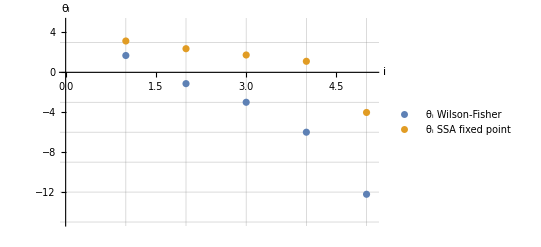

```mathematica
ListPlot[{-EVWF, -EVSSAFP}, AxesLabel->{"i","θ_i"}, GridLines->{{1,2,3,4,5}, {3,0,-3,-6,-9, -12, -15}}, PlotRange->{{0,5.1}, {-15,5}}, PlotLegends-> {{"θ_i Wilson-Fisher", "θ_i SSA fixed point"}}]
```

```mathematica
(*Export["StabilityCoefficientsWFvsSSAFPsinglescalarfield.jpg",%55,"JPEG"]
```

StabilityCoefficientsWFvsSSAFPsinglescalarfield.jpg

# Wetterich equation for multiple scalar fields d=3

## No anomalous dimension included (LPA)

```mathematica
RHSWetterich = (k^3 Nphi)/(6 π^2 (1+W1))-(2 k^2 (2+Nphi) W2 ϕ^2)/(3 π^2 (1+W1)^2)-(k (-8 (8+Nphi) W2^2+3 (4+Nphi) (1+W1) W3) ϕ^4)/(3 π^2 (1+W1)^3)-(8 W2 (4 (26+Nphi) W2^2-3 (14+Nphi) (1+W1) W3) ϕ^6)/(3 π^2 (1+W1)^4)
```

(k^3 Nphi)/(6 π^2 (1+W1))-(2 k^2 (2+Nphi) W2 ϕ^2)/(3 π^2 (1+W1)^2)-(k (-8 (8+Nphi) W2^2+3 (4+Nphi) (1+W1) W3) ϕ^4)/(3 π^2 (1+W1)^3)-(8 W2 (4 (26+Nphi) W2^2-3 (14+Nphi) (1+W1) W3) ϕ^6)/(3 π^2 (1+W1)^4)

```mathematica
LHSWetterich = 2 k^2 W1 ϕ^2+βW1 k^2 ϕ^2+k W2 ϕ^4+βW2 k ϕ^4+βW3 ϕ^6
```

2 k^2 W1 ϕ^2+k^2 βW1 ϕ^2+k W2 ϕ^4+k βW2 ϕ^4+βW3 ϕ^6

## Finding the fixed points+beta functions+stability coefficients.

```mathematica
βW1=0;
βW2=0;
βW3=0;
```

```mathematica
Solve[Coefficient[RHSWetterich, ϕ^6]== Coefficient[LHSWetterich,ϕ^6], W3]
```

{{W3→(4 (26+Nphi) W2^2)/(3 (14+Nphi) (1+W1))}}

```mathematica
Solve[Coefficient[RHSWetterich, ϕ^4]== Coefficient[LHSWetterich,ϕ^4]/.W3->(4 (26+Nphi) W2^2)/(3 (14+Nphi) (1+W1)), W2]
```

{{W2→0},{W2→3/(64/(π^2 (1+W1)^3)+(8 Nphi)/(π^2 (1+W1)^3)-416/((14+Nphi) π^2 (1+W1)^3)-(120 Nphi)/((14+Nphi) π^2 (1+W1)^3)-(4 Nphi^2)/((14+Nphi) π^2 (1+W1)^3))}}

```mathematica
Solve[Coefficient[RHSWetterich, ϕ^2]== Coefficient[LHSWetterich,ϕ^2]/.W3->(4 (26+Nphi) W2^2)/(3 (14+Nphi) (1+W1))/.W2->0, W1]
```

{{W1→0}}

```mathematica
Solve[Coefficient[RHSWetterich, ϕ^2]== Coefficient[LHSWetterich,ϕ^2]/.W3->(4 (26+Nphi) W2^2)/(3 (14+Nphi) (1+W1))/.W2->3/(64/(π^2 (1+W1)^3)+(8 Nphi)/(π^2 (1+W1)^3)-416/((14+Nphi) π^2 (1+W1)^3)-(120 Nphi)/((14+Nphi) π^2 (1+W1)^3)-(4 Nphi^2)/((14+Nphi) π^2 (1+W1)^3)), W1]
```

{{W1→(-28-16 Nphi-Nphi^2)/(508+72 Nphi+5 Nphi^2)}}

```mathematica
W1val = (-28-16 Nphi-Nphi^2)/(508+72 Nphi+5 Nphi^2)
```

(-28-16 Nphi-Nphi^2)/(508+72 Nphi+5 Nphi^2)

```mathematica
Simplify[3/(64/(π^2 (1+W1)^3)+(8 Nphi)/(π^2 (1+W1)^3)-416/((14+Nphi) π^2 (1+W1)^3)-(120 Nphi)/((14+Nphi) π^2 (1+W1)^3)-(4 Nphi^2)/((14+Nphi) π^2 (1+W1)^3))//.W1->(-28-16 Nphi-Nphi^2)/(508+72 Nphi+5 Nphi^2)]
```

(48 (14+Nphi) (120+14 Nphi+Nphi^2)^2 π^2)/((508+72 Nphi+5 Nphi^2)^3)

```mathematica
W2val= (48 (14+Nphi) (120+14 Nphi+Nphi^2)^2 π^2)/((508+72 Nphi+5 Nphi^2)^3)
```

(48 (14+Nphi) (120+14 Nphi+Nphi^2)^2 π^2)/((508+72 Nphi+5 Nphi^2)^3)

```mathematica
(4 (26+Nphi) W2^2)/(3 (14+Nphi) (1+W1))/.W2-> W2val/.W1-> W1val
```

(3072 (14+Nphi) (26+Nphi) (120+14 Nphi+Nphi^2)^4 π^4)/((508+72 Nphi+5 Nphi^2)^6 (1+(-28-16 Nphi-Nphi^2)/(508+72 Nphi+5 Nphi^2)))

```mathematica
W3val =(3072 (14+Nphi) (26+Nphi) (120+14 Nphi+Nphi^2)^4 π^4)/((508+72 Nphi+5 Nphi^2)^6 (1+(-28-16 Nphi-Nphi^2)/(508+72 Nphi+5 Nphi^2)));
```

### Beta-functions

```mathematica
Clear[βW1];
Clear[βW2];
Clear[βW3];
```

```mathematica
Solve[Coefficient[RHSWetterich, ϕ^6]== Coefficient[LHSWetterich,ϕ^6], βW3]
```

{{βW3→-(8 W2 (104 W2^2+4 Nphi W2^2-42 W3-3 Nphi W3-42 W1 W3-3 Nphi W1 W3))/(3 π^2 (1+W1)^4)}}

```mathematica
β[W_[1], W_[2], W_[3]][3]= -(8 W[2] (104 W[2]^2+4 Nphi W[2]^2-42 W[3]-3 Nphi W[3]-42 W[1] W[3]-3 Nphi W[1] W[3]))/(3 π^2 (1+W[1])^4)
```

-(8 W[2] (104 W[2]^2+4 Nphi W[2]^2-42 W[3]-3 Nphi W[3]-42 W[1] W[3]-3 Nphi W[1] W[3]))/(3 π^2 (1+W[1])^4)

```mathematica
Simplify[Solve[Coefficient[RHSWetterich, ϕ^4]== Coefficient[LHSWetterich,ϕ^4], βW2]]
```

{{βW2→-W2+(8 (8+Nphi) W2^2-3 (4+Nphi) (1+W1) W3)/(3 π^2 (1+W1)^3)}}

```mathematica
β[W_[1], W_[2], W_[3]][2]=-W[2]+(8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3])/(3 π^2 (1+W[1])^3)
```

-W[2]+(8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3])/(3 π^2 (1+W[1])^3)

```mathematica
Simplify[Solve[Coefficient[RHSWetterich, ϕ^2]== Coefficient[LHSWetterich,ϕ^2], βW1]]
```

{{βW1→-2 W1-(2 (2+Nphi) W2)/(3 π^2 (1+W1)^2)}}

```mathematica
β[W_[1], W_[2], W_[3]][1] = -2 W[1]-(2 (2+Nphi) W[2])/(3 π^2 (1+W[1])^2)
```

-2 W[1]-(2 (2+Nphi) W[2])/(3 π^2 (1+W[1])^2)

```mathematica
matphi6notpowerkin:=Table[D[β[W[1], W[2], W[3]][ a], W[b]],{a,1,3},{b,1,3}](*Generates the stability matrix*)
matphi6notpowerkin//MatrixForm(*Prints the stability matrix in Matrixform*)
EVphi6notpowerkin = Eigenvalues[%]/.W[1]-> W1val/. W[2]-> W2val/.W[3]-> W3val(*Determines the eigenvalues of the stability matrix*)
```

(-2+(4 (2+Nphi) W[2])/(3 π^2 (1+W[1])^3) | -(2 (2+Nphi))/(3 π^2 (1+W[1])^2) | 0
-((4+Nphi) W[3])/(π^2 (1+W[1])^3)-(8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3])/(π^2 (1+W[1])^4) | -1+(16 (8+Nphi) W[2])/(3 π^2 (1+W[1])^3) | -(4+Nphi)/(π^2 (1+W[1])^2)
-(8 W[2] (-42 W[3]-3 Nphi W[3]))/(3 π^2 (1+W[1])^4)+(32 W[2] (104 W[2]^2+4 Nphi W[2]^2-42 W[3]-3 Nphi W[3]-42 W[1] W[3]-3 Nphi W[1] W[3]))/(3 π^2 (1+W[1])^5) | -(8 W[2] (208 W[2]+8 Nphi W[2]))/(3 π^2 (1+W[1])^4)-(8 (104 W[2]^2+4 Nphi W[2]^2-42 W[3]-3 Nphi W[3]-42 W[1] W[3]-3 Nphi W[1] W[3]))/(3 π^2 (1+W[1])^4) | -(8 (-42-3 Nphi-42 W[1]-3 Nphi W[1]) W[2])/(3 π^2 (1+W[1])^4))

```mathematica
N[W1val/.Nphi-> 1]
N[W2val/. Nphi-> 1]
N[W3val/. Nphi-> 1]
```

-0.0769231

0.646893

1.08802

```mathematica
N[-EVphi6notpowerkin/. Nphi-> 1]
```

{1.83392,-0.96849,-12.1988}

```mathematica
1/1.833
```

0.545554

```mathematica
N[-EVphi6notpowerkin/. Nphi-> 100]
```

{1.53815,-1.1699,-9.42138}

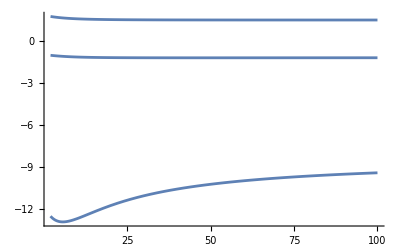

```mathematica
Plot[-EVphi6notpowerkin/. Nphi-> x, {x, 2, 100}]
```

```mathematica
N[W1val/.Nphi-> 100]
N[W2val/.Nphi-> 100]
N[W3val/.Nphi-> 100]
```

-0.201497

0.0372943

0.00256693

To be able to combine properly, we need to use not just the LPA, but an extension of this that includes the anomalous dimension.

## Using the wave renormalization factor and anomalous dimension (LPA’)

### Set-up

```mathematica
RHSwett = -(k^3 Nphi (-5+ηϕ))/(30 π^2 (1+W[1]))+(2 k^2 (2+Nphi) W[2] (-5+ηϕ) ϕ^2)/(15 π^2 (1+W[1])^2)+(k (-8 (8+Nphi) W[2]^2+3 (4+Nphi) (1+W[1]) W[3]) (-5+ηϕ) ϕ^4)/(15 π^2 (1+W[1])^3)+(8 W[2] (4 (26+Nphi) W[2]^2-3 (14+Nphi) (1+W[1]) W[3]) (-5+ηϕ) ϕ^6)/(15 π^2 (1+W[1])^4);(*Save the RHS of the wetterich equation from the xAct file.*)
```

```mathematica
LHSwett =-ηϕ X+(2 W[1]-ηϕ W[1]+βw3[1])k^2 ϕ^2+(W[2]-2ηϕ W[2]+  βw3[2])k ϕ^4+(-3 ηϕ W[3]+ βw3[3])ϕ^6 ; (*LHS wetterich*)
```

```mathematica
Solve[Coefficient[RHSwett, X]== Coefficient[LHSwett, X], ηϕ](*Find the anomalous dimension*)
```

{{ηϕ→0}}

### Finding fixed points

The first step is to find the fixed points.

```mathematica
βw3[1]=0;
βw3[2]=0;
βw3[3]=0;(*To find the fixed points, beta is set to 0*)
Solve[Coefficient[RHSwett, ϕ^6]== Coefficient[LHSwett,ϕ^6]/. ηϕ-> 0, W[3]](*First solve the highest order for the corresponding coefficient*)
```

{{W[3]→(4 (26+Nphi) W[2]^2)/(3 (14+Nphi) (1+W[1]))}}

```mathematica
w3val = (4 (26+Nphi) W[2]^2)/(3 (14+Nphi) (1+W[1]));(*Save the result of the previous evaluation to easily substitute it later*)
```

```mathematica
Simplify[Solve[Coefficient[RHSwett, ϕ^4]== Coefficient[LHSwett,ϕ^4]/. ηϕ-> 0/.W[3]-> w3val, W[2]]](*Solve next order of ϕ, for the next coefficient*)
```

{{W[2]→0},{W[2]→(3 (14+Nphi) π^2 (1+W[1])^3)/(4 (120+14 Nphi+Nphi^2))}}

```mathematica
w2val = (3 (14+Nphi) π^2 (1+W[1])^3)/(4 (120+14 Nphi+Nphi^2));(*Saves the non-zero result*)
```

Next solve for the ϕ^2-component twice, one time for each W_2 solution.

```mathematica
Simplify[Solve[Coefficient[RHSwett, ϕ^2]== Coefficient[LHSwett,ϕ^2]/. ηϕ-> 0/.W[3]-> w3val/.W[2]-> 0, W[1]]]
```

{{W[1]→0}}

The (0,0,0)-fixed point is the Gaussian fixed point, and not the one of interest right now.

```mathematica
Simplify[Solve[Coefficient[RHSwett, ϕ^2]== Coefficient[LHSwett,ϕ^2]/. ηϕ-> 0/.W[3]-> w3val/.W[2]-> w2val, W[1]]]
```

{{W[1]→-((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2)}}

```mathematica
w1val = ((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2);
```

Now the W_1 value of the NGFP is determined, it can be used to solve W_2 and W_3

```mathematica
Simplify[w2val/.W[1]-> w1val]
```

(3 (14+Nphi) (1+((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2))^3 π^2)/(4 (120+14 Nphi+Nphi^2))

```mathematica
Simplify[w3val/.W[2]-> w2val//.W[1]-> w1val]
```

(3 (14+Nphi) (26+Nphi) (1+((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2))^5 π^4)/(4 (120+14 Nphi+Nphi^2)^2)

### Beta function

After determining the fixed points, the beta functions are determined, by making sure beta is a variable and solving order by order for the different betas.

```mathematica
Clear[βw3]
```

```mathematica
Simplify[Solve[Coefficient[RHSwett, ϕ^6]== Coefficient[LHSwett,ϕ^6]/. ηϕ-> 0, βw3[3]]]
```

{{βw3[3]→(8 W[2] (-4 (26+Nphi) W[2]^2+3 (14+Nphi) (1+W[1]) W[3]))/(3 π^2 (1+W[1])^4)}}

```mathematica
βw3[W_[1], W_[2], W_[3]][3] = (8 W[2] (-4 (26+Nphi) W[2]^2+3 (14+Nphi) (1+W[1]) W[3]))/(3 π^2 (1+W[1])^4);(*Save the beta functions for use to determine the stability matrix*)
```

```mathematica
Simplify[Solve[Coefficient[RHSwett, ϕ^4]== Coefficient[LHSwett,ϕ^4]/. ηϕ-> 0, βw3[2]]]
```

{{βw3[2]→-W[2]+(8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3])/(3 π^2 (1+W[1])^3)}}

```mathematica
βw3[W_[1], W_[2], W_[3]][2] =-W[2]+(8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3])/(3 π^2 (1+W[1])^3);(*Save the beta functions for use to determine the stability matrix*)
```

```mathematica
Simplify[Solve[Coefficient[RHSwett, ϕ^2]== Coefficient[LHSwett,ϕ^2]/. ηϕ-> 0, βw3[1]]]
```

{{βw3[1]→-2 W[1]-(2 (2+Nphi) W[2])/(3 π^2 (1+W[1])^2)}}

```mathematica
βw3[W_[1], W_[2], W_[3]][1]=  -2 W[1]-(2 (2+Nphi) W[2])/(3 π^2 (1+W[1])^2);(*Save the beta functions for use to determine the stability matrix*)
```

### Stability matrix+EV’s

```mathematica
matphi6notpowerkin:=Table[D[βw3[W[1], W[2], W[3]][ a], W[b]],{a,1,3},{b,1,3}](*Generates the stability matrix*)
matphi6notpowerkin//MatrixForm(*Prints the stability matrix in Matrixform*)
EVphi6notpowerkin = Eigenvalues[%]/.W[3]-> w3val//. W[2]-> w2val//.W[1]-> w1val(*Calculate the eigenvalues at the NGFP position, as the NGFP W-values are added in*)
```

(-2+(4 (2+Nphi) W[2])/(3 π^2 (1+W[1])^3) | -(2 (2+Nphi))/(3 π^2 (1+W[1])^2) | 0
-((4+Nphi) W[3])/(π^2 (1+W[1])^3)-(8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3])/(π^2 (1+W[1])^4) | -1+(16 (8+Nphi) W[2])/(3 π^2 (1+W[1])^3) | -(4+Nphi)/(π^2 (1+W[1])^2)
(8 (14+Nphi) W[2] W[3])/(π^2 (1+W[1])^4)-(32 W[2] (-4 (26+Nphi) W[2]^2+3 (14+Nphi) (1+W[1]) W[3]))/(3 π^2 (1+W[1])^5) | -(64 (26+Nphi) W[2]^2)/(3 π^2 (1+W[1])^4)+(8 (-4 (26+Nphi) W[2]^2+3 (14+Nphi) (1+W[1]) W[3]))/(3 π^2 (1+W[1])^4) | (8 (14+Nphi) W[2])/(π^2 (1+W[1])^3))

```mathematica
N[-EVphi6notpowerkin/. Nphi-> 12](*Test if it works for a specific value of Subscript[N, ϕ]*)
```

{1.60515,-1.13118,-12.5203}

```mathematica
EVphi6notpowerkincollw1 = {};
EVphi6notpowerkincollw2 = {};
EVphi6notpowerkincollw3 = {};
Do[AppendTo[ EVphi6notpowerkincollw1, {x, N[-EVphi6notpowerkin/. Nphi-> x][[1]]}];
AppendTo[ EVphi6notpowerkincollw2, {x, N[-EVphi6notpowerkin/. Nphi-> x][[2]]}];
AppendTo[ EVphi6notpowerkincollw3, {x, N[-EVphi6notpowerkin/. Nphi-> x][[3]]}], {x,2,1002, 1 }](*Loop that calculates the eigenvalues for 1<Subscript[N, ϕ]<1003*)
```

```mathematica
EVphi6notpowerkincollw3(*Check if the loop preforms as intended*)
```

{{2,-12.5348},{12,-12.5203},{22,-11.6097}}

```mathematica
DumpSave["EVphi6notpowerkincollw1.mx", EVphi6notpowerkincollw1];
DumpSave["EVphi6notpowerkincollw2.mx", EVphi6notpowerkincollw2];
DumpSave["EVphi6notpowerkincollw3.mx", EVphi6notpowerkincollw3];(*Save the found values*)
```

```mathematica
DumpGet["EVphi6notpowerkincollw1.mx"];
DumpGet["EVphi6notpowerkincollw2.mx"];
DumpGet["EVphi6notpowerkincollw3.mx"];
```

```mathematica
1/1.72701
```

0.579035

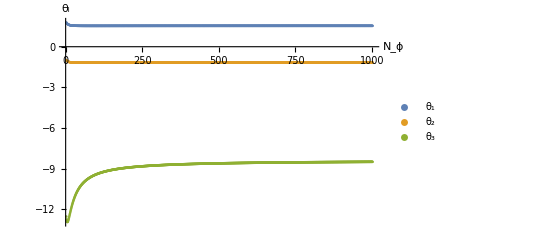

```mathematica
ListPlot[{EVphi6notpowerkincollw1, EVphi6notpowerkincollw2, EVphi6notpowerkincollw3}, PlotLegends->{"θ_1", "θ_2", "θ_3"}, AxesLabel->{"N_ϕ", "θ_i"}]
```

```mathematica
1/1.54
```

0.649351

```mathematica
Export["EVphi6LPAprimetot.jpg", %5, "JPEG"]
```

EVphi6LPAprimetot.jpg

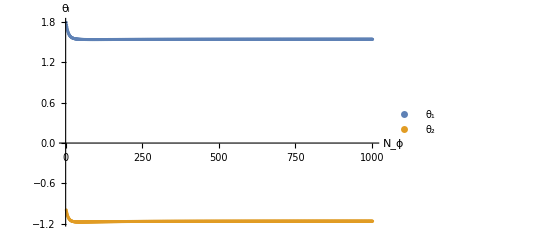

```mathematica
ListPlot[{EVphi6notpowerkincollw1, EVphi6notpowerkincollw2}, PlotLegends->{"θ_1", "θ_2"}, AxesLabel->{"N_ϕ", "θ_i"}]
```

```mathematica
Export["EVphi6LPAprimezoom.jpg", %6, "JPEG"]
```

EVphi6LPAprimezoom.jpg

## Combining the LPA’ and the SSA

## Set-up

#### From xAct

From the xAct notebook, the right hand side of the wetterich equation is obtained.

```mathematica
RHSWETTLPASSAmultiplescalarfieldsFullxAct = (k^3 Nphi)/(6 π^2 (1+W[1])^4)+(k^3 Nphi W[1])/(2 π^2 (1+W[1])^4)+(k^3 Nphi W[1]^2)/(2 π^2 (1+W[1])^4)+(k^3 Nphi W[1]^3)/(6 π^2 (1+W[1])^4)-(k^3 Nphi ηϕ)/(30 π^2 (1+W[1])^4)-(k^3 Nphi W[1] ηϕ)/(10 π^2 (1+W[1])^4)-(k^3 Nphi W[1]^2 ηϕ)/(10 π^2 (1+W[1])^4)-(k^3 Nphi W[1]^3 ηϕ)/(30 π^2 (1+W[1])^4)+Subscript[S, 2] ((16 U[1]^2)/(105 k^3 π^2 (1+W[1])^4)+(24 U[1]U[2])/(35 k^3 π^2 (1+W[1])^4)+(62 U[2]^2)/(105 k^3 π^2 (1+W[1])^4)+(4 Nphi U[2]^2)/(105 k^3 π^2 (1+W[1])^4)+(16 U[1]^2 W[1])/(105 k^3 π^2 (1+W[1])^4)+(24 U[1]U[2] W[1])/(35 k^3 π^2 (1+W[1])^4)+(62 U[2]^2 W[1])/(105 k^3 π^2 (1+W[1])^4)+(4 Nphi U[2]^2 W[1])/(105 k^3 π^2 (1+W[1])^4)-(16 U[1]^2 ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(8 U[1]U[2]ηϕ)/(105 k^3 π^2 (1+W[1])^4)-(62 U[2]^2 ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(4 Nphi U[2]^2 ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(16 U[1]^2 W[1] ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(8 U[1] U[2] W[1] ηϕ)/(105 k^3 π^2 (1+W[1])^4)-(62 U[2]^2 W[1] ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(4 Nphi U[2]^2 W[1] ηϕ)/(945 k^3 π^2 (1+W[1])^4))+X^2 ((16 U[1]^2)/(35 k^3 π^2 (1+W[1])^4)+(2 Nphi U[1]^2)/(7 k^3 π^2 (1+W[1])^4)+(32 U[1]U[2])/(35 k^3 π^2 (1+W[1])^4)+(4 Nphi U[1]U[2])/(21 k^3 π^2 (1+W[1])^4)+(26 U[2]^2)/(105 k^3 π^2 (1+W[1])^4)+(2 Nphi U[2]^2)/(105 k^3 π^2 (1+W[1])^4)+(16 U[1]^2 W[1])/(35 k^3 π^2 (1+W[1])^4)+(2 Nphi U[1]^2 W[1])/(7 k^3 π^2 (1+W[1])^4)+(32 U[1]U[2] W[1])/(35 k^3 π^2 (1+W[1])^4)+(4 Nphi U[1]U[2] W[1])/(21 k^3 π^2 (1+W[1])^4)+(26 U[2]^2 W[1])/(105 k^3 π^2 (1+W[1])^4)+(2 Nphi U[2]^2 W[1])/(105 k^3 π^2 (1+W[1])^4)-(16 U[1]^2 ηϕ)/(315 k^3 π^2 (1+W[1])^4)-(2 Nphi U[1]^2 ηϕ)/(63 k^3 π^2 (1+W[1])^4)-(32 U[1] U[2] ηϕ)/(315 k^3 π^2 (1+W[1])^4)-(4 Nphi U[1] U[2] ηϕ)/(189 k^3 π^2 (1+W[1])^4)-(26 U[2]^2 ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(2 Nphi U[2]^2 ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(16 U[1]^2 W[1] ηϕ)/(315 k^3 π^2 (1+W[1])^4)-(2 Nphi U[1]^2 W[1] ηϕ)/(63 k^3 π^2 (1+W[1])^4)-(32 U[1] U[2] W[1] ηϕ)/(315 k^3 π^2 (1+W[1])^4)-(4 Nphi U[1] U[2]W[1] ηϕ)/(189 k^3 π^2 (1+W[1])^4)-(26 U[2]^2 W[1] ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(2 Nphi U[2]^2 W[1] ηϕ)/(945 k^3 π^2 (1+W[1])^4))-(4 k^2 W[2] ϕ^2)/(3 π^2 (1+W[1])^4)-(2 k^2 Nphi W[2] ϕ^2)/(3 π^2 (1+W[1])^4)-(8 k^2 W[1] W[2] ϕ^2)/(3 π^2 (1+W[1])^4)-(4 k^2 Nphi W[1] W[2] ϕ^2)/(3 π^2 (1+W[1])^4)-(4 k^2 W[1]^2 W[2] ϕ^2)/(3 π^2 (1+W[1])^4)-(2 k^2 Nphi W[1]^2 W[2] ϕ^2)/(3 π^2 (1+W[1])^4)+(4 k^2 W[2] ηϕ ϕ^2)/(15 π^2 (1+W[1])^4)+(2 k^2 Nphi W[2] ηϕ ϕ^2)/(15 π^2 (1+W[1])^4)+(8 k^2 W[1] W[2] ηϕ ϕ^2)/(15 π^2 (1+W[1])^4)+(4 k^2 Nphi W[1] W[2] ηϕ ϕ^2)/(15 π^2 (1+W[1])^4)+(4 k^2 W[1]^2 W[2] ηϕ ϕ^2)/(15 π^2 (1+W[1])^4)+(2 k^2 Nphi W[1]^2 W[2] ηϕ ϕ^2)/(15 π^2 (1+W[1])^4)+(64 k W[2]^2 ϕ^4)/(3 π^2 (1+W[1])^4)+(8 k Nphi W[2]^2 ϕ^4)/(3 π^2 (1+W[1])^4)+(64 k W[1] W[2]^2 ϕ^4)/(3 π^2 (1+W[1])^4)+(8 k Nphi W[1] W[2]^2 ϕ^4)/(3 π^2 (1+W[1])^4)-(4 k W[3] ϕ^4)/(π^2 (1+W[1])^4)-(k Nphi W[3] ϕ^4)/(π^2 (1+W[1])^4)-(8 k W[1] W[3] ϕ^4)/(π^2 (1+W[1])^4)-(2 k Nphi W[1] W[3] ϕ^4)/(π^2 (1+W[1])^4)-(4 k W[1]^2 W[3] ϕ^4)/(π^2 (1+W[1])^4)-(k Nphi W[1]^2 W[3] ϕ^4)/(π^2 (1+W[1])^4)-(64 k W[2]^2 ηϕ ϕ^4)/(15 π^2 (1+W[1])^4)-(8 k Nphi W[2]^2 ηϕ ϕ^4)/(15 π^2 (1+W[1])^4)-(64 k W[1] W[2]^2 ηϕ ϕ^4)/(15 π^2 (1+W[1])^4)-(8 k Nphi W[1] W[2]^2 ηϕ ϕ^4)/(15 π^2 (1+W[1])^4)+(4 k W[3] ηϕ ϕ^4)/(5 π^2 (1+W[1])^4)+(k Nphi W[3] ηϕ ϕ^4)/(5 π^2 (1+W[1])^4)+(8 k W[1] W[3] ηϕ ϕ^4)/(5 π^2 (1+W[1])^4)+(2 k Nphi W[1] W[3] ηϕ ϕ^4)/(5 π^2 (1+W[1])^4)+(4 k W[1]^2 W[3] ηϕ ϕ^4)/(5 π^2 (1+W[1])^4)+(k Nphi W[1]^2 W[3] ηϕ ϕ^4)/(5 π^2 (1+W[1])^4)-(832 W[2]^3 ϕ^6)/(3 π^2 (1+W[1])^4)-(32 Nphi W[2]^3 ϕ^6)/(3 π^2 (1+W[1])^4)+(112 W[2] W[3] ϕ^6)/(π^2 (1+W[1])^4)+(8 Nphi W[2] W[3] ϕ^6)/(π^2 (1+W[1])^4)+(112 W[1] W[2] W[3] ϕ^6)/(π^2 (1+W[1])^4)+(8 Nphi W[1] W[2] W[3] ϕ^6)/(π^2 (1+W[1])^4)+(832 W[2]^3 ηϕ ϕ^6)/(15 π^2 (1+W[1])^4)+(32 Nphi W[2]^3 ηϕ ϕ^6)/(15 π^2 (1+W[1])^4)-(112 W[2] W[3] ηϕ ϕ^6)/(5 π^2 (1+W[1])^4)-(8 Nphi W[2] W[3] ηϕ ϕ^6)/(5 π^2 (1+W[1])^4)-(112 W[1] W[2] W[3] ηϕ ϕ^6)/(5 π^2 (1+W[1])^4)-(8 Nphi W[1] W[2] W[3] ηϕ ϕ^6)/(5 π^2 (1+W[1])^4)+(144 W[3]^2 ϕ^8)/(k π^2 (1+W[1])^4)+(6 Nphi W[3]^2 ϕ^8)/(k π^2 (1+W[1])^4)+(144 W[1] W[3]^2 ϕ^8)/(√(k^2) π^2 (1+W[1])^4)+(6 Nphi W[1] W[3]^2 ϕ^8)/(√(k^2) π^2 (1+W[1])^4)-(72 W[3]^2 ηϕ ϕ^8)/(k π^2 (1+W[1])^4)+(216 W[3]^2 ηϕ ϕ^8)/(5 √(k^2) π^2 (1+W[1])^4)-(3 Nphi W[3]^2 ηϕ ϕ^8)/(k π^2 (1+W[1])^4)+(9 Nphi W[3]^2 ηϕ ϕ^8)/(5 √(k^2) π^2 (1+W[1])^4)-(144 W[1] W[3]^2 ηϕ ϕ^8)/(5 √(k^2) π^2 (1+W[1])^4)-(6 Nphi W[1] W[3]^2 ηϕ ϕ^8)/(5 √(k^2) π^2 (1+W[1])^4)+X (-(2 U[1])/(15 π^2 (1+W[1])^4)-(Nphi U[1])/(5 π^2 (1+W[1])^4)-(4 U[2])/(15 π^2 (1+W[1])^4)-(Nphi U[2])/(15 π^2 (1+W[1])^4)-(4 U[1]W[1])/(15 π^2 (1+W[1])^4)-(2 Nphi U[1] W[1])/(5 π^2 (1+W[1])^4)-(8 U[2] W[1])/(15 π^2 (1+W[1])^4)-(2 Nphi U[2]W[1])/(15 π^2 (1+W[1])^4)-(2 U[1] W[1]^2)/(15 π^2 (1+W[1])^4)-(Nphi U[1] W[1]^2)/(5 π^2 (1+W[1])^4)-(4 U[2] W[1]^2)/(15 π^2 (1+W[1])^4)-(Nphi U[2] W[1]^2)/(15 π^2 (1+W[1])^4)+(2 U[1] ηϕ)/(105 π^2 (1+W[1])^4)+(Nphi U[1] ηϕ)/(35 π^2 (1+W[1])^4)+(4 U[2]ηϕ)/(105 π^2 (1+W[1])^4)+(Nphi U[2] ηϕ)/(105 π^2 (1+W[1])^4)+(4 U[1] W[1] ηϕ)/(105 π^2 (1+W[1])^4)+(2 Nphi U[1]W[1] ηϕ)/(35 π^2 (1+W[1])^4)+(8 U[2] W[1] ηϕ)/(105 π^2 (1+W[1])^4)+(2 Nphi U[2] W[1] ηϕ)/(105 π^2 (1+W[1])^4)+(2 U[1] W[1]^2 ηϕ)/(105 π^2 (1+W[1])^4)+(Nphi U[1] W[1]^2 ηϕ)/(35 π^2 (1+W[1])^4)+(4 U[2] W[1]^2 ηϕ)/(105 π^2 (1+W[1])^4)+(Nphi U[2] W[1]^2 ηϕ)/(105 π^2 (1+W[1])^4)+(16 U[1] W[2] ϕ^2)/(5 k π^2 (1+W[1])^4)+(16 U[1]W[2] ϕ^2)/(15 √(k^2) π^2 (1+W[1])^4)+(8 Nphi U[1]W[2] ϕ^2)/(5 k π^2 (1+W[1])^4)+(16 U[2] W[2] ϕ^2)/(15 k π^2 (1+W[1])^4)+(32 U[2] W[2] ϕ^2)/(15 √(k^2) π^2 (1+W[1])^4)+(8 Nphi U[2] W[2] ϕ^2)/(15 k π^2 (1+W[1])^4)+(64 U[1]W[1] W[2] ϕ^2)/(15 √(k^2) π^2 (1+W[1])^4)+(8 Nphi U[1]W[1] W[2] ϕ^2)/(5 √(k^2) π^2 (1+W[1])^4)+(16 U[2] W[1] W[2] ϕ^2)/(5 √(k^2) π^2 (1+W[1])^4)+(8 Nphi U[2] W[1] W[2] ϕ^2)/(15 √(k^2) π^2 (1+W[1])^4)-(16 U[1] W[2] ηϕ ϕ^2)/(35 k π^2 (1+W[1])^4)-(16 U[1] W[2] ηϕ ϕ^2)/(105 √(k^2) π^2 (1+W[1])^4)-(8 Nphi U[1] W[2] ηϕ ϕ^2)/(35 k π^2 (1+W[1])^4)-(16 U[2] W[2] ηϕ ϕ^2)/(105 k π^2 (1+W[1])^4)-(32 U[2] W[2] ηϕ ϕ^2)/(105 √(k^2) π^2 (1+W[1])^4)-(8 Nphi U[2] W[2] ηϕ ϕ^2)/(105 k π^2 (1+W[1])^4)-(64 U[1] W[1] W[2] ηϕ ϕ^2)/(105 √(k^2) π^2 (1+W[1])^4)-(8 Nphi U[1]W[1] W[2] ηϕ ϕ^2)/(35 √(k^2) π^2 (1+W[1])^4)-(16 U[2] W[1] W[2] ηϕ ϕ^2)/(35 √(k^2) π^2 (1+W[1])^4)-(8 Nphi U[2]W[1] W[2] ηϕ ϕ^2)/(105 √(k^2) π^2 (1+W[1])^4)+(56 U[1]W[3] ϕ^4)/(5 k^2 π^2 (1+W[1])^4)+(12 Nphi U[1] W[3] ϕ^4)/(5 k^2 π^2 (1+W[1])^4)+(32 U[2] W[3] ϕ^4)/(5 k^2 π^2 (1+W[1])^4)+(4 Nphi U[2] W[3] ϕ^4)/(5 k^2 π^2 (1+W[1])^4)+(56 U[1] W[1] W[3] ϕ^4)/(5 k^2 π^2 (1+W[1])^4)+(12 Nphi U[1] W[1] W[3] ϕ^4)/(5 k^2 π^2 (1+W[1])^4)+(32 U[2] W[1] W[3] ϕ^4)/(5 k^2 π^2 (1+W[1])^4)+(4 Nphi U[2]W[1] W[3] ϕ^4)/(5 k^2 π^2 (1+W[1])^4)-(8 U[1] W[3] ηϕ ϕ^4)/(5 k^2 π^2 (1+W[1])^4)-(12 Nphi U[1]W[3] ηϕ ϕ^4)/(35 k^2 π^2 (1+W[1])^4)-(32 U[2] W[3] ηϕ ϕ^4)/(35 k^2 π^2 (1+W[1])^4)-(4 Nphi U[2] W[3] ηϕ ϕ^4)/(35 k^2 π^2 (1+W[1])^4)-(8 U[1]W[1] W[3] ηϕ ϕ^4)/(5 k^2 π^2 (1+W[1])^4)-(12 Nphi U[1]W[1] W[3] ηϕ ϕ^4)/(35 k^2 π^2 (1+W[1])^4)-(32 U[2]W[1] W[3] ηϕ ϕ^4)/(35 k^2 π^2 (1+W[1])^4)-(4 Nphi U[2] W[1] W[3] ηϕ ϕ^4)/(35 k^2 π^2 (1+W[1])^4))-(16 (U[1]+2 U[2]) W[2] (-7+ηϕ) {{X, {{a, c, , μ}, {, , μ, }}}} {{ϕ, {{}, {a}}}} {{ϕ, {{}, {c}}}})/(105 k π^2 (1+W[1])^4)-(16 (U[1]+2 U[2]) W[1] W[2] (-7+ηϕ) {{X, {{a, c, , μ}, {, , μ, }}}} {{ϕ, {{}, {a}}}} {{ϕ, {{}, {c}}}})/(105 √(k^2) π^2 (1+W[1])^4)-(16 (U[1]+2 U[2]) W[3] (-7+ηϕ) ϕ^2 {{X, {{a, c, , μ}, {, , μ, }}}} {{ϕ, {{}, {a}}}} {{ϕ, {{}, {c}}}})/(35 k^2 π^2 (1+W[1])^4)-(16 (U[1]+2 U[2]) W[1] W[3] (-7+ηϕ) ϕ^2 {{X, {{a, c, , μ}, {, , μ, }}}} {{ϕ, {{}, {a}}}} {{ϕ, {{}, {c}}}})/(35 k^2 π^2 (1+W[1])^4)-(16 (U[1]+2 U[2]) W[2] (-7+ηϕ) {{X, {{, , , α}, {c, a, α, }}}} {{ϕ, {{a}, {}}}} {{ϕ, {{c}, {}}}})/(105 k π^2 (1+W[1])^4)-(16 (U[1]+2 U[2]) W[1] W[2] (-7+ηϕ) {{X, {{, , , α}, {c, a, α, }}}} {{ϕ, {{a}, {}}}} {{ϕ, {{c}, {}}}})/(105 √(k^2) π^2 (1+W[1])^4)-(16 (U[1]+2 U[2]) W[3] (-7+ηϕ) ϕ^2 {{X, {{, , , α}, {c, a, α, }}}} {{ϕ, {{a}, {}}}} {{ϕ, {{c}, {}}}})/(35 k^2 π^2 (1+W[1])^4)-(16 (U[1]+2 U[2]) W[1] W[3] (-7+ηϕ) ϕ^2 {{X, {{, , , α}, {c, a, α, }}}} {{ϕ, {{a}, {}}}} {{ϕ, {{c}, {}}}})/(35 k^2 π^2 (1+W[1])^4);
```

This still contains order ϕ^8-terms that are not included in the initial assumption and should therefore be removed. It also includes crossterms that should vanish anyway, so to speed up the evaluation, these will be erased from the integral.

```mathematica
RHSWETTLPASSAmultiplescalarfields = (k^3 Nphi)/(6 π^2 (1+W[1])^4)+(k^3 Nphi W[1])/(2 π^2 (1+W[1])^4)+(k^3 Nphi W[1]^2)/(2 π^2 (1+W[1])^4)+(k^3 Nphi W[1]^3)/(6 π^2 (1+W[1])^4)-(k^3 Nphi ηϕ)/(30 π^2 (1+W[1])^4)-(k^3 Nphi W[1] ηϕ)/(10 π^2 (1+W[1])^4)-(k^3 Nphi W[1]^2 ηϕ)/(10 π^2 (1+W[1])^4)-(k^3 Nphi W[1]^3 ηϕ)/(30 π^2 (1+W[1])^4)+Subscript[S, 2] ((16 U[1]^2)/(105 k^3 π^2 (1+W[1])^4)+(24 U[1]U[2])/(35 k^3 π^2 (1+W[1])^4)+(62 U[2]^2)/(105 k^3 π^2 (1+W[1])^4)+(4 Nphi U[2]^2)/(105 k^3 π^2 (1+W[1])^4)+(16 U[1]^2 W[1])/(105 k^3 π^2 (1+W[1])^4)+(24 U[1]U[2] W[1])/(35 k^3 π^2 (1+W[1])^4)+(62 U[2]^2 W[1])/(105 k^3 π^2 (1+W[1])^4)+(4 Nphi U[2]^2 W[1])/(105 k^3 π^2 (1+W[1])^4)-(16 U[1]^2 ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(8 U[1]U[2]ηϕ)/(105 k^3 π^2 (1+W[1])^4)-(62 U[2]^2 ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(4 Nphi U[2]^2 ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(16 U[1]^2 W[1] ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(8 U[1] U[2] W[1] ηϕ)/(105 k^3 π^2 (1+W[1])^4)-(62 U[2]^2 W[1] ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(4 Nphi U[2]^2 W[1] ηϕ)/(945 k^3 π^2 (1+W[1])^4))+X^2 ((16 U[1]^2)/(35 k^3 π^2 (1+W[1])^4)+(2 Nphi U[1]^2)/(7 k^3 π^2 (1+W[1])^4)+(32 U[1]U[2])/(35 k^3 π^2 (1+W[1])^4)+(4 Nphi U[1]U[2])/(21 k^3 π^2 (1+W[1])^4)+(26 U[2]^2)/(105 k^3 π^2 (1+W[1])^4)+(2 Nphi U[2]^2)/(105 k^3 π^2 (1+W[1])^4)+(16 U[1]^2 W[1])/(35 k^3 π^2 (1+W[1])^4)+(2 Nphi U[1]^2 W[1])/(7 k^3 π^2 (1+W[1])^4)+(32 U[1]U[2] W[1])/(35 k^3 π^2 (1+W[1])^4)+(4 Nphi U[1]U[2] W[1])/(21 k^3 π^2 (1+W[1])^4)+(26 U[2]^2 W[1])/(105 k^3 π^2 (1+W[1])^4)+(2 Nphi U[2]^2 W[1])/(105 k^3 π^2 (1+W[1])^4)-(16 U[1]^2 ηϕ)/(315 k^3 π^2 (1+W[1])^4)-(2 Nphi U[1]^2 ηϕ)/(63 k^3 π^2 (1+W[1])^4)-(32 U[1] U[2] ηϕ)/(315 k^3 π^2 (1+W[1])^4)-(4 Nphi U[1] U[2] ηϕ)/(189 k^3 π^2 (1+W[1])^4)-(26 U[2]^2 ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(2 Nphi U[2]^2 ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(16 U[1]^2 W[1] ηϕ)/(315 k^3 π^2 (1+W[1])^4)-(2 Nphi U[1]^2 W[1] ηϕ)/(63 k^3 π^2 (1+W[1])^4)-(32 U[1] U[2] W[1] ηϕ)/(315 k^3 π^2 (1+W[1])^4)-(4 Nphi U[1] U[2]W[1] ηϕ)/(189 k^3 π^2 (1+W[1])^4)-(26 U[2]^2 W[1] ηϕ)/(945 k^3 π^2 (1+W[1])^4)-(2 Nphi U[2]^2 W[1] ηϕ)/(945 k^3 π^2 (1+W[1])^4))-(4 k^2 W[2] ϕ^2)/(3 π^2 (1+W[1])^4)-(2 k^2 Nphi W[2] ϕ^2)/(3 π^2 (1+W[1])^4)-(8 k^2 W[1] W[2] ϕ^2)/(3 π^2 (1+W[1])^4)-(4 k^2 Nphi W[1] W[2] ϕ^2)/(3 π^2 (1+W[1])^4)-(4 k^2 W[1]^2 W[2] ϕ^2)/(3 π^2 (1+W[1])^4)-(2 k^2 Nphi W[1]^2 W[2] ϕ^2)/(3 π^2 (1+W[1])^4)+(4 k^2 W[2] ηϕ ϕ^2)/(15 π^2 (1+W[1])^4)+(2 k^2 Nphi W[2] ηϕ ϕ^2)/(15 π^2 (1+W[1])^4)+(8 k^2 W[1] W[2] ηϕ ϕ^2)/(15 π^2 (1+W[1])^4)+(4 k^2 Nphi W[1] W[2] ηϕ ϕ^2)/(15 π^2 (1+W[1])^4)+(4 k^2 W[1]^2 W[2] ηϕ ϕ^2)/(15 π^2 (1+W[1])^4)+(2 k^2 Nphi W[1]^2 W[2] ηϕ ϕ^2)/(15 π^2 (1+W[1])^4)+(64 k W[2]^2 ϕ^4)/(3 π^2 (1+W[1])^4)+(8 k Nphi W[2]^2 ϕ^4)/(3 π^2 (1+W[1])^4)+(64 k W[1] W[2]^2 ϕ^4)/(3 π^2 (1+W[1])^4)+(8 k Nphi W[1] W[2]^2 ϕ^4)/(3 π^2 (1+W[1])^4)-(4 k W[3] ϕ^4)/(π^2 (1+W[1])^4)-(k Nphi W[3] ϕ^4)/(π^2 (1+W[1])^4)-(8 k W[1] W[3] ϕ^4)/(π^2 (1+W[1])^4)-(2 k Nphi W[1] W[3] ϕ^4)/(π^2 (1+W[1])^4)-(4 k W[1]^2 W[3] ϕ^4)/(π^2 (1+W[1])^4)-(k Nphi W[1]^2 W[3] ϕ^4)/(π^2 (1+W[1])^4)-(64 k W[2]^2 ηϕ ϕ^4)/(15 π^2 (1+W[1])^4)-(8 k Nphi W[2]^2 ηϕ ϕ^4)/(15 π^2 (1+W[1])^4)-(64 k W[1] W[2]^2 ηϕ ϕ^4)/(15 π^2 (1+W[1])^4)-(8 k Nphi W[1] W[2]^2 ηϕ ϕ^4)/(15 π^2 (1+W[1])^4)+(4 k W[3] ηϕ ϕ^4)/(5 π^2 (1+W[1])^4)+(k Nphi W[3] ηϕ ϕ^4)/(5 π^2 (1+W[1])^4)+(8 k W[1] W[3] ηϕ ϕ^4)/(5 π^2 (1+W[1])^4)+(2 k Nphi W[1] W[3] ηϕ ϕ^4)/(5 π^2 (1+W[1])^4)+(4 k W[1]^2 W[3] ηϕ ϕ^4)/(5 π^2 (1+W[1])^4)+(k Nphi W[1]^2 W[3] ηϕ ϕ^4)/(5 π^2 (1+W[1])^4)-(832 W[2]^3 ϕ^6)/(3 π^2 (1+W[1])^4)-(32 Nphi W[2]^3 ϕ^6)/(3 π^2 (1+W[1])^4)+(112 W[2] W[3] ϕ^6)/(π^2 (1+W[1])^4)+(8 Nphi W[2] W[3] ϕ^6)/(π^2 (1+W[1])^4)+(112 W[1] W[2] W[3] ϕ^6)/(π^2 (1+W[1])^4)+(8 Nphi W[1] W[2] W[3] ϕ^6)/(π^2 (1+W[1])^4)+(832 W[2]^3 ηϕ ϕ^6)/(15 π^2 (1+W[1])^4)+(32 Nphi W[2]^3 ηϕ ϕ^6)/(15 π^2 (1+W[1])^4)-(112 W[2] W[3] ηϕ ϕ^6)/(5 π^2 (1+W[1])^4)-(8 Nphi W[2] W[3] ηϕ ϕ^6)/(5 π^2 (1+W[1])^4)-(112 W[1] W[2] W[3] ηϕ ϕ^6)/(5 π^2 (1+W[1])^4)-(8 Nphi W[1] W[2] W[3] ηϕ ϕ^6)/(5 π^2 (1+W[1])^4)+X (-(2 U[1])/(15 π^2 (1+W[1])^4)-(Nphi U[1])/(5 π^2 (1+W[1])^4)-(4 U[2])/(15 π^2 (1+W[1])^4)-(Nphi U[2])/(15 π^2 (1+W[1])^4)-(4 U[1]W[1])/(15 π^2 (1+W[1])^4)-(2 Nphi U[1] W[1])/(5 π^2 (1+W[1])^4)-(8 U[2] W[1])/(15 π^2 (1+W[1])^4)-(2 Nphi U[2]W[1])/(15 π^2 (1+W[1])^4)-(2 U[1] W[1]^2)/(15 π^2 (1+W[1])^4)-(Nphi U[1] W[1]^2)/(5 π^2 (1+W[1])^4)-(4 U[2] W[1]^2)/(15 π^2 (1+W[1])^4)-(Nphi U[2] W[1]^2)/(15 π^2 (1+W[1])^4)+(2 U[1] ηϕ)/(105 π^2 (1+W[1])^4)+(Nphi U[1] ηϕ)/(35 π^2 (1+W[1])^4)+(4 U[2]ηϕ)/(105 π^2 (1+W[1])^4)+(Nphi U[2] ηϕ)/(105 π^2 (1+W[1])^4)+(4 U[1] W[1] ηϕ)/(105 π^2 (1+W[1])^4)+(2 Nphi U[1]W[1] ηϕ)/(35 π^2 (1+W[1])^4)+(8 U[2] W[1] ηϕ)/(105 π^2 (1+W[1])^4)+(2 Nphi U[2] W[1] ηϕ)/(105 π^2 (1+W[1])^4)+(2 U[1] W[1]^2 ηϕ)/(105 π^2 (1+W[1])^4)+(Nphi U[1] W[1]^2 ηϕ)/(35 π^2 (1+W[1])^4)+(4 U[2] W[1]^2 ηϕ)/(105 π^2 (1+W[1])^4)+(Nphi U[2] W[1]^2 ηϕ)/(105 π^2 (1+W[1])^4));
```

```mathematica
LHSWETTLPASSAmultiplescalarfields =-ηϕ X+(βu3[1]-3 U[1]-2ηϕ  U[1])X^2/k^3+(βu3[2]-3 U[2]-2ηϕ  U[2])Subscript[S, 2]/k^3+(2 W[1]-ηϕ  W[1]+βw3[1])k^2 ϕ^2+(W[2]-2ηϕ  W[2]+  βw3[2])k ϕ^4+(-3 ηϕ W[3]+ βw3[3])ϕ^6 ;
```

```mathematica
Simplify[Solve[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X], ϕ,0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X], ϕ,0], ηϕ]]
```

{{ηϕ→(7 ((2+3 Nphi) U[1]+(4+Nphi) U[2]))/((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)}}

For W[1] to zero, this anomalous dimension corresponds perfectly with the anomalous dimension found for just the SSA, which is the approximation that is reinstated when all the W are zero. But compared to the solution for a single scalar field in the case Nphi =1 I miss a 2?

## Finding fixed points+beta functions

```mathematica
ηϕ=(7 ((2+3 Nphi) U[1]+(4+Nphi) U[2]))/((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2);
```

```mathematica
βu3[1]=0;
βu3[2]=0;
βw3[1]=0;
βw3[2]=0;
βw3[3]=0;
```

### Analytic attempt

#### Fixed point

```mathematica
βu3[1]=0;
βu3[2]=0;
βw3[1]=0;
βw3[2]=0;
βw3[3]=0;
```

```mathematica
Simplify[Solve[Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,2], ϕ,0], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,2], ϕ,0], U[1]]]
```

{{U[1]→1/(72 (16+34 Nphi+15 Nphi^2))(-2 (4 (192+248 Nphi+45 Nphi^2) U[2]+945 π^2 (1+W[1])^2 (82+34 W[1]+Nphi (81+51 W[1])))+(32 (5472+9948 Nphi+8008 Nphi^2+927 Nphi^3+270 Nphi^4) U[2]^2+7560 π^2 U[2] (1+W[1])^2 (2295 Nphi^3 (1+W[1])+192 (41+17 W[1])+8 Nphi (2033+1649 W[1])+6 Nphi^2 (2349+2329 W[1]))+1786050 π^4 (1+W[1])^4 (6532+5384 W[1]+1156 W[1]^2+9 Nphi^2 (709+898 W[1]+289 W[1]^2)+12 Nphi (1073+1122 W[1]+289 W[1]^2)))/((-445374464661000 π^6-1316851896622500 Nphi π^6-1301555208885750 Nphi^2 π^6-430031361949875 Nphi^3 π^6-3261184416000 π^4 U[2]-9887544223200 Nphi π^4 U[2]-12477566770200 Nphi^2 π^4 U[2]-6787725852600 Nphi^3 π^4 U[2]-952652279250 Nphi^4 π^4 U[2]+11874885120 π^2 U[2]^2+48269753280 Nphi π^2 U[2]^2+45273906720 Nphi^2 π^2 U[2]^2+9210302640 Nphi^3 π^2 U[2]^2+777084840 Nphi^4 π^2 U[2]^2+55112400 Nphi^5 π^2 U[2]^2+22118400 U[2]^3+90243072 Nphi U[2]^3+77474304 Nphi^2 U[2]^3+11616256 Nphi^3 U[2]^3+2844288 Nphi^4 U[2]^3+103680 Nphi^5 U[2]^3-3222846531261000 π^6 W[1]-9820777334098500 Nphi π^6 W[1]-9994691711355750 Nphi^2 π^6 W[1]-3397254595063875 Nphi^3 π^6 W[1]-15715411084800 π^4 U[2] W[1]-51202138478400 Nphi π^4 U[2] W[1]-68013827053200 Nphi^2 π^4 U[2] W[1]-38156050560600 Nphi^3 π^4 U[2] W[1]-5390406063000 Nphi^4 π^4 U[2] W[1]+33743485440 π^2 U[2]^2 W[1]+122810022720 Nphi π^2 U[2]^2 W[1]+105388788960 Nphi^2 π^2 U[2]^2 W[1]+14726169360 Nphi^3 π^2 U[2]^2 W[1]+481927320 Nphi^4 π^2 U[2]^2 W[1]-202078800 Nphi^5 π^2 U[2]^2 W[1]-10215939235572000 π^6 W[1]^2-32197841556426000 Nphi π^6 W[1]^2-33852557334519000 Nphi^2 π^6 W[1]^2-11874634886740500 Nphi^3 π^6 W[1]^2-30844426233600 π^4 U[2] W[1]^2-109228331066400 Nphi π^4 U[2] W[1]^2-153430303761000 Nphi^2 π^4 U[2] W[1]^2-88983654354000 Nphi^3 π^4 U[2] W[1]^2-12662246126250 Nphi^4 π^4 U[2] W[1]^2+31862315520 π^2 U[2]^2 W[1]^2+100810785600 Nphi π^2 U[2]^2 W[1]^2+74955857760 Nphi^2 π^2 U[2]^2 W[1]^2+1821430800 Nphi^3 π^2 U[2]^2 W[1]^2-1367399880 Nphi^4 π^2 U[2]^2 W[1]^2-569494800 Nphi^5 π^2 U[2]^2 W[1]^2-18589997262564000 π^6 W[1]^3-60843691964034000 Nphi π^6 W[1]^3-66337800412275000 Nphi^2 π^6 W[1]^3-24099164416309500 Nphi^3 π^6 W[1]^3-31447282406400 π^4 U[2] W[1]^3-122642823945600 Nphi π^4 U[2] W[1]^3-183134279916000 Nphi^2 π^4 U[2] W[1]^3-110128628862000 Nphi^3 π^4 U[2] W[1]^3-15797969460000 Nphi^4 π^4 U[2] W[1]^3+9993715200 π^2 U[2]^2 W[1]^3+26270516160 Nphi π^2 U[2]^2 W[1]^3+14840975520 Nphi^2 π^2 U[2]^2 W[1]^3-3694435920 Nphi^3 π^2 U[2]^2 W[1]^3-1072242360 Nphi^4 π^2 U[2]^2 W[1]^3-312303600 Nphi^5 π^2 U[2]^2 W[1]^3-21367482831702000 π^6 W[1]^4-72947670834339000 Nphi π^6 W[1]^4-82829877965068500 Nphi^2 π^6 W[1]^4-31289959594199250 Nphi^3 π^6 W[1]^4-17511634425600 π^4 U[2] W[1]^4-76266706874400 Nphi π^4 U[2] W[1]^4-121795786161000 Nphi^2 π^4 U[2] W[1]^4-76228578279000 Nphi^3 π^4 U[2] W[1]^4-11034708063750 Nphi^4 π^4 U[2] W[1]^4-16063253824086000 π^6 W[1]^5-57476354773635000 Nphi π^6 W[1]^5-68289426874084500 Nphi^2 π^6 W[1]^5-26950682713484250 Nphi^3 π^6 W[1]^5-5049177638400 π^4 U[2] W[1]^5-24832839124800 Nphi π^4 U[2] W[1]^5-42706212973200 Nphi^2 π^4 U[2] W[1]^5-27951989700600 Nphi^3 π^4 U[2] W[1]^5-4088375613000 Nphi^4 π^4 U[2] W[1]^5-7888209704676000 π^6 W[1]^6-29726066950146000 Nphi π^6 W[1]^6-37147527672507000 Nphi^2 π^6 W[1]^6-15397825122004500 Nphi^3 π^6 W[1]^6-594626054400 π^4 U[2] W[1]^6-3295219384800 Nphi π^4 U[2] W[1]^6-6150663250200 Nphi^2 π^4 U[2] W[1]^6-4236710637600 Nphi^3 π^4 U[2] W[1]^6-627144666750 Nphi^4 π^4 U[2] W[1]^6-2438477347572000 π^6 W[1]^7-9720976700106000 Nphi π^6 W[1]^7-12846118866399000 Nphi^2 π^6 W[1]^7-5626841772415500 Nphi^3 π^6 W[1]^7-430737713469000 π^6 W[1]^8-1822629965026500 Nphi π^6 W[1]^8-2560410329163750 Nphi^2 π^6 W[1]^8-1193437855393875 Nphi^3 π^6 W[1]^8-33168984597000 π^6 W[1]^9-149260430686500 Nphi π^6 W[1]^9-223890646029750 Nphi^2 π^6 W[1]^9-111945323014875 Nphi^3 π^6 W[1]^9+√((-128 (172800+705024 Nphi+605268 Nphi^2+90752 Nphi^3+22221 Nphi^4+810 Nphi^5) U[2]^3+22680 π^2 U[2]^2 (1+W[1])^2 (810 Nphi^5 (-3+17 W[1])-5184 (101+85 W[1])+27 Nphi^4 (-1269+1751 W[1])+6 Nphi^3 (-67683+27149 W[1])-24 Nphi (88679+48263 W[1])-4 Nphi^2 (499051+163591 W[1]))+5358150 π^4 U[2] (1+W[1])^4 (405 Nphi^4 (439+728 W[1]+289 W[1]^2)+384 (1585+1298 W[1]+289 W[1]^2)+36 Nphi^3 (35189+57053 W[1]+21964 W[1]^2)+16 Nphi (115333+135914 W[1]+38437 W[1]^2)+12 Nphi^2 (194059+281558 W[1]+95659 W[1]^2))+843908625 π^6 (1+W[1])^6 (27 Nphi^3 (18873+35859 W[1]+22899 W[1]^2+4913 W[1]^3)+54 Nphi^2 (28561+47955 W[1]+26707 W[1]^2+4913 W[1]^3)+36 Nphi (43345+63187 W[1]+30515 W[1]^2+4913 W[1]^3)+8 (65969+81555 W[1]+34323 W[1]^2+4913 W[1]^3)))^2+(36 (16+34 Nphi+15 Nphi^2) (4 (218+129 Nphi+13 Nphi^2) U[2]^2+297675 π^4 (1+W[1])^5+945 π^2 U[2] (1+W[1])^2 (164+68 W[1]+Nphi (37+17 W[1])))-(4 (192+248 Nphi+45 Nphi^2) U[2]+945 π^2 (1+W[1])^2 (82+34 W[1]+Nphi (81+51 W[1])))^2)^3)))^(1/3)+2 ((-445374464661000 π^6-1316851896622500 Nphi π^6-1301555208885750 Nphi^2 π^6-430031361949875 Nphi^3 π^6-3261184416000 π^4 U[2]-9887544223200 Nphi π^4 U[2]-12477566770200 Nphi^2 π^4 U[2]-6787725852600 Nphi^3 π^4 U[2]-952652279250 Nphi^4 π^4 U[2]+11874885120 π^2 U[2]^2+48269753280 Nphi π^2 U[2]^2+45273906720 Nphi^2 π^2 U[2]^2+9210302640 Nphi^3 π^2 U[2]^2+777084840 Nphi^4 π^2 U[2]^2+55112400 Nphi^5 π^2 U[2]^2+22118400 U[2]^3+90243072 Nphi U[2]^3+77474304 Nphi^2 U[2]^3+11616256 Nphi^3 U[2]^3+2844288 Nphi^4 U[2]^3+103680 Nphi^5 U[2]^3-3222846531261000 π^6 W[1]-9820777334098500 Nphi π^6 W[1]-9994691711355750 Nphi^2 π^6 W[1]-3397254595063875 Nphi^3 π^6 W[1]-15715411084800 π^4 U[2] W[1]-51202138478400 Nphi π^4 U[2] W[1]-68013827053200 Nphi^2 π^4 U[2] W[1]-38156050560600 Nphi^3 π^4 U[2] W[1]-5390406063000 Nphi^4 π^4 U[2] W[1]+33743485440 π^2 U[2]^2 W[1]+122810022720 Nphi π^2 U[2]^2 W[1]+105388788960 Nphi^2 π^2 U[2]^2 W[1]+14726169360 Nphi^3 π^2 U[2]^2 W[1]+481927320 Nphi^4 π^2 U[2]^2 W[1]-202078800 Nphi^5 π^2 U[2]^2 W[1]-10215939235572000 π^6 W[1]^2-32197841556426000 Nphi π^6 W[1]^2-33852557334519000 Nphi^2 π^6 W[1]^2-11874634886740500 Nphi^3 π^6 W[1]^2-30844426233600 π^4 U[2] W[1]^2-109228331066400 Nphi π^4 U[2] W[1]^2-153430303761000 Nphi^2 π^4 U[2] W[1]^2-88983654354000 Nphi^3 π^4 U[2] W[1]^2-12662246126250 Nphi^4 π^4 U[2] W[1]^2+31862315520 π^2 U[2]^2 W[1]^2+100810785600 Nphi π^2 U[2]^2 W[1]^2+74955857760 Nphi^2 π^2 U[2]^2 W[1]^2+1821430800 Nphi^3 π^2 U[2]^2 W[1]^2-1367399880 Nphi^4 π^2 U[2]^2 W[1]^2-569494800 Nphi^5 π^2 U[2]^2 W[1]^2-18589997262564000 π^6 W[1]^3-60843691964034000 Nphi π^6 W[1]^3-66337800412275000 Nphi^2 π^6 W[1]^3-24099164416309500 Nphi^3 π^6 W[1]^3-31447282406400 π^4 U[2] W[1]^3-122642823945600 Nphi π^4 U[2] W[1]^3-183134279916000 Nphi^2 π^4 U[2] W[1]^3-110128628862000 Nphi^3 π^4 U[2] W[1]^3-15797969460000 Nphi^4 π^4 U[2] W[1]^3+9993715200 π^2 U[2]^2 W[1]^3+26270516160 Nphi π^2 U[2]^2 W[1]^3+14840975520 Nphi^2 π^2 U[2]^2 W[1]^3-3694435920 Nphi^3 π^2 U[2]^2 W[1]^3-1072242360 Nphi^4 π^2 U[2]^2 W[1]^3-312303600 Nphi^5 π^2 U[2]^2 W[1]^3-21367482831702000 π^6 W[1]^4-72947670834339000 Nphi π^6 W[1]^4-82829877965068500 Nphi^2 π^6 W[1]^4-31289959594199250 Nphi^3 π^6 W[1]^4-17511634425600 π^4 U[2] W[1]^4-76266706874400 Nphi π^4 U[2] W[1]^4-121795786161000 Nphi^2 π^4 U[2] W[1]^4-76228578279000 Nphi^3 π^4 U[2] W[1]^4-11034708063750 Nphi^4 π^4 U[2] W[1]^4-16063253824086000 π^6 W[1]^5-57476354773635000 Nphi π^6 W[1]^5-68289426874084500 Nphi^2 π^6 W[1]^5-26950682713484250 Nphi^3 π^6 W[1]^5-5049177638400 π^4 U[2] W[1]^5-24832839124800 Nphi π^4 U[2] W[1]^5-42706212973200 Nphi^2 π^4 U[2] W[1]^5-27951989700600 Nphi^3 π^4 U[2] W[1]^5-4088375613000 Nphi^4 π^4 U[2] W[1]^5-7888209704676000 π^6 W[1]^6-29726066950146000 Nphi π^6 W[1]^6-37147527672507000 Nphi^2 π^6 W[1]^6-15397825122004500 Nphi^3 π^6 W[1]^6-594626054400 π^4 U[2] W[1]^6-3295219384800 Nphi π^4 U[2] W[1]^6-6150663250200 Nphi^2 π^4 U[2] W[1]^6-4236710637600 Nphi^3 π^4 U[2] W[1]^6-627144666750 Nphi^4 π^4 U[2] W[1]^6-2438477347572000 π^6 W[1]^7-9720976700106000 Nphi π^6 W[1]^7-12846118866399000 Nphi^2 π^6 W[1]^7-5626841772415500 Nphi^3 π^6 W[1]^7-430737713469000 π^6 W[1]^8-1822629965026500 Nphi π^6 W[1]^8-2560410329163750 Nphi^2 π^6 W[1]^8-1193437855393875 Nphi^3 π^6 W[1]^8-33168984597000 π^6 W[1]^9-149260430686500 Nphi π^6 W[1]^9-223890646029750 Nphi^2 π^6 W[1]^9-111945323014875 Nphi^3 π^6 W[1]^9+√((-128 (172800+705024 Nphi+605268 Nphi^2+90752 Nphi^3+22221 Nphi^4+810 Nphi^5) U[2]^3+22680 π^2 U[2]^2 (1+W[1])^2 (810 Nphi^5 (-3+17 W[1])-5184 (101+85 W[1])+27 Nphi^4 (-1269+1751 W[1])+6 Nphi^3 (-67683+27149 W[1])-24 Nphi (88679+48263 W[1])-4 Nphi^2 (499051+163591 W[1]))+5358150 π^4 U[2] (1+W[1])^4 (405 Nphi^4 (439+728 W[1]+289 W[1]^2)+384 (1585+1298 W[1]+289 W[1]^2)+36 Nphi^3 (35189+57053 W[1]+21964 W[1]^2)+16 Nphi (115333+135914 W[1]+38437 W[1]^2)+12 Nphi^2 (194059+281558 W[1]+95659 W[1]^2))+843908625 π^6 (1+W[1])^6 (27 Nphi^3 (18873+35859 W[1]+22899 W[1]^2+4913 W[1]^3)+54 Nphi^2 (28561+47955 W[1]+26707 W[1]^2+4913 W[1]^3)+36 Nphi (43345+63187 W[1]+30515 W[1]^2+4913 W[1]^3)+8 (65969+81555 W[1]+34323 W[1]^2+4913 W[1]^3)))^2+(36 (16+34 Nphi+15 Nphi^2) (4 (218+129 Nphi+13 Nphi^2) U[2]^2+297675 π^4 (1+W[1])^5+945 π^2 U[2] (1+W[1])^2 (164+68 W[1]+Nphi (37+17 W[1])))-(4 (192+248 Nphi+45 Nphi^2) U[2]+945 π^2 (1+W[1])^2 (82+34 W[1]+Nphi (81+51 W[1])))^2)^3)))^(1/3))},{U[1]→1/(144 (16+34 Nphi+15 Nphi^2))(-4 (4 (192+248 Nphi+45 Nphi^2) U[2]+945 π^2 (1+W[1])^2 (82+34 W[1]+Nphi (81+51 W[1])))-(2 ⅈ (-ⅈ+√3) (16 (5472+9948 Nphi+8008 Nphi^2+927 Nphi^3+270 Nphi^4) U[2]^2+3780 π^2 U[2] (1+W[1])^2 (2295 Nphi^3 (1+W[1])+192 (41+17 W[1])+8 Nphi (2033+1649 W[1])+6 Nphi^2 (2349+2329 W[1]))+893025 π^4 (1+W[1])^4 (6532+5384 W[1]+1156 W[1]^2+9 Nphi^2 (709+898 W[1]+289 W[1]^2)+12 Nphi (1073+1122 W[1]+289 W[1]^2))))/((-445374464661000 π^6-1316851896622500 Nphi π^6-1301555208885750 Nphi^2 π^6-430031361949875 Nphi^3 π^6-3261184416000 π^4 U[2]-9887544223200 Nphi π^4 U[2]-12477566770200 Nphi^2 π^4 U[2]-6787725852600 Nphi^3 π^4 U[2]-952652279250 Nphi^4 π^4 U[2]+11874885120 π^2 U[2]^2+48269753280 Nphi π^2 U[2]^2+45273906720 Nphi^2 π^2 U[2]^2+9210302640 Nphi^3 π^2 U[2]^2+777084840 Nphi^4 π^2 U[2]^2+55112400 Nphi^5 π^2 U[2]^2+22118400 U[2]^3+90243072 Nphi U[2]^3+77474304 Nphi^2 U[2]^3+11616256 Nphi^3 U[2]^3+2844288 Nphi^4 U[2]^3+103680 Nphi^5 U[2]^3-3222846531261000 π^6 W[1]-9820777334098500 Nphi π^6 W[1]-9994691711355750 Nphi^2 π^6 W[1]-3397254595063875 Nphi^3 π^6 W[1]-15715411084800 π^4 U[2] W[1]-51202138478400 Nphi π^4 U[2] W[1]-68013827053200 Nphi^2 π^4 U[2] W[1]-38156050560600 Nphi^3 π^4 U[2] W[1]-5390406063000 Nphi^4 π^4 U[2] W[1]+33743485440 π^2 U[2]^2 W[1]+122810022720 Nphi π^2 U[2]^2 W[1]+105388788960 Nphi^2 π^2 U[2]^2 W[1]+14726169360 Nphi^3 π^2 U[2]^2 W[1]+481927320 Nphi^4 π^2 U[2]^2 W[1]-202078800 Nphi^5 π^2 U[2]^2 W[1]-10215939235572000 π^6 W[1]^2-32197841556426000 Nphi π^6 W[1]^2-33852557334519000 Nphi^2 π^6 W[1]^2-11874634886740500 Nphi^3 π^6 W[1]^2-30844426233600 π^4 U[2] W[1]^2-109228331066400 Nphi π^4 U[2] W[1]^2-153430303761000 Nphi^2 π^4 U[2] W[1]^2-88983654354000 Nphi^3 π^4 U[2] W[1]^2-12662246126250 Nphi^4 π^4 U[2] W[1]^2+31862315520 π^2 U[2]^2 W[1]^2+100810785600 Nphi π^2 U[2]^2 W[1]^2+74955857760 Nphi^2 π^2 U[2]^2 W[1]^2+1821430800 Nphi^3 π^2 U[2]^2 W[1]^2-1367399880 Nphi^4 π^2 U[2]^2 W[1]^2-569494800 Nphi^5 π^2 U[2]^2 W[1]^2-18589997262564000 π^6 W[1]^3-60843691964034000 Nphi π^6 W[1]^3-66337800412275000 Nphi^2 π^6 W[1]^3-24099164416309500 Nphi^3 π^6 W[1]^3-31447282406400 π^4 U[2] W[1]^3-122642823945600 Nphi π^4 U[2] W[1]^3-183134279916000 Nphi^2 π^4 U[2] W[1]^3-110128628862000 Nphi^3 π^4 U[2] W[1]^3-15797969460000 Nphi^4 π^4 U[2] W[1]^3+9993715200 π^2 U[2]^2 W[1]^3+26270516160 Nphi π^2 U[2]^2 W[1]^3+14840975520 Nphi^2 π^2 U[2]^2 W[1]^3-3694435920 Nphi^3 π^2 U[2]^2 W[1]^3-1072242360 Nphi^4 π^2 U[2]^2 W[1]^3-312303600 Nphi^5 π^2 U[2]^2 W[1]^3-21367482831702000 π^6 W[1]^4-72947670834339000 Nphi π^6 W[1]^4-82829877965068500 Nphi^2 π^6 W[1]^4-31289959594199250 Nphi^3 π^6 W[1]^4-17511634425600 π^4 U[2] W[1]^4-76266706874400 Nphi π^4 U[2] W[1]^4-121795786161000 Nphi^2 π^4 U[2] W[1]^4-76228578279000 Nphi^3 π^4 U[2] W[1]^4-11034708063750 Nphi^4 π^4 U[2] W[1]^4-16063253824086000 π^6 W[1]^5-57476354773635000 Nphi π^6 W[1]^5-68289426874084500 Nphi^2 π^6 W[1]^5-26950682713484250 Nphi^3 π^6 W[1]^5-5049177638400 π^4 U[2] W[1]^5-24832839124800 Nphi π^4 U[2] W[1]^5-42706212973200 Nphi^2 π^4 U[2] W[1]^5-27951989700600 Nphi^3 π^4 U[2] W[1]^5-4088375613000 Nphi^4 π^4 U[2] W[1]^5-7888209704676000 π^6 W[1]^6-29726066950146000 Nphi π^6 W[1]^6-37147527672507000 Nphi^2 π^6 W[1]^6-15397825122004500 Nphi^3 π^6 W[1]^6-594626054400 π^4 U[2] W[1]^6-3295219384800 Nphi π^4 U[2] W[1]^6-6150663250200 Nphi^2 π^4 U[2] W[1]^6-4236710637600 Nphi^3 π^4 U[2] W[1]^6-627144666750 Nphi^4 π^4 U[2] W[1]^6-2438477347572000 π^6 W[1]^7-9720976700106000 Nphi π^6 W[1]^7-12846118866399000 Nphi^2 π^6 W[1]^7-5626841772415500 Nphi^3 π^6 W[1]^7-430737713469000 π^6 W[1]^8-1822629965026500 Nphi π^6 W[1]^8-2560410329163750 Nphi^2 π^6 W[1]^8-1193437855393875 Nphi^3 π^6 W[1]^8-33168984597000 π^6 W[1]^9-149260430686500 Nphi π^6 W[1]^9-223890646029750 Nphi^2 π^6 W[1]^9-111945323014875 Nphi^3 π^6 W[1]^9+√((-128 (172800+705024 Nphi+605268 Nphi^2+90752 Nphi^3+22221 Nphi^4+810 Nphi^5) U[2]^3+22680 π^2 U[2]^2 (1+W[1])^2 (810 Nphi^5 (-3+17 W[1])-5184 (101+85 W[1])+27 Nphi^4 (-1269+1751 W[1])+6 Nphi^3 (-67683+27149 W[1])-24 Nphi (88679+48263 W[1])-4 Nphi^2 (499051+163591 W[1]))+5358150 π^4 U[2] (1+W[1])^4 (405 Nphi^4 (439+728 W[1]+289 W[1]^2)+384 (1585+1298 W[1]+289 W[1]^2)+36 Nphi^3 (35189+57053 W[1]+21964 W[1]^2)+16 Nphi (115333+135914 W[1]+38437 W[1]^2)+12 Nphi^2 (194059+281558 W[1]+95659 W[1]^2))+843908625 π^6 (1+W[1])^6 (27 Nphi^3 (18873+35859 W[1]+22899 W[1]^2+4913 W[1]^3)+54 Nphi^2 (28561+47955 W[1]+26707 W[1]^2+4913 W[1]^3)+36 Nphi (43345+63187 W[1]+30515 W[1]^2+4913 W[1]^3)+8 (65969+81555 W[1]+34323 W[1]^2+4913 W[1]^3)))^2+(36 (16+34 Nphi+15 Nphi^2) (4 (218+129 Nphi+13 Nphi^2) U[2]^2+297675 π^4 (1+W[1])^5+945 π^2 U[2] (1+W[1])^2 (164+68 W[1]+Nphi (37+17 W[1])))-(4 (192+248 Nphi+45 Nphi^2) U[2]+945 π^2 (1+W[1])^2 (82+34 W[1]+Nphi (81+51 W[1])))^2)^3)))^(1/3)+2 ⅈ (ⅈ+√3) ((-445374464661000 π^6-1316851896622500 Nphi π^6-1301555208885750 Nphi^2 π^6-430031361949875 Nphi^3 π^6-3261184416000 π^4 U[2]-9887544223200 Nphi π^4 U[2]-12477566770200 Nphi^2 π^4 U[2]-6787725852600 Nphi^3 π^4 U[2]-952652279250 Nphi^4 π^4 U[2]+11874885120 π^2 U[2]^2+48269753280 Nphi π^2 U[2]^2+45273906720 Nphi^2 π^2 U[2]^2+9210302640 Nphi^3 π^2 U[2]^2+777084840 Nphi^4 π^2 U[2]^2+55112400 Nphi^5 π^2 U[2]^2+22118400 U[2]^3+90243072 Nphi U[2]^3+77474304 Nphi^2 U[2]^3+11616256 Nphi^3 U[2]^3+2844288 Nphi^4 U[2]^3+103680 Nphi^5 U[2]^3-3222846531261000 π^6 W[1]-9820777334098500 Nphi π^6 W[1]-9994691711355750 Nphi^2 π^6 W[1]-3397254595063875 Nphi^3 π^6 W[1]-15715411084800 π^4 U[2] W[1]-51202138478400 Nphi π^4 U[2] W[1]-68013827053200 Nphi^2 π^4 U[2] W[1]-38156050560600 Nphi^3 π^4 U[2] W[1]-5390406063000 Nphi^4 π^4 U[2] W[1]+33743485440 π^2 U[2]^2 W[1]+122810022720 Nphi π^2 U[2]^2 W[1]+105388788960 Nphi^2 π^2 U[2]^2 W[1]+14726169360 Nphi^3 π^2 U[2]^2 W[1]+481927320 Nphi^4 π^2 U[2]^2 W[1]-202078800 Nphi^5 π^2 U[2]^2 W[1]-10215939235572000 π^6 W[1]^2-32197841556426000 Nphi π^6 W[1]^2-33852557334519000 Nphi^2 π^6 W[1]^2-11874634886740500 Nphi^3 π^6 W[1]^2-30844426233600 π^4 U[2] W[1]^2-109228331066400 Nphi π^4 U[2] W[1]^2-153430303761000 Nphi^2 π^4 U[2] W[1]^2-88983654354000 Nphi^3 π^4 U[2] W[1]^2-12662246126250 Nphi^4 π^4 U[2] W[1]^2+31862315520 π^2 U[2]^2 W[1]^2+100810785600 Nphi π^2 U[2]^2 W[1]^2+74955857760 Nphi^2 π^2 U[2]^2 W[1]^2+1821430800 Nphi^3 π^2 U[2]^2 W[1]^2-1367399880 Nphi^4 π^2 U[2]^2 W[1]^2-569494800 Nphi^5 π^2 U[2]^2 W[1]^2-18589997262564000 π^6 W[1]^3-60843691964034000 Nphi π^6 W[1]^3-66337800412275000 Nphi^2 π^6 W[1]^3-24099164416309500 Nphi^3 π^6 W[1]^3-31447282406400 π^4 U[2] W[1]^3-122642823945600 Nphi π^4 U[2] W[1]^3-183134279916000 Nphi^2 π^4 U[2] W[1]^3-110128628862000 Nphi^3 π^4 U[2] W[1]^3-15797969460000 Nphi^4 π^4 U[2] W[1]^3+9993715200 π^2 U[2]^2 W[1]^3+26270516160 Nphi π^2 U[2]^2 W[1]^3+14840975520 Nphi^2 π^2 U[2]^2 W[1]^3-3694435920 Nphi^3 π^2 U[2]^2 W[1]^3-1072242360 Nphi^4 π^2 U[2]^2 W[1]^3-312303600 Nphi^5 π^2 U[2]^2 W[1]^3-21367482831702000 π^6 W[1]^4-72947670834339000 Nphi π^6 W[1]^4-82829877965068500 Nphi^2 π^6 W[1]^4-31289959594199250 Nphi^3 π^6 W[1]^4-17511634425600 π^4 U[2] W[1]^4-76266706874400 Nphi π^4 U[2] W[1]^4-121795786161000 Nphi^2 π^4 U[2] W[1]^4-76228578279000 Nphi^3 π^4 U[2] W[1]^4-11034708063750 Nphi^4 π^4 U[2] W[1]^4-16063253824086000 π^6 W[1]^5-57476354773635000 Nphi π^6 W[1]^5-68289426874084500 Nphi^2 π^6 W[1]^5-26950682713484250 Nphi^3 π^6 W[1]^5-5049177638400 π^4 U[2] W[1]^5-24832839124800 Nphi π^4 U[2] W[1]^5-42706212973200 Nphi^2 π^4 U[2] W[1]^5-27951989700600 Nphi^3 π^4 U[2] W[1]^5-4088375613000 Nphi^4 π^4 U[2] W[1]^5-7888209704676000 π^6 W[1]^6-29726066950146000 Nphi π^6 W[1]^6-37147527672507000 Nphi^2 π^6 W[1]^6-15397825122004500 Nphi^3 π^6 W[1]^6-594626054400 π^4 U[2] W[1]^6-3295219384800 Nphi π^4 U[2] W[1]^6-6150663250200 Nphi^2 π^4 U[2] W[1]^6-4236710637600 Nphi^3 π^4 U[2] W[1]^6-627144666750 Nphi^4 π^4 U[2] W[1]^6-2438477347572000 π^6 W[1]^7-9720976700106000 Nphi π^6 W[1]^7-12846118866399000 Nphi^2 π^6 W[1]^7-5626841772415500 Nphi^3 π^6 W[1]^7-430737713469000 π^6 W[1]^8-1822629965026500 Nphi π^6 W[1]^8-2560410329163750 Nphi^2 π^6 W[1]^8-1193437855393875 Nphi^3 π^6 W[1]^8-33168984597000 π^6 W[1]^9-149260430686500 Nphi π^6 W[1]^9-223890646029750 Nphi^2 π^6 W[1]^9-111945323014875 Nphi^3 π^6 W[1]^9+√((-128 (172800+705024 Nphi+605268 Nphi^2+90752 Nphi^3+22221 Nphi^4+810 Nphi^5) U[2]^3+22680 π^2 U[2]^2 (1+W[1])^2 (810 Nphi^5 (-3+17 W[1])-5184 (101+85 W[1])+27 Nphi^4 (-1269+1751 W[1])+6 Nphi^3 (-67683+27149 W[1])-24 Nphi (88679+48263 W[1])-4 Nphi^2 (499051+163591 W[1]))+5358150 π^4 U[2] (1+W[1])^4 (405 Nphi^4 (439+728 W[1]+289 W[1]^2)+384 (1585+1298 W[1]+289 W[1]^2)+36 Nphi^3 (35189+57053 W[1]+21964 W[1]^2)+16 Nphi (115333+135914 W[1]+38437 W[1]^2)+12 Nphi^2 (194059+281558 W[1]+95659 W[1]^2))+843908625 π^6 (1+W[1])^6 (27 Nphi^3 (18873+35859 W[1]+22899 W[1]^2+4913 W[1]^3)+54 Nphi^2 (28561+47955 W[1]+26707 W[1]^2+4913 W[1]^3)+36 Nphi (43345+63187 W[1]+30515 W[1]^2+4913 W[1]^3)+8 (65969+81555 W[1]+34323 W[1]^2+4913 W[1]^3)))^2+(36 (16+34 Nphi+15 Nphi^2) (4 (218+129 Nphi+13 Nphi^2) U[2]^2+297675 π^4 (1+W[1])^5+945 π^2 U[2] (1+W[1])^2 (164+68 W[1]+Nphi (37+17 W[1])))-(4 (192+248 Nphi+45 Nphi^2) U[2]+945 π^2 (1+W[1])^2 (82+34 W[1]+Nphi (81+51 W[1])))^2)^3)))^(1/3))},{U[1]→1/(144 (16+34 Nphi+15 Nphi^2))(-4 (4 (192+248 Nphi+45 Nphi^2) U[2]+945 π^2 (1+W[1])^2 (82+34 W[1]+Nphi (81+51 W[1])))+(2 ⅈ (ⅈ+√3) (16 (5472+9948 Nphi+8008 Nphi^2+927 Nphi^3+270 Nphi^4) U[2]^2+3780 π^2 U[2] (1+W[1])^2 (2295 Nphi^3 (1+W[1])+192 (41+17 W[1])+8 Nphi (2033+1649 W[1])+6 Nphi^2 (2349+2329 W[1]))+893025 π^4 (1+W[1])^4 (6532+5384 W[1]+1156 W[1]^2+9 Nphi^2 (709+898 W[1]+289 W[1]^2)+12 Nphi (1073+1122 W[1]+289 W[1]^2))))/((-445374464661000 π^6-1316851896622500 Nphi π^6-1301555208885750 Nphi^2 π^6-430031361949875 Nphi^3 π^6-3261184416000 π^4 U[2]-9887544223200 Nphi π^4 U[2]-12477566770200 Nphi^2 π^4 U[2]-6787725852600 Nphi^3 π^4 U[2]-952652279250 Nphi^4 π^4 U[2]+11874885120 π^2 U[2]^2+48269753280 Nphi π^2 U[2]^2+45273906720 Nphi^2 π^2 U[2]^2+9210302640 Nphi^3 π^2 U[2]^2+777084840 Nphi^4 π^2 U[2]^2+55112400 Nphi^5 π^2 U[2]^2+22118400 U[2]^3+90243072 Nphi U[2]^3+77474304 Nphi^2 U[2]^3+11616256 Nphi^3 U[2]^3+2844288 Nphi^4 U[2]^3+103680 Nphi^5 U[2]^3-3222846531261000 π^6 W[1]-9820777334098500 Nphi π^6 W[1]-9994691711355750 Nphi^2 π^6 W[1]-3397254595063875 Nphi^3 π^6 W[1]-15715411084800 π^4 U[2] W[1]-51202138478400 Nphi π^4 U[2] W[1]-68013827053200 Nphi^2 π^4 U[2] W[1]-38156050560600 Nphi^3 π^4 U[2] W[1]-5390406063000 Nphi^4 π^4 U[2] W[1]+33743485440 π^2 U[2]^2 W[1]+122810022720 Nphi π^2 U[2]^2 W[1]+105388788960 Nphi^2 π^2 U[2]^2 W[1]+14726169360 Nphi^3 π^2 U[2]^2 W[1]+481927320 Nphi^4 π^2 U[2]^2 W[1]-202078800 Nphi^5 π^2 U[2]^2 W[1]-10215939235572000 π^6 W[1]^2-32197841556426000 Nphi π^6 W[1]^2-33852557334519000 Nphi^2 π^6 W[1]^2-11874634886740500 Nphi^3 π^6 W[1]^2-30844426233600 π^4 U[2] W[1]^2-109228331066400 Nphi π^4 U[2] W[1]^2-153430303761000 Nphi^2 π^4 U[2] W[1]^2-88983654354000 Nphi^3 π^4 U[2] W[1]^2-12662246126250 Nphi^4 π^4 U[2] W[1]^2+31862315520 π^2 U[2]^2 W[1]^2+100810785600 Nphi π^2 U[2]^2 W[1]^2+74955857760 Nphi^2 π^2 U[2]^2 W[1]^2+1821430800 Nphi^3 π^2 U[2]^2 W[1]^2-1367399880 Nphi^4 π^2 U[2]^2 W[1]^2-569494800 Nphi^5 π^2 U[2]^2 W[1]^2-18589997262564000 π^6 W[1]^3-60843691964034000 Nphi π^6 W[1]^3-66337800412275000 Nphi^2 π^6 W[1]^3-24099164416309500 Nphi^3 π^6 W[1]^3-31447282406400 π^4 U[2] W[1]^3-122642823945600 Nphi π^4 U[2] W[1]^3-183134279916000 Nphi^2 π^4 U[2] W[1]^3-110128628862000 Nphi^3 π^4 U[2] W[1]^3-15797969460000 Nphi^4 π^4 U[2] W[1]^3+9993715200 π^2 U[2]^2 W[1]^3+26270516160 Nphi π^2 U[2]^2 W[1]^3+14840975520 Nphi^2 π^2 U[2]^2 W[1]^3-3694435920 Nphi^3 π^2 U[2]^2 W[1]^3-1072242360 Nphi^4 π^2 U[2]^2 W[1]^3-312303600 Nphi^5 π^2 U[2]^2 W[1]^3-21367482831702000 π^6 W[1]^4-72947670834339000 Nphi π^6 W[1]^4-82829877965068500 Nphi^2 π^6 W[1]^4-31289959594199250 Nphi^3 π^6 W[1]^4-17511634425600 π^4 U[2] W[1]^4-76266706874400 Nphi π^4 U[2] W[1]^4-121795786161000 Nphi^2 π^4 U[2] W[1]^4-76228578279000 Nphi^3 π^4 U[2] W[1]^4-11034708063750 Nphi^4 π^4 U[2] W[1]^4-16063253824086000 π^6 W[1]^5-57476354773635000 Nphi π^6 W[1]^5-68289426874084500 Nphi^2 π^6 W[1]^5-26950682713484250 Nphi^3 π^6 W[1]^5-5049177638400 π^4 U[2] W[1]^5-24832839124800 Nphi π^4 U[2] W[1]^5-42706212973200 Nphi^2 π^4 U[2] W[1]^5-27951989700600 Nphi^3 π^4 U[2] W[1]^5-4088375613000 Nphi^4 π^4 U[2] W[1]^5-7888209704676000 π^6 W[1]^6-29726066950146000 Nphi π^6 W[1]^6-37147527672507000 Nphi^2 π^6 W[1]^6-15397825122004500 Nphi^3 π^6 W[1]^6-594626054400 π^4 U[2] W[1]^6-3295219384800 Nphi π^4 U[2] W[1]^6-6150663250200 Nphi^2 π^4 U[2] W[1]^6-4236710637600 Nphi^3 π^4 U[2] W[1]^6-627144666750 Nphi^4 π^4 U[2] W[1]^6-2438477347572000 π^6 W[1]^7-9720976700106000 Nphi π^6 W[1]^7-12846118866399000 Nphi^2 π^6 W[1]^7-5626841772415500 Nphi^3 π^6 W[1]^7-430737713469000 π^6 W[1]^8-1822629965026500 Nphi π^6 W[1]^8-2560410329163750 Nphi^2 π^6 W[1]^8-1193437855393875 Nphi^3 π^6 W[1]^8-33168984597000 π^6 W[1]^9-149260430686500 Nphi π^6 W[1]^9-223890646029750 Nphi^2 π^6 W[1]^9-111945323014875 Nphi^3 π^6 W[1]^9+√((-128 (172800+705024 Nphi+605268 Nphi^2+90752 Nphi^3+22221 Nphi^4+810 Nphi^5) U[2]^3+22680 π^2 U[2]^2 (1+W[1])^2 (810 Nphi^5 (-3+17 W[1])-5184 (101+85 W[1])+27 Nphi^4 (-1269+1751 W[1])+6 Nphi^3 (-67683+27149 W[1])-24 Nphi (88679+48263 W[1])-4 Nphi^2 (499051+163591 W[1]))+5358150 π^4 U[2] (1+W[1])^4 (405 Nphi^4 (439+728 W[1]+289 W[1]^2)+384 (1585+1298 W[1]+289 W[1]^2)+36 Nphi^3 (35189+57053 W[1]+21964 W[1]^2)+16 Nphi (115333+135914 W[1]+38437 W[1]^2)+12 Nphi^2 (194059+281558 W[1]+95659 W[1]^2))+843908625 π^6 (1+W[1])^6 (27 Nphi^3 (18873+35859 W[1]+22899 W[1]^2+4913 W[1]^3)+54 Nphi^2 (28561+47955 W[1]+26707 W[1]^2+4913 W[1]^3)+36 Nphi (43345+63187 W[1]+30515 W[1]^2+4913 W[1]^3)+8 (65969+81555 W[1]+34323 W[1]^2+4913 W[1]^3)))^2+(36 (16+34 Nphi+15 Nphi^2) (4 (218+129 Nphi+13 Nphi^2) U[2]^2+297675 π^4 (1+W[1])^5+945 π^2 U[2] (1+W[1])^2 (164+68 W[1]+Nphi (37+17 W[1])))-(4 (192+248 Nphi+45 Nphi^2) U[2]+945 π^2 (1+W[1])^2 (82+34 W[1]+Nphi (81+51 W[1])))^2)^3)))^(1/3)-2 (1+ⅈ √3) ((-445374464661000 π^6-1316851896622500 Nphi π^6-1301555208885750 Nphi^2 π^6-430031361949875 Nphi^3 π^6-3261184416000 π^4 U[2]-9887544223200 Nphi π^4 U[2]-12477566770200 Nphi^2 π^4 U[2]-6787725852600 Nphi^3 π^4 U[2]-952652279250 Nphi^4 π^4 U[2]+11874885120 π^2 U[2]^2+48269753280 Nphi π^2 U[2]^2+45273906720 Nphi^2 π^2 U[2]^2+9210302640 Nphi^3 π^2 U[2]^2+777084840 Nphi^4 π^2 U[2]^2+55112400 Nphi^5 π^2 U[2]^2+22118400 U[2]^3+90243072 Nphi U[2]^3+77474304 Nphi^2 U[2]^3+11616256 Nphi^3 U[2]^3+2844288 Nphi^4 U[2]^3+103680 Nphi^5 U[2]^3-3222846531261000 π^6 W[1]-9820777334098500 Nphi π^6 W[1]-9994691711355750 Nphi^2 π^6 W[1]-3397254595063875 Nphi^3 π^6 W[1]-15715411084800 π^4 U[2] W[1]-51202138478400 Nphi π^4 U[2] W[1]-68013827053200 Nphi^2 π^4 U[2] W[1]-38156050560600 Nphi^3 π^4 U[2] W[1]-5390406063000 Nphi^4 π^4 U[2] W[1]+33743485440 π^2 U[2]^2 W[1]+122810022720 Nphi π^2 U[2]^2 W[1]+105388788960 Nphi^2 π^2 U[2]^2 W[1]+14726169360 Nphi^3 π^2 U[2]^2 W[1]+481927320 Nphi^4 π^2 U[2]^2 W[1]-202078800 Nphi^5 π^2 U[2]^2 W[1]-10215939235572000 π^6 W[1]^2-32197841556426000 Nphi π^6 W[1]^2-33852557334519000 Nphi^2 π^6 W[1]^2-11874634886740500 Nphi^3 π^6 W[1]^2-30844426233600 π^4 U[2] W[1]^2-109228331066400 Nphi π^4 U[2] W[1]^2-153430303761000 Nphi^2 π^4 U[2] W[1]^2-88983654354000 Nphi^3 π^4 U[2] W[1]^2-12662246126250 Nphi^4 π^4 U[2] W[1]^2+31862315520 π^2 U[2]^2 W[1]^2+100810785600 Nphi π^2 U[2]^2 W[1]^2+74955857760 Nphi^2 π^2 U[2]^2 W[1]^2+1821430800 Nphi^3 π^2 U[2]^2 W[1]^2-1367399880 Nphi^4 π^2 U[2]^2 W[1]^2-569494800 Nphi^5 π^2 U[2]^2 W[1]^2-18589997262564000 π^6 W[1]^3-60843691964034000 Nphi π^6 W[1]^3-66337800412275000 Nphi^2 π^6 W[1]^3-24099164416309500 Nphi^3 π^6 W[1]^3-31447282406400 π^4 U[2] W[1]^3-122642823945600 Nphi π^4 U[2] W[1]^3-183134279916000 Nphi^2 π^4 U[2] W[1]^3-110128628862000 Nphi^3 π^4 U[2] W[1]^3-15797969460000 Nphi^4 π^4 U[2] W[1]^3+9993715200 π^2 U[2]^2 W[1]^3+26270516160 Nphi π^2 U[2]^2 W[1]^3+14840975520 Nphi^2 π^2 U[2]^2 W[1]^3-3694435920 Nphi^3 π^2 U[2]^2 W[1]^3-1072242360 Nphi^4 π^2 U[2]^2 W[1]^3-312303600 Nphi^5 π^2 U[2]^2 W[1]^3-21367482831702000 π^6 W[1]^4-72947670834339000 Nphi π^6 W[1]^4-82829877965068500 Nphi^2 π^6 W[1]^4-31289959594199250 Nphi^3 π^6 W[1]^4-17511634425600 π^4 U[2] W[1]^4-76266706874400 Nphi π^4 U[2] W[1]^4-121795786161000 Nphi^2 π^4 U[2] W[1]^4-76228578279000 Nphi^3 π^4 U[2] W[1]^4-11034708063750 Nphi^4 π^4 U[2] W[1]^4-16063253824086000 π^6 W[1]^5-57476354773635000 Nphi π^6 W[1]^5-68289426874084500 Nphi^2 π^6 W[1]^5-26950682713484250 Nphi^3 π^6 W[1]^5-5049177638400 π^4 U[2] W[1]^5-24832839124800 Nphi π^4 U[2] W[1]^5-42706212973200 Nphi^2 π^4 U[2] W[1]^5-27951989700600 Nphi^3 π^4 U[2] W[1]^5-4088375613000 Nphi^4 π^4 U[2] W[1]^5-7888209704676000 π^6 W[1]^6-29726066950146000 Nphi π^6 W[1]^6-37147527672507000 Nphi^2 π^6 W[1]^6-15397825122004500 Nphi^3 π^6 W[1]^6-594626054400 π^4 U[2] W[1]^6-3295219384800 Nphi π^4 U[2] W[1]^6-6150663250200 Nphi^2 π^4 U[2] W[1]^6-4236710637600 Nphi^3 π^4 U[2] W[1]^6-627144666750 Nphi^4 π^4 U[2] W[1]^6-2438477347572000 π^6 W[1]^7-9720976700106000 Nphi π^6 W[1]^7-12846118866399000 Nphi^2 π^6 W[1]^7-5626841772415500 Nphi^3 π^6 W[1]^7-430737713469000 π^6 W[1]^8-1822629965026500 Nphi π^6 W[1]^8-2560410329163750 Nphi^2 π^6 W[1]^8-1193437855393875 Nphi^3 π^6 W[1]^8-33168984597000 π^6 W[1]^9-149260430686500 Nphi π^6 W[1]^9-223890646029750 Nphi^2 π^6 W[1]^9-111945323014875 Nphi^3 π^6 W[1]^9+√((-128 (172800+705024 Nphi+605268 Nphi^2+90752 Nphi^3+22221 Nphi^4+810 Nphi^5) U[2]^3+22680 π^2 U[2]^2 (1+W[1])^2 (810 Nphi^5 (-3+17 W[1])-5184 (101+85 W[1])+27 Nphi^4 (-1269+1751 W[1])+6 Nphi^3 (-67683+27149 W[1])-24 Nphi (88679+48263 W[1])-4 Nphi^2 (499051+163591 W[1]))+5358150 π^4 U[2] (1+W[1])^4 (405 Nphi^4 (439+728 W[1]+289 W[1]^2)+384 (1585+1298 W[1]+289 W[1]^2)+36 Nphi^3 (35189+57053 W[1]+21964 W[1]^2)+16 Nphi (115333+135914 W[1]+38437 W[1]^2)+12 Nphi^2 (194059+281558 W[1]+95659 W[1]^2))+843908625 π^6 (1+W[1])^6 (27 Nphi^3 (18873+35859 W[1]+22899 W[1]^2+4913 W[1]^3)+54 Nphi^2 (28561+47955 W[1]+26707 W[1]^2+4913 W[1]^3)+36 Nphi (43345+63187 W[1]+30515 W[1]^2+4913 W[1]^3)+8 (65969+81555 W[1]+34323 W[1]^2+4913 W[1]^3)))^2+(36 (16+34 Nphi+15 Nphi^2) (4 (218+129 Nphi+13 Nphi^2) U[2]^2+297675 π^4 (1+W[1])^5+945 π^2 U[2] (1+W[1])^2 (164+68 W[1]+Nphi (37+17 W[1])))-(4 (192+248 Nphi+45 Nphi^2) U[2]+945 π^2 (1+W[1])^2 (82+34 W[1]+Nphi (81+51 W[1])))^2)^3)))^(1/3))}}

As is seen above, analytically solving gives many lengthy equations, that also have to be substituted into the solves of the other order. This means it might be a better idea to search for the two fixed points of interest specifically using FindRoot.

#### Finding the beta functions

```mathematica
Clear[βu3]
Clear[βw3]
```

```mathematica
Simplify[Solve[Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,2], ϕ,0], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,2], ϕ,0], βu3[1]]]
```

{{βu3[1]→(4 (3 (16+34 Nphi+15 Nphi^2) U[1]^3+(192+248 Nphi+45 Nphi^2) U[1]^2 U[2]+(218+129 Nphi+13 Nphi^2) U[1] U[2]^2+(52+17 Nphi+Nphi^2) U[2]^3)+297675 π^4 U[1] (1+W[1])^5+945 π^2 (1+W[1])^2 (2 (13+Nphi) U[2]^2+U[1] U[2] (164+68 W[1]+Nphi (37+17 W[1]))+U[1]^2 (82+34 W[1]+Nphi (81+51 W[1]))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))}}

```mathematica
βLPASSAmultipleFP[V_[1], V_[2], V_[3], V_[4], V_[5]][1] =(4 (3 (16+34 Nphi+15 Nphi^2) U[1]^3+(192+248 Nphi+45 Nphi^2) U[1]^2 U[2]+(218+129 Nphi+13 Nphi^2) U[1] U[2]^2+(52+17 Nphi+Nphi^2) U[2]^3)+297675 π^4 U[1] (1+W[1])^5+945 π^2 (1+W[1])^2 (2 (13+Nphi) U[2]^2+U[1] U[2] (164+68 W[1]+Nphi (37+17 W[1]))+U[1]^2 (82+34 W[1]+Nphi (81+51 W[1]))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))//.{ U[1]-> V[1], U[2]-> V[2], W[1]-> V[3], W[2]-> V[4], W[3]-> V[5]};
```

```mathematica
Simplify[Solve[Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,0], S2, 1]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,Subscript[S, 2]], ϕ,0], βu3[2]]]
```

{{βu3[2]→(4 (8 (2+3 Nphi) U[1]^3+4 (26+29 Nphi) U[1]^2 U[2]+(206+133 Nphi+6 Nphi^2) U[1] U[2]^2+(124+39 Nphi+2 Nphi^2) U[2]^3)+297675 π^4 U[2] (1+W[1])^5+1890 π^2 (1+W[1])^2 (8 U[1]^2+12 U[1] U[2] (5+2 W[1]+3 Nphi (1+W[1]))+U[2]^2 (79+48 W[1]+2 Nphi (7+6 W[1]))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))}}

```mathematica
βLPASSAmultipleFP[V_[1], V_[2], V_[3], V_[4], V_[5]][2] =(4 (8 (2+3 Nphi) U[1]^3+4 (26+29 Nphi) U[1]^2 U[2]+(206+133 Nphi+6 Nphi^2) U[1] U[2]^2+(124+39 Nphi+2 Nphi^2) U[2]^3)+297675 π^4 U[2] (1+W[1])^5+1890 π^2 (1+W[1])^2 (8 U[1]^2+12 U[1] U[2] (5+2 W[1]+3 Nphi (1+W[1]))+U[2]^2 (79+48 W[1]+2 Nphi (7+6 W[1]))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))//.{ U[1]-> V[1], U[2]-> V[2], W[1]-> V[3], W[2]-> V[4], W[3]-> V[5]};
```

```mathematica
Simplify[Collect[Simplify[Solve[Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,2], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,2], βw3[1]]],k]]
```

{{βw3[1]→(-3150 π^4 W[1] (1+W[1])^4+4 (2+Nphi) ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2]+75 π^2 (1+W[1])^2 ((2+3 Nphi) U[1] W[1]+(4+Nphi) U[2] W[1]-14 (2+Nphi) W[2]))/(15 π^2 (1+W[1])^2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))}}

```mathematica
βLPASSAmultipleFP[V_[1], V_[2], V_[3], V_[4], V_[5]][3] =(-3150 π^4 W[1] (1+W[1])^4+4 (2+Nphi) ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2]+75 π^2 (1+W[1])^2 ((2+3 Nphi) U[1] W[1]+(4+Nphi) U[2] W[1]-14 (2+Nphi) W[2]))/(15 π^2 (1+W[1])^2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))//.{ U[1]-> V[1], U[2]-> V[2], W[1]-> V[3], W[2]-> V[4], W[3]-> V[5]};
```

```mathematica
Simplify[Collect[Simplify[Solve[Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,4], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,4], βw3[2]]],k]]
```

{{βw3[2]→(-1575 π^4 (1+W[1])^5 W[2]+15 π^2 (1+W[1])^2 (13 (2+3 Nphi) U[1] (1+W[1]) W[2]+13 (4+Nphi) U[2] (1+W[1]) W[2]+280 (8+Nphi) W[2]^2-105 (4+Nphi) (1+W[1]) W[3])-2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3]))/(15 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))}}

```mathematica
βLPASSAmultipleFP[V_[1], V_[2], V_[3], V_[4], V_[5]][4] =(-1575 π^4 (1+W[1])^5 W[2]+15 π^2 (1+W[1])^2 (13 (2+3 Nphi) U[1] (1+W[1]) W[2]+13 (4+Nphi) U[2] (1+W[1]) W[2]+280 (8+Nphi) W[2]^2-105 (4+Nphi) (1+W[1]) W[3])-2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3]))/(15 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))//.{ U[1]-> V[1], U[2]-> V[2], W[1]-> V[3], W[2]-> V[4], W[3]-> V[5]};
```

```mathematica
Simplify[Collect[Simplify[Solve[Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,6], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,6], βw3[3]]],k]]
```

{{βw3[3]→(16 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2] (4 (26+Nphi) W[2]^2-3 (14+Nphi) (1+W[1]) W[3])+105 π^2 (1+W[1])^2 (-160 (26+Nphi) W[2]^3+3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (1+W[1])^2 W[3]+120 (14+Nphi) (1+W[1]) W[2] W[3]))/(15 π^2 (1+W[1])^4 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))}}

```mathematica
βLPASSAmultipleFP[V_[1], V_[2], V_[3], V_[4], V_[5]][5] =(16 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2] (4 (26+Nphi) W[2]^2-3 (14+Nphi) (1+W[1]) W[3])+105 π^2 (1+W[1])^2 (-160 (26+Nphi) W[2]^3+3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (1+W[1])^2 W[3]+120 (14+Nphi) (1+W[1]) W[2] W[3]))/(15 π^2 (1+W[1])^4 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))//.{ U[1]-> V[1], U[2]-> V[2], W[1]-> V[3], W[2]-> V[4], W[3]-> V[5]};
```

```mathematica
matphi6:=Table[D[βLPASSAmultipleFP[V[1], V[2], V[3], V[4], V[5]][a], V[b]],{a,1,5},{b,1,5}]//.{ V[1]-> U[1], V[2]-> U[2], V[3]-> W[1], V[4]-> W[2], V[5]-> W[3]}(*Generates the stability matrix*)
matphi6//MatrixForm(*Prints the stability matrix in Matrixform*)
EVphi6 = Eigenvalues[%](*These are saved in the next line!*)
```

((4 (9 (16+34 Nphi+15 Nphi^2) U[1]^2+2 (192+248 Nphi+45 Nphi^2) U[1] U[2]+(218+129 Nphi+13 Nphi^2) U[2]^2)+297675 π^4 (1+W[1])^5+945 π^2 (1+W[1])^2 (U[2] (164+68 W[1]+Nphi (37+17 W[1]))+2 U[1] (82+34 W[1]+Nphi (81+51 W[1]))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-((2+3 Nphi) (4 (3 (16+34 Nphi+15 Nphi^2) U[1]^3+(192+248 Nphi+45 Nphi^2) U[1]^2 U[2]+(218+129 Nphi+13 Nphi^2) U[1] U[2]^2+(52+17 Nphi+Nphi^2) U[2]^3)+297675 π^4 U[1] (1+W[1])^5+945 π^2 (1+W[1])^2 (2 (13+Nphi) U[2]^2+U[1] U[2] (164+68 W[1]+Nphi (37+17 W[1]))+U[1]^2 (82+34 W[1]+Nphi (81+51 W[1])))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2) | (4 ((192+248 Nphi+45 Nphi^2) U[1]^2+2 (218+129 Nphi+13 Nphi^2) U[1] U[2]+3 (52+17 Nphi+Nphi^2) U[2]^2)+945 π^2 (1+W[1])^2 (4 (13+Nphi) U[2]+U[1] (164+68 W[1]+Nphi (37+17 W[1]))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-((4+Nphi) (4 (3 (16+34 Nphi+15 Nphi^2) U[1]^3+(192+248 Nphi+45 Nphi^2) U[1]^2 U[2]+(218+129 Nphi+13 Nphi^2) U[1] U[2]^2+(52+17 Nphi+Nphi^2) U[2]^3)+297675 π^4 U[1] (1+W[1])^5+945 π^2 (1+W[1])^2 (2 (13+Nphi) U[2]^2+U[1] U[2] (164+68 W[1]+Nphi (37+17 W[1]))+U[1]^2 (82+34 W[1]+Nphi (81+51 W[1])))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2) | (945 π^2 ((34+51 Nphi) U[1]^2+(68+17 Nphi) U[1] U[2]) (1+W[1])^2+1488375 π^4 U[1] (1+W[1])^4+1890 π^2 (1+W[1]) (2 (13+Nphi) U[2]^2+U[1] U[2] (164+68 W[1]+Nphi (37+17 W[1]))+U[1]^2 (82+34 W[1]+Nphi (81+51 W[1]))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-(2 (4 (3 (16+34 Nphi+15 Nphi^2) U[1]^3+(192+248 Nphi+45 Nphi^2) U[1]^2 U[2]+(218+129 Nphi+13 Nphi^2) U[1] U[2]^2+(52+17 Nphi+Nphi^2) U[2]^3)+297675 π^4 U[1] (1+W[1])^5+945 π^2 (1+W[1])^2 (2 (13+Nphi) U[2]^2+U[1] U[2] (164+68 W[1]+Nphi (37+17 W[1]))+U[1]^2 (82+34 W[1]+Nphi (81+51 W[1])))))/(9 (1+W[1])^2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2)-(4 (3 (16+34 Nphi+15 Nphi^2) U[1]^3+(192+248 Nphi+45 Nphi^2) U[1]^2 U[2]+(218+129 Nphi+13 Nphi^2) U[1] U[2]^2+(52+17 Nphi+Nphi^2) U[2]^3)+297675 π^4 U[1] (1+W[1])^5+945 π^2 (1+W[1])^2 (2 (13+Nphi) U[2]^2+U[1] U[2] (164+68 W[1]+Nphi (37+17 W[1]))+U[1]^2 (82+34 W[1]+Nphi (81+51 W[1]))))/(315 π^2 (1+W[1])^4 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)) | 0 | 0
(4 (24 (2+3 Nphi) U[1]^2+8 (26+29 Nphi) U[1] U[2]+(206+133 Nphi+6 Nphi^2) U[2]^2)+1890 π^2 (1+W[1])^2 (16 U[1]+12 U[2] (5+2 W[1]+3 Nphi (1+W[1]))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-((2+3 Nphi) (4 (8 (2+3 Nphi) U[1]^3+4 (26+29 Nphi) U[1]^2 U[2]+(206+133 Nphi+6 Nphi^2) U[1] U[2]^2+(124+39 Nphi+2 Nphi^2) U[2]^3)+297675 π^4 U[2] (1+W[1])^5+1890 π^2 (1+W[1])^2 (8 U[1]^2+12 U[1] U[2] (5+2 W[1]+3 Nphi (1+W[1]))+U[2]^2 (79+48 W[1]+2 Nphi (7+6 W[1])))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2) | (4 (4 (26+29 Nphi) U[1]^2+2 (206+133 Nphi+6 Nphi^2) U[1] U[2]+3 (124+39 Nphi+2 Nphi^2) U[2]^2)+297675 π^4 (1+W[1])^5+1890 π^2 (1+W[1])^2 (12 U[1] (5+2 W[1]+3 Nphi (1+W[1]))+2 U[2] (79+48 W[1]+2 Nphi (7+6 W[1]))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-((4+Nphi) (4 (8 (2+3 Nphi) U[1]^3+4 (26+29 Nphi) U[1]^2 U[2]+(206+133 Nphi+6 Nphi^2) U[1] U[2]^2+(124+39 Nphi+2 Nphi^2) U[2]^3)+297675 π^4 U[2] (1+W[1])^5+1890 π^2 (1+W[1])^2 (8 U[1]^2+12 U[1] U[2] (5+2 W[1]+3 Nphi (1+W[1]))+U[2]^2 (79+48 W[1]+2 Nphi (7+6 W[1])))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2) | (1890 π^2 (12 (2+3 Nphi) U[1] U[2]+(48+12 Nphi) U[2]^2) (1+W[1])^2+1488375 π^4 U[2] (1+W[1])^4+3780 π^2 (1+W[1]) (8 U[1]^2+12 U[1] U[2] (5+2 W[1]+3 Nphi (1+W[1]))+U[2]^2 (79+48 W[1]+2 Nphi (7+6 W[1]))))/(945 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-(2 (4 (8 (2+3 Nphi) U[1]^3+4 (26+29 Nphi) U[1]^2 U[2]+(206+133 Nphi+6 Nphi^2) U[1] U[2]^2+(124+39 Nphi+2 Nphi^2) U[2]^3)+297675 π^4 U[2] (1+W[1])^5+1890 π^2 (1+W[1])^2 (8 U[1]^2+12 U[1] U[2] (5+2 W[1]+3 Nphi (1+W[1]))+U[2]^2 (79+48 W[1]+2 Nphi (7+6 W[1])))))/(9 (1+W[1])^2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2)-(4 (8 (2+3 Nphi) U[1]^3+4 (26+29 Nphi) U[1]^2 U[2]+(206+133 Nphi+6 Nphi^2) U[1] U[2]^2+(124+39 Nphi+2 Nphi^2) U[2]^3)+297675 π^4 U[2] (1+W[1])^5+1890 π^2 (1+W[1])^2 (8 U[1]^2+12 U[1] U[2] (5+2 W[1]+3 Nphi (1+W[1]))+U[2]^2 (79+48 W[1]+2 Nphi (7+6 W[1]))))/(315 π^2 (1+W[1])^4 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)) | 0 | 0
(75 (2+3 Nphi) π^2 W[1] (1+W[1])^2+4 (2+Nphi) (2+3 Nphi) W[2])/(15 π^2 (1+W[1])^2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-((2+3 Nphi) (-3150 π^4 W[1] (1+W[1])^4+4 (2+Nphi) ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2]+75 π^2 (1+W[1])^2 ((2+3 Nphi) U[1] W[1]+(4+Nphi) U[2] W[1]-14 (2+Nphi) W[2])))/(15 π^2 (1+W[1])^2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2) | (75 (4+Nphi) π^2 W[1] (1+W[1])^2+4 (2+Nphi) (4+Nphi) W[2])/(15 π^2 (1+W[1])^2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-((4+Nphi) (-3150 π^4 W[1] (1+W[1])^4+4 (2+Nphi) ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2]+75 π^2 (1+W[1])^2 ((2+3 Nphi) U[1] W[1]+(4+Nphi) U[2] W[1]-14 (2+Nphi) W[2])))/(15 π^2 (1+W[1])^2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2) | (75 π^2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (1+W[1])^2-12600 π^4 W[1] (1+W[1])^3-3150 π^4 (1+W[1])^4+150 π^2 (1+W[1]) ((2+3 Nphi) U[1] W[1]+(4+Nphi) U[2] W[1]-14 (2+Nphi) W[2]))/(15 π^2 (1+W[1])^2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-(14 (-3150 π^4 W[1] (1+W[1])^4+4 (2+Nphi) ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2]+75 π^2 (1+W[1])^2 ((2+3 Nphi) U[1] W[1]+(4+Nphi) U[2] W[1]-14 (2+Nphi) W[2])))/((1+W[1]) ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2)-(2 (-3150 π^4 W[1] (1+W[1])^4+4 (2+Nphi) ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2]+75 π^2 (1+W[1])^2 ((2+3 Nphi) U[1] W[1]+(4+Nphi) U[2] W[1]-14 (2+Nphi) W[2])))/(15 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)) | (4 (2+Nphi) ((2+3 Nphi) U[1]+(4+Nphi) U[2])-1050 (2+Nphi) π^2 (1+W[1])^2)/(15 π^2 (1+W[1])^2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)) | 0
(195 (2+3 Nphi) π^2 (1+W[1])^3 W[2]-2 (2+3 Nphi) (8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3]))/(15 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-((2+3 Nphi) (-1575 π^4 (1+W[1])^5 W[2]+15 π^2 (1+W[1])^2 (13 (2+3 Nphi) U[1] (1+W[1]) W[2]+13 (4+Nphi) U[2] (1+W[1]) W[2]+280 (8+Nphi) W[2]^2-105 (4+Nphi) (1+W[1]) W[3])-2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3])))/(15 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2) | (195 (4+Nphi) π^2 (1+W[1])^3 W[2]-2 (4+Nphi) (8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3]))/(15 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-((4+Nphi) (-1575 π^4 (1+W[1])^5 W[2]+15 π^2 (1+W[1])^2 (13 (2+3 Nphi) U[1] (1+W[1]) W[2]+13 (4+Nphi) U[2] (1+W[1]) W[2]+280 (8+Nphi) W[2]^2-105 (4+Nphi) (1+W[1]) W[3])-2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3])))/(15 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2) | (-7875 π^4 (1+W[1])^4 W[2]+6 (4+Nphi) ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[3]+15 π^2 (1+W[1])^2 (13 (2+3 Nphi) U[1] W[2]+13 (4+Nphi) U[2] W[2]-105 (4+Nphi) W[3])+30 π^2 (1+W[1]) (13 (2+3 Nphi) U[1] (1+W[1]) W[2]+13 (4+Nphi) U[2] (1+W[1]) W[2]+280 (8+Nphi) W[2]^2-105 (4+Nphi) (1+W[1]) W[3]))/(15 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-(14 (-1575 π^4 (1+W[1])^5 W[2]+15 π^2 (1+W[1])^2 (13 (2+3 Nphi) U[1] (1+W[1]) W[2]+13 (4+Nphi) U[2] (1+W[1]) W[2]+280 (8+Nphi) W[2]^2-105 (4+Nphi) (1+W[1]) W[3])-2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3])))/((1+W[1])^2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2)-(-1575 π^4 (1+W[1])^5 W[2]+15 π^2 (1+W[1])^2 (13 (2+3 Nphi) U[1] (1+W[1]) W[2]+13 (4+Nphi) U[2] (1+W[1]) W[2]+280 (8+Nphi) W[2]^2-105 (4+Nphi) (1+W[1]) W[3])-2 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (8 (8+Nphi) W[2]^2-3 (4+Nphi) (1+W[1]) W[3]))/(5 π^2 (1+W[1])^4 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)) | (-1575 π^4 (1+W[1])^5-32 (8+Nphi) ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2]+15 π^2 (1+W[1])^2 (13 (2+3 Nphi) U[1] (1+W[1])+13 (4+Nphi) U[2] (1+W[1])+560 (8+Nphi) W[2]))/(15 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)) | (6 (4+Nphi) ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (1+W[1])-1575 (4+Nphi) π^2 (1+W[1])^3)/(15 π^2 (1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))
(315 (2+3 Nphi) π^2 (1+W[1])^4 W[3]+16 (2+3 Nphi) W[2] (4 (26+Nphi) W[2]^2-3 (14+Nphi) (1+W[1]) W[3]))/(15 π^2 (1+W[1])^4 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-((2+3 Nphi) (16 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2] (4 (26+Nphi) W[2]^2-3 (14+Nphi) (1+W[1]) W[3])+105 π^2 (1+W[1])^2 (-160 (26+Nphi) W[2]^3+3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (1+W[1])^2 W[3]+120 (14+Nphi) (1+W[1]) W[2] W[3])))/(15 π^2 (1+W[1])^4 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2) | (315 (4+Nphi) π^2 (1+W[1])^4 W[3]+16 (4+Nphi) W[2] (4 (26+Nphi) W[2]^2-3 (14+Nphi) (1+W[1]) W[3]))/(15 π^2 (1+W[1])^4 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-((4+Nphi) (16 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2] (4 (26+Nphi) W[2]^2-3 (14+Nphi) (1+W[1]) W[3])+105 π^2 (1+W[1])^2 (-160 (26+Nphi) W[2]^3+3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (1+W[1])^2 W[3]+120 (14+Nphi) (1+W[1]) W[2] W[3])))/(15 π^2 (1+W[1])^4 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2) | (-48 (14+Nphi) ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2] W[3]+105 π^2 (1+W[1])^2 (6 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (1+W[1]) W[3]+120 (14+Nphi) W[2] W[3])+210 π^2 (1+W[1]) (-160 (26+Nphi) W[2]^3+3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (1+W[1])^2 W[3]+120 (14+Nphi) (1+W[1]) W[2] W[3]))/(15 π^2 (1+W[1])^4 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2))-(14 (16 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2] (4 (26+Nphi) W[2]^2-3 (14+Nphi) (1+W[1]) W[3])+105 π^2 (1+W[1])^2 (-160 (26+Nphi) W[2]^3+3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (1+W[1])^2 W[3]+120 (14+Nphi) (1+W[1]) W[2] W[3])))/((1+W[1])^3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)^2)-(4 (16 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2] (4 (26+Nphi) W[2]^2-3 (14+Nphi) (1+W[1]) W[3])+105 π^2 (1+W[1])^2 (-160 (26+Nphi) W[2]^3+3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (1+W[1])^2 W[3]+120 (14+Nphi) (1+W[1]) W[2] W[3])))/(15 π^2 (1+W[1])^5 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)) | (128 (26+Nphi) ((2+3 Nphi) U[1]+(4+Nphi) U[2]) W[2]^2+16 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (4 (26+Nphi) W[2]^2-3 (14+Nphi) (1+W[1]) W[3])+105 π^2 (1+W[1])^2 (-480 (26+Nphi) W[2]^2+120 (14+Nphi) (1+W[1]) W[3]))/(15 π^2 (1+W[1])^4 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)) | (-48 (14+Nphi) ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (1+W[1]) W[2]+105 π^2 (1+W[1])^2 (3 ((2+3 Nphi) U[1]+(4+Nphi) U[2]) (1+W[1])^2+120 (14+Nphi) (1+W[1]) W[2]))/(15 π^2 (1+W[1])^4 ((2+3 Nphi) U[1]+(4+Nphi) U[2]+105 π^2 (1+W[1])^2)))

```mathematica
DumpSave["EVLPAphi6SSAorder4combi.mx", EVphi6];
```

```mathematica
DumpGet["EVLPAphi6SSAorder4combi.mx"]
```

### Using FindRoot

#### Wilson-Fisher fixed point

```mathematica
βu3[1]=0;
βu3[2]=0;
βw3[1]=0;
βw3[2]=0;
βw3[3]=0;
Clear[Nphi]
```

N=2

```mathematica
Nphi=2
FindRoot[{Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,6], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,6], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,4], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,4], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,2], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,2],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,2], ϕ,0], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,2], ϕ,0],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,0], S2, 1]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,Subscript[S, 2],1], ϕ,0]}/.k-> 1, {{U[1],0},{U[2],0}, {W[1] , ((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2)}, {W[2],(3 (14+Nphi) (1+((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2))^3 π^2)/(4 (120+14 Nphi+Nphi^2))},{ W[3],(3 (14+Nphi) (26+Nphi) (1+((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2))^5 π^4)/(4 (120+14 Nphi+Nphi^2)^2)}}]
```

2

{U[1]→0.,U[2]→0.,W[1]→-0.0952381,W[2]→0.577086,W[3]→0.858861}

```mathematica
EVphi6/.{U[1]->0.,U[2]->0.,W[1]->-0.09523809523809526,W[2]->0.5770857124705634,W[3]->0.8588614767023806}
```

{-1.79225,0.994324,3.,3.,12.5348}

```mathematica
1/1.79225
```

0.557958

N=20

While for N=2 taking just the guess from the LPA’ works fine, for N=20 this no longer finds the correct solution. This is solved by multiplying the solution by 1/2

```mathematica
Nphi=20;
Nphi
FindRoot[{Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,6], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,6], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,4], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,4], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,2], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,2],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,2], ϕ,0], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,2], ϕ,0],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,0], S2, 1]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,Subscript[S, 2],1], ϕ,0]}/.k-> 1, {{U[1],0.0},{U[2],0.0}, {W[1] ,1/2 ((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2)}, {W[2],1/2(3 (14+Nphi) (1+((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2))^3 π^2)/(4 (120+14 Nphi+Nphi^2))},{ W[3],1/2(3 (14+Nphi) (26+Nphi) (1+((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2))^5 π^4)/(4 (120+14 Nphi+Nphi^2)^2)}}]
```

20

{U[1]→0.,U[2]→0.,W[1]→-0.189463,W[2]→0.167521,W[3]→0.0624571}

```mathematica
EVphi6/.{U[1]->0.,U[2]->0.,W[1]->-0.18946301925025463,W[2]->0.16752068562030947,W[3]->0.06245708349930769}
```

{-1.56715,1.15956,2.99998,3.00002,11.7726}

N=200

```mathematica
Nphi=200;
Nphi
FindRoot[{Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,6], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,6], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,4], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,4], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,2], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,2],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,2], ϕ,0], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,2], ϕ,0],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,0], S2, 1]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,Subscript[S, 2],1], ϕ,0]}/.k-> 1, {{U[1],0.0},{U[2],0.0}, {W[1] ,1/2 ((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2)}, {W[2],1/2(3 (14+Nphi) (1+((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2))^3 π^2)/(4 (120+14 Nphi+Nphi^2))},{ W[3],1/2(3 (14+Nphi) (26+Nphi) (1+((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2))^5 π^4)/(4 (120+14 Nphi+Nphi^2)^2)}}]
EVphi6/.%
```

200

{U[1]→0.,U[2]→0.,W[1]→-0.201147,W[2]→0.0188155,W[3]→0.000624021}

{-1.53941,1.16578,8.93122,3.-0.0000479704 ⅈ,3.+0.0000479704 ⅈ}

General tracking of the system

```mathematica
FPphi6x2d3U1WF={};(*First define 10 lists, in which the 5 fixed point values and the 5 stability coefficients can be saved*)
FPphi6x2d3U2WF={};
FPphi6x2d3W1WF={};
FPphi6x2d3W2WF={};
FPphi6x2d3W3WF={};
FPphi6x2d3EV1WF={};
FPphi6x2d3EV2WF={};
FPphi6x2d3EV3WF={};
FPphi6x2d3EV4WF={};
FPphi6x2d3EV5WF={};
```

```mathematica
Clear[Nphi]
FPvaluesfordifferentNphi6x2d3WF[Nmin_,Nmax_, step_]:= Do[Nphi=x;
Solvall=FindRoot[{Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,6], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,6], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,4], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,4], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,2], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,2],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,2], ϕ,0], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,2], ϕ,0],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,0], S2, 1]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,Subscript[S, 2],1], ϕ,0]}/.k-> 1, {{U[1],0.0},{U[2],0.0}, {W[1] ,1/2 ((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2)}, {W[2],1/2(3 (14+Nphi) (1+((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2))^3 π^2)/(4 (120+14 Nphi+Nphi^2))},{ W[3],1/2(3 (14+Nphi) (26+Nphi) (1+((2+Nphi) (14+Nphi))/(508+72 Nphi+5 Nphi^2))^5 π^4)/(4 (120+14 Nphi+Nphi^2)^2)}}];
EVSold3 = N[EVphi6/.Nphi-> x//.Solvall];(*Substitute the FP solution into the eigenvalue equations to get a numerical solution for those as well*)
AppendTo[FPphi6x2d3U1WF, {x,U[1]/. Solvall}];(*Save {Subscript[N, ϕ], Subscript[U, i]} in Subscript[U, i] list*)
AppendTo[FPphi6x2d3U2WF, {x,U[2]/. Solvall}];
AppendTo[FPphi6x2d3W1WF,{x,W[1]/.Solvall}];
AppendTo[FPphi6x2d3W2WF,{x, W[2]/.Solvall}];
AppendTo[FPphi6x2d3W3WF,{x, W[3]/.Solvall}]; 
AppendTo[FPphi6x2d3EV1WF, {x, -N[EVSold3[[1]]]}];(*Save {Subscript[N, ϕ], Subscript[θ, 1]} in Subscript[EV, 1] list*)
AppendTo[FPphi6x2d3EV2WF, {x,-N[ EVSold3[[2]]]}];
AppendTo[FPphi6x2d3EV3WF, {x, -N[EVSold3[[3]]]}];
AppendTo[FPphi6x2d3EV4WF, {x,-N[ EVSold3[[4]]]}];
AppendTo[FPphi6x2d3EV5WF, {x,-N[ EVSold3[[5]]]}];
Print[x],(*Counter to track the process when evaluating a large number of x's*)
 {x, Nmin, Nmax,step}]
```

```mathematica
FPvaluesfordifferentNphi6x2d3WF[2,402, 100](*Check if it behaves as expected*)
FPphi6x2d3EV3WF
FPphi6x2d3W1WF
```

2

102

202

302

402

{{2,-3.},{102,-2.99995},{202,-2.99998},{302,-8.75274},{402,-2.99995}}

{{2,-0.0952381},{102,-0.201497},{202,-0.201139},{302,-0.200856},{402,-0.20068}}

```mathematica
FPvaluesfordifferentNphi6x2d3WF[105,402, 1]
```

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

$Aborted

```mathematica
DumpSave["FPphi6x2d3U1WF.mx", FPphi6x2d3U1WF];(*Since evaluating takes a long time, it is prudent to save the results*)
DumpSave["FPphi6x2d3U2WF.mx", FPphi6x2d3U2WF];
DumpSave["FPphi6x2d3W1WF.mx", FPphi6x2d3W1WF];
DumpSave["FPphi6x2d3W2WF.mx", FPphi6x2d3W2WF];
DumpSave["FPphi6x2d3W3WF.mx", FPphi6x2d3W3WF];
DumpSave["FPphi6x2d3EV1WF.mx", FPphi6x2d3EV1WF];
DumpSave["FPphi6x2d3EV2WF.mx", FPphi6x2d3EV2WF];
DumpSave["FPphi6x2d3EV3WF.mx", FPphi6x2d3EV3WF];
DumpSave["FPphi6x2d3EV4WF.mx", FPphi6x2d3EV4WF];
DumpSave["FPphi6x2d3EV5WF.mx", FPphi6x2d3EV5WF];
```

```mathematica
DumpGet["FPphi6x2d3U1WF.mx"];
DumpGet["FPphi6x2d3U2WF.mx"];
DumpGet["FPphi6x2d3W1WF.mx"];
DumpGet["FPphi6x2d3W2WF.mx"];
DumpGet["FPphi6x2d3W3WF.mx"];
DumpGet["FPphi6x2d3EV1WF.mx"];
DumpGet["FPphi6x2d3EV2WF.mx"];
DumpGet["FPphi6x2d3EV3WF.mx"];
DumpGet["FPphi6x2d3EV4WF.mx"];
DumpGet["FPphi6x2d3EV5WF.mx"];
```

```mathematica
FPphi6x2d3W2WF
```

{{2,0.577086},{3,0.517849},{4,0.467631},{5,0.424936},{6,0.388454},{7,0.357089},{8,0.329948},{9,0.306306},{10,0.285579},{11,0.267295},{12,0.251071},{13,0.236597},{14,0.223617},{15,0.211922},{16,0.201337},{17,0.191717},{18,0.18294},{19,0.174904},{20,0.167521},{21,0.160717},{22,0.154428},{23,0.148599},{24,0.143183},{25,0.138138},{26,0.133429},{27,0.129022},{28,0.124892},{29,0.121012},{30,0.117361},{31,0.11392},{32,0.110672},{33,0.1076},{34,0.104692},{35,0.101934},{36,0.0993155},{37,0.0968262},{38,0.0944569},{39,0.0921992},{40,0.0900455},{41,0.0879889},{42,0.0860229},{43,0.0841418},{44,0.0823403},{45,0.0806135},{46,0.0789568},{47,0.0773662},{48,0.0758377},{49,0.0743678},{50,0.0729533},{51,0.0715911},{52,0.0702784},{53,0.0690125},{54,0.0677911},{55,0.0666117},{56,0.0654724},{57,0.0643711},{58,0.0633059},{59,0.0622752},{60,0.0612772},{61,0.0603105},{62,0.0593736},{63,0.0584651},{64,0.0575839},{65,0.0567286},{66,0.0558983},{67,0.0550917},{68,0.054308},{69,0.0535461},{70,0.0528051},{71,0.0520843},{72,0.0513828},{73,0.0506998},{74,0.0500346},{75,0.0493866},{76,0.0487551},{77,0.0481394},{78,0.047539},{79,0.0469534},{80,0.0463819},{81,0.0458241},{82,0.0452795},{83,0.0447476},{84,0.044228},{85,0.0437203},{86,0.0432241},{87,0.042739},{88,0.0422646},{89,0.0418005},{90,0.0413466},{91,0.0409023},{92,0.0404674},{93,0.0400417},{94,0.0396248},{95,0.0392164},{96,0.0388164},{97,0.0384244},{98,0.0380402},{99,0.0376636},{100,0.0372943},{101,0.0369322},{102,0.0365771},{103,0.0362287},{104,0.0358868},{105,0.0355513},{106,0.035222},{107,0.0348987},{108,0.0345813},{109,0.0342696},{110,0.0339635},{111,0.0336628},{112,0.0333673},{113,0.033077},{114,0.0327916},{115,0.0325111},{116,0.0322354},{117,0.0319643},{118,0.0316977},{119,0.0314355},{120,0.0311776},{121,0.0309239},{122,0.0306742},{123,0.0304286},{124,0.0301868},{125,0.0299489},{126,0.0297146},{127,0.029484},{128,0.029257},{129,0.0290334},{130,0.0288132},{131,0.0285963},{132,0.0283826},{133,0.0281721},{134,0.0279647},{135,0.0277603},{136,0.0275589},{137,0.0273603},{138,0.0271646},{139,0.0269717},{140,0.0267815},{141,0.0265939},{142,0.026409},{143,0.0262266},{144,0.0260467},{145,0.0258693},{146,0.0256942},{147,0.0255215},{148,0.0253511},{149,0.025183},{150,0.025017},{151,0.0248533},{152,0.0246916},{153,0.0245321},{154,0.0243746},{155,0.0242191},{156,0.0240655},{157,0.0239139},{158,0.0237642},{159,0.0236164},{160,0.0234704},{161,0.0233261},{162,0.0231837},{163,0.0230429},{164,0.0229039},{165,0.0227665},{166,0.0226308},{167,0.0224966},{168,0.0223641},{169,0.0222331},{170,0.0221036},{171,0.0219756},{172,0.0218491},{173,0.021724},{174,0.0216004},{175,0.0214781},{176,0.0213573},{177,0.0212377},{178,0.0211195},{179,0.0210027},{180,0.0208871},{181,0.0207727},{182,0.0206596},{183,0.0205477},{184,0.0204371},{185,0.0203276},{186,0.0202193},{187,0.0201121},{188,0.0200061},{189,0.0199011},{190,0.0197973},{191,0.0196945},{192,0.0195928},{193,0.0194922},{194,0.0193926},{195,0.0192939},{196,0.0191963},{197,0.0190997},{198,0.019004},{199,0.0189093},{200,0.0188155},{201,0.0187227},{202,0.0186307},{203,0.0185397},{204,0.0184495},{205,0.0183602},{206,0.0182718},{207,0.0181842},{208,0.0180975},{209,0.0180116},{210,0.0179264},{211,0.0178421},{212,0.0177586},{213,0.0176759},{214,0.0175939},{215,0.0175127},{216,0.0174322},{217,0.0173524},{218,0.0172734},{219,0.0171951},{220,0.0171175},{221,0.0170406},{222,0.0169644},{223,0.0168889},{224,0.016814},{225,0.0167398},{226,0.0166663},{227,0.0165934},{228,0.0165211},{229,0.0164494},{230,0.0163784},{231,0.016308},{232,0.0162382},{233,0.0161689},{234,0.0161003},{235,0.0160323},{236,0.0159648},{237,0.0158979},{238,0.0158315},{239,0.0157657},{240,0.0157004},{241,0.0156357},{242,0.0155715},{243,0.0155078},{244,0.0154447},{245,0.015382},{246,0.0153199},{247,0.0152583},{248,0.0151971},{249,0.0151365},{250,0.0150763},{251,0.0150166},{252,0.0149574},{253,0.0148986},{254,0.0148403},{255,0.0147825},{256,0.0147251},{257,0.0146681},{258,0.0146116},{259,0.0145555},{260,0.0144999},{261,0.0144447},{262,0.0143899},{263,0.0143355},{264,0.0142815},{265,0.0142279},{266,0.0141747},{267,0.0141219},{268,0.0140695},{269,0.0140175},{270,0.0139659},{271,0.0139147},{272,0.0138638},{273,0.0138133},{274,0.0137632}}

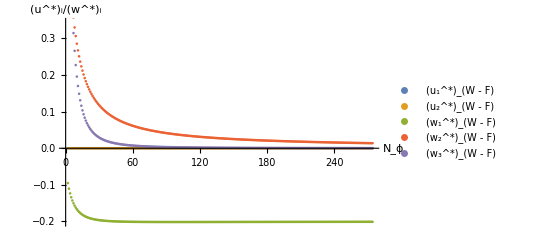

```mathematica
ListPlot[{Partition[Flatten[FPphi6x2d3U1WF],2]*Threaded[{1,1}], Partition[Flatten[FPphi6x2d3U2WF],2]*Threaded[{1,1}],Partition[Flatten[FPphi6x2d3W1WF],2]*Threaded[{1,1}],Partition[Flatten[FPphi6x2d3W2WF],2]*Threaded[{1,1}], Partition[Flatten[FPphi6x2d3W3WF],2]*Threaded[{1,1}]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{Style["(u_1^*)_(W - F)", FontSize->14], Style["(u_2^*)_(W - F)", FontSize->14], Style["(w_1^*)_(W - F)", FontSize->14],Style["(w_2^*)_(W - F)", FontSize->14],Style["(w_3^*)_(W - F)", FontSize->14]}, PlotRange->Automatic, TicksStyle->Directive[FontSize->13],AxesLabel->{Style["N_ϕ", FontSize->14],Style["(u^*)_i/(w^*)_i", FontSize->14]}]
```

```mathematica
Export["WFFPcoefficientsONmodelLL.jpg", %, "JPEG"]
```

WFFPcoefficientsONmodelLL.jpg

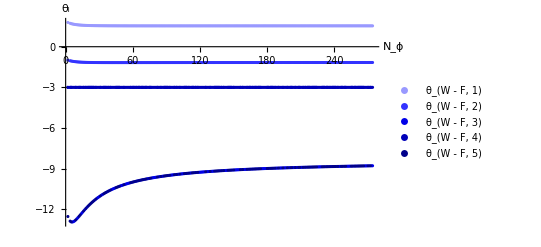

```mathematica
ClearAll[lightToDarkBlue]
lightToDarkBlue[n_,c_:Blue]:=Blend[{{0,White},{n/2,c},{n+3,Black}},#]&/@Range[n];
pthetaWF=ListPlot[{FPphi6x2d3EV1WF, FPphi6x2d3EV2WF,Re[FPphi6x2d3EV3WF],Re[FPphi6x2d3EV4WF], FPphi6x2d3EV5WF},AxesLabel->{HoldForm["N_ϕ"],HoldForm["θ_i"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{"θ_(W - F, 1)", "θ_(W - F, 2)", "θ_(W - F, 3)", "θ_(W - F, 4)","θ_(W - F, 5)"}, PlotStyle->lightToDarkBlue[5]]
```

#### (new) SSA fixed point

```mathematica
DumpGet["FPphi4d3U1.mx"];
DumpGet["FPphi4d3U2.mx"];
```

N=2

```mathematica
FindRoot[{Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,6], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,6], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,4], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,4], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,2], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,2],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,2], ϕ,0], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,2], ϕ,0],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,0], S2, 1]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,Subscript[S, 2],1], ϕ,0]}/.k-> 1//.Nphi-> 2, {{U[1],U3v1value[[1,2]]},{U[2],U3v2value[[1,2]]}, {W[1] , 0}, {W[2],0},{ W[3],0}}/. Nphi-> 2]
```

{U[1]→-6.77409,U[2]→-5.65347,W[1]→0.,W[2]→0.,W[3]→0.}

```mathematica
EVphi6/.Nphi-> 2//.{U[1]->-6.774092980448633,U[2]->-5.653468377327797,W[1]->0.,W[2]->0.,W[3]->0.}
```

{-3.2516,-2.65049,-2.30099,-1.95148,0.563672}

N=20

```mathematica
FindRoot[{Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,6], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,6], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,4], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,4], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,2], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,2],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,2], ϕ,0], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,2], ϕ,0],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,0], S2, 1]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,Subscript[S, 2],1], ϕ,0]}/.k-> 1//.Nphi-> 20, {{U[1],U3v1value[[19,2]]},{U[2],U3v2value[[19,2]]}, {W[1] , 0}, {W[2],0},{ W[3],0}}/. Nphi-> 20]
```

{U[1]→-1.74517,U[2]→-0.184631,W[1]→0.,W[2]→0.,W[3]→0.}

```mathematica
EVphi6/.Nphi-> 20//.%
```

{-3.33486,-2.85357,-2.70714,-2.56071,0.317242}

N=200

```mathematica
FindRoot[{Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,6], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,6], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,4], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,4], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,2], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,2],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,2], ϕ,0], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,2], ϕ,0],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,0], S2, 1]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,Subscript[S, 2],1], ϕ,0]}/.k-> 1//.Nphi-> 200, {{U[1],U3v1value[[199,2]]},{U[2],U3v2value[[199,2]]} ,{W[1] , 0}, {W[2],0},{ W[3],0}}/. Nphi-> 200]
EVphi6/.Nphi-> 200//.%
```

{U[1]→-0.191871,U[2]→-0.00183653,W[1]→0.,W[2]→0.,W[3]→0.}

{-3.34626,-2.8813,-2.76259,-2.64389,0.343277}

General tracking of the system

```mathematica
FPphi6x2d3U1={};(*First define 10 lists, in which the 5 fixed point values and the 5 stability coefficients can be saved*)
FPphi6x2d3U2={};
FPphi6x2d3W1={};
FPphi6x2d3W2={};
FPphi6x2d3W3={};
FPphi6x2d3EV1={};
FPphi6x2d3EV2={};
FPphi6x2d3EV3={};
FPphi6x2d3EV4={};
FPphi6x2d3EV5={};
```

```mathematica
FPvaluesfordifferentNphi6x2d3[Nmin_,Nmax_, step_]:= Do[y=x-1;
Solvall=FindRoot[{Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,6], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,6], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,4], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,4], Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,2], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,0], ϕ,2],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,2], ϕ,0], S2, 0]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,X,2], ϕ,0],
Coefficient[Coefficient[Coefficient[RHSWETTLPASSAmultiplescalarfields, X,0], ϕ,0], S2, 1]== Coefficient[Coefficient[LHSWETTLPASSAmultiplescalarfields,Subscript[S, 2],1], ϕ,0]}/.k-> 1//.Nphi-> x, {{U[1],U3v1value[[y,2]]},{U[2],U3v2value[[y,2]]} ,{W[1] , 0}, {W[2],0},{ W[3],0}}/. Nphi-> x];
EVSold3 = N[EVphi6/.Nphi-> x//.Solvall];(*Substitute the FP solution into the eigenvalue equations to get a numerical solution for those as well*)
AppendTo[FPphi6x2d3U1, {x,U[1]/. Solvall}];(*Save {Subscript[N, ϕ], Subscript[U, i]} in Subscript[U, i] list*)
AppendTo[FPphi6x2d3U2, {x,U[2]/. Solvall}];
AppendTo[FPphi6x2d3W1,{x,W[1]/.Solvall}];
AppendTo[FPphi6x2d3W2,{x, W[2]/.Solvall}];
AppendTo[FPphi6x2d3W3,{x, W[3]/.Solvall}]; 
AppendTo[FPphi6x2d3EV1, {x, -N[EVSold3[[1]]]}];(*Save {Subscript[N, ϕ], Subscript[θ, 1]} in Subscript[EV, 1] list*)
AppendTo[FPphi6x2d3EV2, {x,-N[ EVSold3[[2]]]}];
AppendTo[FPphi6x2d3EV3, {x, -N[EVSold3[[3]]]}];
AppendTo[FPphi6x2d3EV4, {x,-N[ EVSold3[[4]]]}];
AppendTo[FPphi6x2d3EV5, {x,-N[ EVSold3[[5]]]}];
Print[x],(*Counter to track the process when evaluating a large number of x's*)
 {x, Nmin, Nmax,step}](*Since the U3 phi4 values are determined up to 2000, this can also only be applied up to that number.*)
```

```mathematica
FPvaluesfordifferentNphi6x2d3[2,4, 1]
FPphi6x2d3EV3
FPphi6x2d3W1(*Check if the loop works as intended*)
```

{{2,2.30099},{3,2.39655},{4,2.46579}}

{{2,0.},{3,0.},{4,0.}}

```mathematica
FPvaluesfordifferentNphi6x2d3[2,402, 1](*The evaluation of the findroot for Subscript[N, ϕ] from 2 up to 402.*)
```

```mathematica
DumpSave["FPphi6x2d3U1.mx", FPphi6x2d3U1];(*Since evaluating takes a long time, it is prudent to save the results*)
DumpSave["FPphi6x2d3U2.mx", FPphi6x2d3U2];
DumpSave["FPphi6x2d3W1.mx", FPphi6x2d3W1];
DumpSave["FPphi6x2d3W2.mx", FPphi6x2d3W2];
DumpSave["FPphi6x2d3W3.mx", FPphi6x2d3W3];
DumpSave["FPphi6x2d3EV1.mx", FPphi6x2d3EV1];
DumpSave["FPphi6x2d3EV2.mx", FPphi6x2d3EV2];
DumpSave["FPphi6x2d3EV3.mx", FPphi6x2d3EV3];
DumpSave["FPphi6x2d3EV4.mx", FPphi6x2d3EV4];
DumpSave["FPphi6x2d3EV5.mx", FPphi6x2d3EV5];
```

```mathematica
DumpGet["FPphi6x2d3U1.mx"];
DumpGet["FPphi6x2d3U2.mx"];
DumpGet["FPphi6x2d3W1.mx"];
DumpGet["FPphi6x2d3W2.mx"];
DumpGet["FPphi6x2d3W3.mx"];
DumpGet["FPphi6x2d3EV1.mx"];
DumpGet["FPphi6x2d3EV2.mx"];
DumpGet["FPphi6x2d3EV3.mx"];
DumpGet["FPphi6x2d3EV4.mx"];
DumpGet["FPphi6x2d3EV5.mx"];
```

```mathematica
FPphi6x2d3EV3
```

{{2,2.30099},{3,2.39655},{4,2.46579},{5,2.51695},{6,2.55543},{7,2.58489},{8,2.60789},{9,2.62616},{10,2.64093},{11,2.65307},{12,2.66319},{13,2.67174},{14,2.67904},{15,2.68535},{16,2.69084},{17,2.69566},{18,2.69993},{19,2.70373},{20,2.70714},{21,2.71021},{22,2.71299},{23,2.71552},{24,2.71783},{25,2.71995},{26,2.7219},{27,2.7237},{28,2.72537},{29,2.72691},{30,2.72835},{31,2.7297},{32,2.73095},{33,2.73213},{34,2.73324},{35,2.73428},{36,2.73526},{37,2.73619},{38,2.73706},{39,2.73789},{40,2.73868},{41,2.73943},{42,2.74014},{43,2.74082},{44,2.74146},{45,2.74208},{46,2.74267},{47,2.74323},{48,2.74377},{49,2.74428},{50,2.74478},{51,2.74525},{52,2.74571},{53,2.74615},{54,2.74657},{55,2.74698},{56,2.74737},{57,2.74774},{58,2.74811},{59,2.74846},{60,2.7488},{61,2.74913},{62,2.74944},{63,2.74975},{64,2.75005},{65,2.75034},{66,2.75062},{67,2.75089},{68,2.75115},{69,2.7514},{70,2.75165},{71,2.75189},{72,2.75212},{73,2.75235},{74,2.75257},{75,2.75279},{76,2.75299},{77,2.7532},{78,2.7534},{79,2.75359},{80,2.75378},{81,2.75396},{82,2.75414},{83,2.75431},{84,2.75448},{85,2.75465},{86,2.75481},{87,2.75497},{88,2.75512},{89,2.75528},{90,2.75542},{91,2.75557},{92,2.75571},{93,2.75585},{94,2.75598},{95,2.75611},{96,2.75624},{97,2.75637},{98,2.75649},{99,2.75662},{100,2.75674},{101,2.75685},{102,2.75697},{103,2.75708},{104,2.75719},{105,2.7573},{106,2.7574},{107,2.75751},{108,2.75761},{109,2.75771},{110,2.75781},{111,2.7579},{112,2.758},{113,2.75809},{114,2.75818},{115,2.75827},{116,2.75836},{117,2.75845},{118,2.75853},{119,2.75861},{120,2.7587},{121,2.75878},{122,2.75886},{123,2.75894},{124,2.75901},{125,2.75909},{126,2.75916},{127,2.75924},{128,2.75931},{129,2.75938},{130,2.75945},{131,2.75952},{132,2.75958},{133,2.75965},{134,2.75972},{135,2.75978},{136,2.75985},{137,2.75991},{138,2.75997},{139,2.76003},{140,2.76009},{141,2.76015},{142,2.76021},{143,2.76027},{144,2.76032},{145,2.76038},{146,2.76044},{147,2.76049},{148,2.76054},{149,2.7606},{150,2.76065},{151,2.7607},{152,2.76075},{153,2.7608},{154,2.76085},{155,2.7609},{156,2.76095},{157,2.761},{158,2.76104},{159,2.76109},{160,2.76114},{161,2.76118},{162,2.76123},{163,2.76127},{164,2.76131},{165,2.76136},{166,2.7614},{167,2.76144},{168,2.76148},{169,2.76152},{170,2.76156},{171,2.7616},{172,2.76164},{173,2.76168},{174,2.76172},{175,2.76176},{176,2.7618},{177,2.76183},{178,2.76187},{179,2.76191},{180,2.76194},{181,2.76198},{182,2.76202},{183,2.76205},{184,2.76209},{185,2.76212},{186,2.76215},{187,2.76219},{188,2.76222},{189,2.76225},{190,2.76229},{191,2.76232},{192,2.76235},{193,2.76238},{194,2.76241},{195,2.76244},{196,2.76247},{197,2.7625},{198,2.76253},{199,2.76256},{200,2.76259},{201,2.76262},{202,2.76265},{203,2.76268},{204,2.76271},{205,2.76273},{206,2.76276},{207,2.76279},{208,2.76281},{209,2.76284},{210,2.76287},{211,2.76289},{212,2.76292},{213,2.76295},{214,2.76297},{215,2.763},{216,2.76302},{217,2.76305},{218,2.76307},{219,2.7631},{220,2.76312},{221,2.76314},{222,2.76317},{223,2.76319},{224,2.76321},{225,2.76324},{226,2.76326},{227,2.76328},{228,2.7633},{229,2.76333},{230,2.76335},{231,2.76337},{232,2.76339},{233,2.76341},{234,2.76343},{235,2.76346},{236,2.76348},{237,2.7635},{238,2.76352},{239,2.76354},{240,2.76356},{241,2.76358},{242,2.7636},{243,2.76362},{244,2.76364},{245,2.76366},{246,2.76368},{247,2.7637},{248,2.76371},{249,2.76373},{250,2.76375},{251,2.76377},{252,2.76379},{253,2.76381},{254,2.76383},{255,2.76384},{256,2.76386},{257,2.76388},{258,2.7639},{259,2.76391},{260,2.76393},{261,2.76395},{262,2.76396},{263,2.76398},{264,2.764},{265,2.76401},{266,2.76403},{267,2.76405},{268,2.76406},{269,2.76408},{270,2.7641},{271,2.76411},{272,2.76413},{273,2.76414},{274,2.76416},{275,2.76417},{276,2.76419},{277,2.7642},{278,2.76422},{279,2.76423},{280,2.76425},{281,2.76426},{282,2.76428},{283,2.76429},{284,2.76431},{285,2.76432},{286,2.76434},{287,2.76435},{288,2.76436},{289,2.76438},{290,2.76439},{291,2.76441},{292,2.76442},{293,2.76443},{294,2.76445},{295,2.76446},{296,2.76447},{297,2.76449},{298,2.7645},{299,2.76451},{300,2.76452},{301,2.76454},{302,2.76455},{303,2.76456},{304,2.76458},{305,2.76459},{306,2.7646},{307,2.76461},{308,2.76462},{309,2.76464},{310,2.76465},{311,2.76466},{312,2.76467},{313,2.76468},{314,2.7647},{315,2.76471},{316,2.76472},{317,2.76473},{318,2.76474},{319,2.76475},{320,2.76477},{321,2.76478},{322,2.76479},{323,2.7648},{324,2.76481},{325,2.76482},{326,2.76483},{327,2.76484},{328,2.76485},{329,2.76486},{330,2.76487},{331,2.76489},{332,2.7649},{333,2.76491},{334,2.76492},{335,2.76493},{336,2.76494},{337,2.76495},{338,2.76496},{339,2.76497},{340,2.76498},{341,2.76499},{342,2.765},{343,2.76501},{344,2.76502},{345,2.76503},{346,2.76504},{347,2.76505},{348,2.76506},{349,2.76507},{350,2.76507},{351,2.76508},{352,2.76509},{353,2.7651},{354,2.76511},{355,2.76512},{356,2.76513},{357,2.76514},{358,2.76515},{359,2.76516},{360,2.76517},{361,2.76518},{362,2.76518},{363,2.76519},{364,2.7652},{365,2.76521},{366,2.76522},{367,2.76523},{368,2.76524},{369,2.76524},{370,2.76525},{371,2.76526},{372,2.76527},{373,2.76528},{374,2.76529},{375,2.7653},{376,2.7653},{377,2.76531},{378,2.76532},{379,2.76533},{380,2.76534},{381,2.76534},{382,2.76535},{383,2.76536},{384,2.76537},{385,2.76537},{386,2.76538},{387,2.76539},{388,2.7654},{389,2.76541},{390,2.76541},{391,2.76542},{392,2.76543},{393,2.76544},{394,2.76544},{395,2.76545},{396,2.76546},{397,2.76547},{398,2.76547},{399,2.76548},{400,2.76549},{401,2.76549},{402,2.7655}}

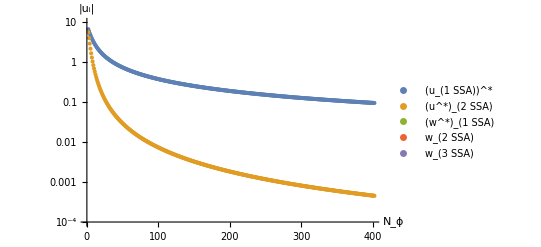

```mathematica
ListLogPlot[{Partition[Flatten[FPphi6x2d3U1],2]*Threaded[{1,-1}], Partition[Flatten[FPphi6x2d3U2],2]*Threaded[{1,-1}],Partition[Flatten[FPphi6x2d3W1],2]*Threaded[{1,-1}],Partition[Flatten[FPphi6x2d3W2],2]*Threaded[{1,-1}], Partition[Flatten[FPphi6x2d3W3],2]*Threaded[{1,-1}]},AxesLabel->{Style["N_ϕ", FontSize->14],Style["|(u_(.08i))^*|", FontSize->14]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{Style["(u_1^*)_SSA", FontSize->14], Style["(u_2^*)_SSA", FontSize->14], Style["(w_1^*)_SSA", FontSize->14],Style["(w_2^*)_SSA", FontSize->14],Style["(w_3^*)_SSA", FontSize->14]}, PlotRange->{{0, 400}, {10,0.0001}}, TicksStyle->Directive[FontSize->13]]
```

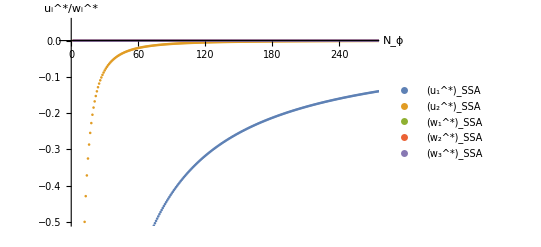

```mathematica
ListPlot[{Partition[Flatten[FPphi6x2d3U1],2]*Threaded[{1,1}], Partition[Flatten[FPphi6x2d3U2],2]*Threaded[{1,1}],Partition[Flatten[FPphi6x2d3W1],2]*Threaded[{1,1}],Partition[Flatten[FPphi6x2d3W2],2]*Threaded[{1,1}], Partition[Flatten[FPphi6x2d3W3],2]*Threaded[{1,-1}]},AxesLabel->{Style["N_ϕ", FontSize->14],Style["u_i^*/w_i^*", FontSize->14]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{Style["(u_1^*)_SSA", FontSize->14], Style["(u_2^*)_SSA", FontSize->14], Style["(w_1^*)_SSA", FontSize->14],Style["(w_2^*)_SSA", FontSize->14],Style["(w_3^*)_SSA", FontSize->14]}, PlotRange->{{-5,270}, {-0.5,0.05}}, TicksStyle->Directive[FontSize->13]]
```

```mathematica
Export["SSAFPcoefficientsONmodelLL.jpg", %, "JPEG"]
```

SSAFPcoefficientsONmodelLL.jpg

```mathematica
ClearAll[lightToDarkRed]
lightToDarkRed[n_,c_:Red]:=Blend[{{0,White},{n/2,c},{n+3,Black}},#]&/@Range[n]
ClearAll[lightToDarkBlue]
lightToDarkBlue[n_,c_:Blue]:=Blend[{{0,White},{n/2,c},{n+3,Black}},#]&/@Range[n]
```

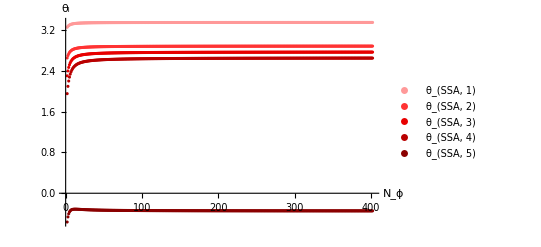

```mathematica
pthetassa=ListPlot[{FPphi6x2d3EV1, FPphi6x2d3EV2,Partition[Flatten[FPphi6x2d3EV3],2],Partition[Flatten[FPphi6x2d3EV4],2], Partition[Flatten[FPphi6x2d3EV5],2]},AxesLabel->{HoldForm["N_ϕ"],HoldForm["θ_i"]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, PlotLegends->{"θ_(SSA, 1)", "θ_(SSA, 2)", "θ_(SSA, 3)", "θ_(SSA, 4)","θ_(SSA, 5)"}, PlotStyle->lightToDarkRed[5]]
```

Only the SSA gives two stability coefficients: 3.34 and -1.26. It appears that the extra eigendirections introduced by the potential terms are relevant eigendirections with a positive stability coefficient.

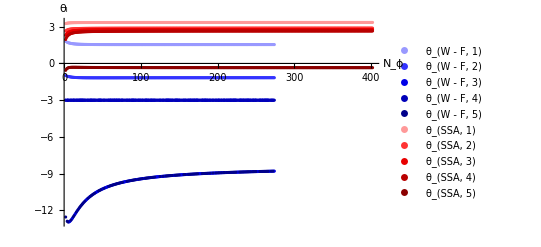

```mathematica
Show[pthetaWF,pthetassa, PlotRange-> {{0,270}, {4, -4}}]
```

```mathematica
Export["EVphi6WFenSSAFP.jpg", %, "JPEG"]
```

EVphi6WFenSSAFP.jpg

# Wetterich equation single scalar field d=4

```mathematica
Integrate[1/(2(4π)^2 Gamma[2])x (2 k^2)/(Γ2+k^2-x), {x, 0, k^2}]
```

ConditionalExpression[(k^2 (-k^2-(k^2+2 (V1+6 V2 ϕ^2+15 V3 ϕ^4)) Log[-2 (V1+6 V2 ϕ^2+15 V3 ϕ^4)]+(k^2+2 (V1+6 V2 ϕ^2+15 V3 ϕ^4)) Log[-k^2-2 (V1+6 V2 ϕ^2+15 V3 ϕ^4)]))/(16 π^2), ]

This gets odd stuff. Including at least the normal kinetic term might be a good idea. 
Γ_k=X+V1ϕ^2+V2ϕ^4+V3ϕ^6 
Γ_k^(2) = p^2+2V1+12V2 ϕ^2+30 V3 ϕ^4

## Up to ϕ^6

### Set-up

```mathematica
Integrate[1/(2(4π)^2 Gamma[2])x (2 k^2)/(x+Γ2+k^2-x), {x, 0, k^2}]
```

k^6/(32 π^2 (k^2+2 V1+12 V2 ϕ^2+30 V3 ϕ^4))

```mathematica
Γ2 = 2V1+12V2 ϕ^2+30 V3 ϕ^4(*the part independent of momentum of the 2nd derivative effective action up to ϕ^4*)
```

2 V1+12 V2 ϕ^2+30 V3 ϕ^4

```mathematica
RHS = k^6/(32 π^2 (k^2+2 V1+12 V2 ϕ^2+30 V3 ϕ^4))/. V1-> v[1] k^2 /. V2-> v[2] /. V3-> v[3] k^-2
```

k^6/(32 π^2 (k^2+2 k^2 v[1]+12 ϕ^2 v[2]+(30 ϕ^4 v[3])/k^2))

```mathematica
LHS = (2 k^2 v[1]+k^2 βv[1])ϕ^2+(βv[2])ϕ^4+ (βv[3]/(.08k)^2-2/k^2 v[3])ϕ^6
```

ϕ^2 (2 k^2 v[1]+k^2 βv[1])+ϕ^4 βv[2]+ϕ^6 (-(2 v[3])/k^2+βv[3]/(.08k)^2)

```mathematica
RHSS=Series[RHS, {ϕ, 0, 6}]
```

k^4/(32 π^2 (1+2 v[1]))-(3 (k^2 v[2]) ϕ^2)/(8 (π^2 (1+2 v[1])^2))+(k^6 ((144 v[2]^2)/((k^2+2 k^2 v[1])^2)-(30 v[3])/(k^2 (k^2+2 k^2 v[1]))) ϕ^4)/(32 π^2 (k^2+2 k^2 v[1]))+(k^6 (-(1728 v[2]^3)/((k^2+2 k^2 v[1])^3)+(720 v[2] v[3])/(k^2 (k^2+2 k^2 v[1])^2)) ϕ^6)/(32 π^2 (k^2+2 k^2 v[1]))+O[ϕ]^7

### Finding fixed points

```mathematica
βv[1]=0;
βv[2]=0;
βv[3]=0;
```

```mathematica
Solve[Coefficient[RHSS, ϕ^6]== Coefficient[LHS, ϕ^6], v[3]]
```

{{v[3]→(108 v[2]^3)/((1+2 v[1]) (4 π^2+24 π^2 v[1]+48 π^2 v[1]^2+32 π^2 v[1]^3+45 v[2]))}}

```mathematica
V3waarde = (108 v[2]^3)/((1+2 v[1]) (4 π^2+24 π^2 v[1]+48 π^2 v[1]^2+32 π^2 v[1]^3+45 v[2]));
```

```mathematica
Solve[Coefficient[RHSS, ϕ^4]== Coefficient[LHS, ϕ^4] /.v[3]-> V3waarde, v[2]](*If v3 is set to 0, as expected only the 0 solutions appear*)
```

{{v[2]→0},{v[2]→0},{v[2]→-8/45 π^2 (1+2 v[1])^3}}

```mathematica
V2waarde = -8/45 π^2 (1+2 v[1])^3;
```

```mathematica
Solve[Coefficient[RHSS, ϕ^2]== Coefficient[LHS, ϕ^2] /.v[3]-> V3waarde/. v[2]->0, v[1]]
```

{{v[1]→0}}

```mathematica
Solve[Coefficient[RHSS, ϕ^2]== Coefficient[LHS, ϕ^2] /.v[3]-> V3waarde/. v[2]->V2waarde, v[1]]
```

{{v[1]→1/28}}

### Finding beta functions

```mathematica
Clear[βv]
```

```mathematica
Simplify[Solve[Coefficient[RHSS, ϕ^6]== Coefficient[LHS, ϕ^6], βv[3]]]
```

{{βv[3]→((.08k)^2 (-108 v[2]^3+4 π^2 (1+2 v[1])^4 v[3]+45 (1+2 v[1]) v[2] v[3]))/(2 k^2 π^2 (1+2 v[1])^4)}}

```mathematica
βv[v_[1], v_[2], v_[3]][3]=(-108 v[2]^3+4 π^2 (1+2 v[1])^4 v[3]+45 (1+2 v[1]) v[2] v[3])/(2  π^2 (1+2 v[1])^4)
```

(-108 v[2]^3+4 π^2 (1+2 v[1])^4 v[3]+45 (1+2 v[1]) v[2] v[3])/(2 π^2 (1+2 v[1])^4)

```mathematica
Solve[Coefficient[RHSS, ϕ^4]== Coefficient[LHS, ϕ^4], βv[2]]
```

{{βv[2]→(3 (24 v[2]^2-5 v[3]-10 v[1] v[3]))/(16 π^2 (1+2 v[1])^3)}}

```mathematica
βv[v_[1], v_[2], v_[3]][2]=(3 (24 v[2]^2-5 v[3]-10 v[1] v[3]))/(16 π^2 (1+2 v[1])^3)
```

(3 (24 v[2]^2-5 v[3]-10 v[1] v[3]))/(16 π^2 (1+2 v[1])^3)

```mathematica
Simplify[Solve[Coefficient[RHSS, ϕ^2]== Coefficient[LHS, ϕ^2], βv[1]]]
```

{{βv[1]→-(16 v[1] (π+2 π v[1])^2+3 v[2])/(8 (π+2 π v[1])^2)}}

```mathematica
βv[v_[1], v_[2], v_[3]][1]=-(16 v[1] (π+2 π v[1])^2+3 v[2])/(8 (π+2 π v[1])^2)
```

-(16 v[1] (π+2 π v[1])^2+3 v[2])/(8 (π+2 π v[1])^2)

### Finding eigenvalues stability matrix

```mathematica
mat:=Table[D[βv[v[1], v[2], v[3]][a], v[b]],{a,1,3},{b,1,3}](*Generates the stability matrix*)
mat//MatrixForm(*Prints the stability matrix in Matrixform*)
EVLPAphi6 = Eigenvalues[%]/. v[3]-> V3waarde//. v[2]-> V2waarde//.v[1]-> 1/28
```

(-(64 π v[1] (π+2 π v[1])+16 (π+2 π v[1])^2)/(8 (π+2 π v[1])^2)+(π (16 v[1] (π+2 π v[1])^2+3 v[2]))/(2 (π+2 π v[1])^3) | -3/(8 (π+2 π v[1])^2) | 0
-(15 v[3])/(8 π^2 (1+2 v[1])^3)-(9 (24 v[2]^2-5 v[3]-10 v[1] v[3]))/(8 π^2 (1+2 v[1])^4) | (9 v[2])/(π^2 (1+2 v[1])^3) | (3 (-5-10 v[1]))/(16 π^2 (1+2 v[1])^3)
(32 π^2 (1+2 v[1])^3 v[3]+90 v[2] v[3])/(2 π^2 (1+2 v[1])^4)-(4 (-108 v[2]^3+4 π^2 (1+2 v[1])^4 v[3]+45 (1+2 v[1]) v[2] v[3]))/(π^2 (1+2 v[1])^5) | (-324 v[2]^2+45 (1+2 v[1]) v[3])/(2 π^2 (1+2 v[1])^4) | (4 π^2 (1+2 v[1])^4+45 (1+2 v[1]) v[2])/(2 π^2 (1+2 v[1])^4))

{(33614 Root-624.Root[23354340820312500 π^6+3341350712109375 π^4 #1+89887659592500 π^2 #1^2+678223072849 #1^3&,1]-624.3007781821934)/(759375 π^2),(33614 Root-595.Root[23354340820312500 π^6+3341350712109375 π^4 #1+89887659592500 π^2 #1^2+678223072849 #1^3&,2]-594.572169697327)/(759375 π^2),(33614 Root-89.2Root[23354340820312500 π^6+3341350712109375 π^4 #1+89887659592500 π^2 #1^2+678223072849 #1^3&,3]-89.18582545459905)/(759375 π^2)}

```mathematica
N[EVLPAphi6]
```

{-2.8,-2.66667,-0.4}

## Up to ϕ^8

I was expecting there to not be an UV-relevant solution at all, lets see if it disappears for an extra order ϕ^2

```mathematica
Integrate[1/(2(4π)^2 Gamma[2])x (2 k^2)/(x+Γ2+k^2-x), {x, 0, k^2}]
```

k^6/(32 π^2 (k^2+Γ2))

```mathematica
Γ2 =  2V1+12V2 ϕ^2+30 V3 ϕ^4+8*7V4 ϕ^6
```

2 V1+12 V2 ϕ^2+30 V3 ϕ^4+56 V4 ϕ^6

```mathematica
RHSphi8 =Collect[Series[ k^6/(32 π^2 (k^2+2 V1+12 V2 ϕ^2+30 V3 ϕ^4+56 V4 ϕ^6)), {ϕ, 0, 10}]/. V1-> v[1] k^2 /. V2-> v[2] /. V3-> v[3] k^-2/. V4-> v[4] k^-4, k]
```

k^6/(32 π^2 (k^2+2 k^2 v[1]))-(3 (k^6 v[2]) ϕ^2)/(8 (π^2 (k^2+2 k^2 v[1])^2))+(k^6 ((144 v[2]^2)/((k^2+2 k^2 v[1])^2)-(30 v[3])/(k^2 (k^2+2 k^2 v[1]))) ϕ^4)/(32 π^2 (k^2+2 k^2 v[1]))+(k^6 (-(1728 v[2]^3)/((k^2+2 k^2 v[1])^3)+(720 v[2] v[3])/(k^2 (k^2+2 k^2 v[1])^2)-(56 v[4])/(k^4 (k^2+2 k^2 v[1]))) ϕ^6)/(32 π^2 (k^2+2 k^2 v[1]))+(k^6 ((20736 v[2]^4)/((k^2+2 k^2 v[1])^4)-(12960 v[2]^2 v[3])/(k^2 (k^2+2 k^2 v[1])^3)+(900 v[3]^2)/(k^4 (k^2+2 k^2 v[1])^2)+(1344 v[2] v[4])/(k^4 (k^2+2 k^2 v[1])^2)) ϕ^8)/(32 π^2 (k^2+2 k^2 v[1]))+(k^6 (-(248832 v[2]^5)/((k^2+2 k^2 v[1])^5)+(207360 v[2]^3 v[3])/(k^2 (k^2+2 k^2 v[1])^4)-(32400 v[2] v[3]^2)/(k^4 (k^2+2 k^2 v[1])^3)-(24192 v[2]^2 v[4])/(k^4 (k^2+2 k^2 v[1])^3)+(3360 v[3] v[4])/(k^6 (k^2+2 k^2 v[1])^2)) ϕ^10)/(32 π^2 (k^2+2 k^2 v[1]))+O[ϕ]^11

```mathematica
LHSphi8 = (2 k^2 v[1]+k^2 βv[1])ϕ^2+(βv[2])ϕ^4+ (βv[3]/(.08k)^2-2/k^2 v[3])ϕ^6 +(βv[4]/(.08k)^4-4/k^4 v[4])ϕ^8
```

ϕ^2 (2 k^2 v[1]+k^2 βv[1])+ϕ^4 βv[2]+ϕ^6 (-(2 v[3])/k^2+βv[3]/(.08k)^2)+ϕ^8 (-(4 v[4])/k^4+βv[4]/(.08k)^4)

### Finding fixed points

The first step is again to find the position of the fixed points by setting beta to zero and solving per order of ϕ

```mathematica
βv[1]=0;
βv[2]=0;
βv[3]=0;
βv[4]=0;
Simplify[Solve[Coefficient[RHSphi8, ϕ^8]== Coefficient[LHSphi8, ϕ^8], v[4]]]
```

{{v[4]→-(9 (576 v[2]^4-360 (1+2 v[1]) v[2]^2 v[3]+25 (1+2 v[1])^2 v[3]^2))/(16 (1+2 v[1])^2 (2 π^2 (1+2 v[1])^3+21 v[2]))}}

```mathematica
v4d4phi8val = -(9 (576 v[2]^4-360 (1+2 v[1]) v[2]^2 v[3]+25 (1+2 v[1])^2 v[3]^2))/(32 π^2 (1+2 v[1])^5);
```

```mathematica
Simplify[Solve[Coefficient[RHSphi8, ϕ^6]== Coefficient[LHSphi8, ϕ^6]/. v[4]-> v4d4phi8val, v[3]]]
```

{{v[3]→-1/(1575 (1+2 v[1])^2)4 (32 π^4 (1+2 v[1])^7+360 π^2 (1+2 v[1])^4 v[2]-2835 v[2]^2-5670 v[1] v[2]^2+k^2 (1+2 v[1])^7 √((1024 π^8 (1+2 v[1])^12+23040 π^6 (1+2 v[1])^9 v[2]-51840 π^4 (1+2 v[1])^6 v[2]^2-1360800 π^2 (1+2 v[1])^3 v[2]^3+4465125 v[2]^4)/(k^4 (1+2 v[1])^12)))},{v[3]→1/(1575 (1+2 v[1])^2)4 (-32 π^4 (1+2 v[1])^7-360 π^2 (1+2 v[1])^4 v[2]+2835 v[2]^2+5670 v[1] v[2]^2+k^2 (1+2 v[1])^7 √((1024 π^8 (1+2 v[1])^12+23040 π^6 (1+2 v[1])^9 v[2]-51840 π^4 (1+2 v[1])^6 v[2]^2-1360800 π^2 (1+2 v[1])^3 v[2]^3+4465125 v[2]^4)/(k^4 (1+2 v[1])^12)))}}

```mathematica
v3d4phi8val1= -1/(1575 (1+2 v[1])^2)4 (32 π^4 (1+2 v[1])^7+360 π^2 (1+2 v[1])^4 v[2]-2835 v[2]^2-5670 v[1] v[2]^2+(1+2 v[1])^7 √((1024 π^8 (1+2 v[1])^12+23040 π^6 (1+2 v[1])^9 v[2]-51840 π^4 (1+2 v[1])^6 v[2]^2-1360800 π^2 (1+2 v[1])^3 v[2]^3+4465125 v[2]^4)/(1+2 v[1])^12));
```

```mathematica
v3d4phi8val2 = 1/(1575 (1+2 v[1])^2)4 (-32 π^4 (1+2 v[1])^7-360 π^2 (1+2 v[1])^4 v[2]+2835 v[2]^2+5670 v[1] v[2]^2+(1+2 v[1])^7 √((1024 π^8 (1+2 v[1])^12+23040 π^6 (1+2 v[1])^9 v[2]-51840 π^4 (1+2 v[1])^6 v[2]^2-1360800 π^2 (1+2 v[1])^3 v[2]^3+4465125 v[2]^4)/(1+2 v[1])^12));
```

```mathematica
Simplify[Solve[Coefficient[RHSphi8, ϕ^4]== Coefficient[LHSphi8, ϕ^4]/. v[4]-> v4d4phi8val/. v[3]-> v3d4phi8val1, v[2]]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{v[2]→-2/315 π^2 (-15-90 v[1]-180 v[1]^2-120 v[1]^3+√1065 √((1+2 v[1])^6))},{v[2]→2/315 π^2 (15+90 v[1]+180 v[1]^2+120 v[1]^3+√1065 √((1+2 v[1])^6))}}

```mathematica
Simplify[Solve[Coefficient[RHSphi8, ϕ^4]== Coefficient[LHSphi8, ϕ^4]/. v[4]-> v4d4phi8val/. v[3]-> v3d4phi8val2, v[2]]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{v[2]→0},{v[2]→-2/315 π^2 (-15-90 v[1]-180 v[1]^2-120 v[1]^3+√1065 √((1+2 v[1])^6))},{v[2]→2/315 π^2 (15+90 v[1]+180 v[1]^2+120 v[1]^3+√1065 √((1+2 v[1])^6))}}

```mathematica
v2d4phi8val1 = -2/315 π^2 (-15-90 v[1]-180 v[1]^2-120 v[1]^3+√1065 √((1+2 v[1])^6));
v2d4phi8val2 = 2/315 π^2 (15+90 v[1]+180 v[1]^2+120 v[1]^3+√1065 √((1+2 v[1])^6));
```

```mathematica
Simplify[Solve[Coefficient[RHSphi8, ϕ^2]== Coefficient[LHSphi8, ϕ^2]/. v[4]-> v4d4phi8val/. v[3]-> v3d4phi8val1/. v[2]-> v2d4phi8val1, v[1]]]
Simplify[Solve[Coefficient[RHSphi8, ϕ^2]== Coefficient[LHSphi8, ϕ^2]/. v[4]-> v4d4phi8val/. v[3]-> v3d4phi8val1/. v[2]-> v2d4phi8val2, v[1]]]
Simplify[Solve[Coefficient[RHSphi8, ϕ^2]== Coefficient[LHSphi8, ϕ^2]/. v[4]-> v4d4phi8val/. v[3]-> v3d4phi8val2/. v[2]-> v2d4phi8val1, v[1]]]
Simplify[Solve[Coefficient[RHSphi8, ϕ^2]== Coefficient[LHSphi8, ϕ^2]/. v[4]-> v4d4phi8val/. v[3]-> v3d4phi8val2/. v[2]-> v2d4phi8val2, v[1]]]
```

{{v[1]→1/896 (-13+√1065)}}

{{v[1]→1/896 (-13-√1065)}}

{{v[1]→1/896 (-13+√1065)}}

{{v[1]→1/896 (-13-√1065)}}

```mathematica
v1d4phi8val11=1/896 (-13+√1065);
v1d4phi8val12 = 1/896 (-13-√1065);
```

### Finding the beta functions

```mathematica
Clear[βv]
```

```mathematica
Simplify[Solve[Coefficient[RHSphi8, ϕ^8]== Coefficient[LHSphi8, ϕ^8], βv[4]]]
```

{{βv[4]→((.08k)^4 (5184 v[2]^4-3240 (1+2 v[1]) v[2]^2 v[3]+336 (1+2 v[1])^2 v[2] v[4]+(1+2 v[1])^2 (225 v[3]^2+32 π^2 (1+2 v[1])^3 v[4])))/(8 k^4 π^2 (1+2 v[1])^5)}}

```mathematica
βv[v_[1], v_[2], v_[3], v_[4]][4]= (.08 (5184 v[2]^4-3240 (1+2 v[1]) v[2]^2 v[3]+336 (1+2 v[1])^2 v[2] v[4]+(1+2 v[1])^2 (225 v[3]^2+32 π^2 (1+2 v[1])^3 v[4])))/(8  π^2 (1+2 v[1])^5);
```

```mathematica
Simplify[Solve[Coefficient[RHSphi8, ϕ^6]== Coefficient[LHSphi8, ϕ^6], βv[3]]]
```

{{βv[3]→((.08k)^2 (-216 v[2]^3+90 (1+2 v[1]) v[2] v[3]+(1+2 v[1])^2 (8 (π+2 π v[1])^2 v[3]-7 v[4])))/(4 k^2 π^2 (1+2 v[1])^4)}}

```mathematica
βv[v_[1], v_[2], v_[3], v_[4]][3]=(-216 v[2]^3+90 (1+2 v[1]) v[2] v[3]+(1+2 v[1])^2 (8 (π+2 π v[1])^2 v[3]-7 v[4]))/(4 π^2 (1+2 v[1])^4);
```

```mathematica
Simplify[Solve[Coefficient[RHSphi8, ϕ^4]== Coefficient[LHSphi8, ϕ^4], βv[2]]]
```

{{βv[2]→(72 v[2]^2-15 (1+2 v[1]) v[3])/(16 π^2 (1+2 v[1])^3)}}

```mathematica
βv[v_[1], v_[2], v_[3], v_[4]][2]=(72 v[2]^2-15 (1+2 v[1]) v[3])/(16 π^2 (1+2 v[1])^3);
```

```mathematica
Simplify[Solve[Coefficient[RHSphi8, ϕ^2]== Coefficient[LHSphi8, ϕ^2], βv[1]]]
```

{{βv[1]→-(16 v[1] (π+2 π v[1])^2+3 v[2])/(8 (π+2 π v[1])^2)}}

```mathematica
βv[v_[1], v_[2], v_[3], v_[4]][1] = -(16 v[1] (π+2 π v[1])^2+3 v[2])/(8 (π+2 π v[1])^2);
```

### Finding the stability matrix and its eigenvalues

```mathematica
mat:=Table[D[βv[v[1], v[2], v[3], v[4]][a], v[b]],{a,1,4},{b,1,4}](*Generates the stability matrix*)
mat//MatrixForm(*Prints the stability matrix in Matrixform*)
EVLPAphi8 = Eigenvalues[%]
```

(-(64 π v[1] (π+2 π v[1])+16 (π+2 π v[1])^2)/(8 (π+2 π v[1])^2)+(π (16 v[1] (π+2 π v[1])^2+3 v[2]))/(2 (π+2 π v[1])^3) | -3/(8 (π+2 π v[1])^2) | 0 | 0
-(15 v[3])/(8 π^2 (1+2 v[1])^3)-(3 (72 v[2]^2-15 (1+2 v[1]) v[3]))/(8 π^2 (1+2 v[1])^4) | (9 v[2])/(π^2 (1+2 v[1])^3) | -15/(16 π^2 (1+2 v[1])^2) | 0
(32 π (1+2 v[1])^2 (π+2 π v[1]) v[3]+180 v[2] v[3]+4 (1+2 v[1]) (8 (π+2 π v[1])^2 v[3]-7 v[4]))/(4 π^2 (1+2 v[1])^4)-(2 (-216 v[2]^3+90 (1+2 v[1]) v[2] v[3]+(1+2 v[1])^2 (8 (π+2 π v[1])^2 v[3]-7 v[4])))/(π^2 (1+2 v[1])^5) | (-648 v[2]^2+90 (1+2 v[1]) v[3])/(4 π^2 (1+2 v[1])^4) | (8 (1+2 v[1])^2 (π+2 π v[1])^2+90 (1+2 v[1]) v[2])/(4 π^2 (1+2 v[1])^4) | -7/(4 π^2 (1+2 v[1])^2)
(.08 (-6480 v[2]^2 v[3]+192 π^2 (1+2 v[1])^4 v[4]+1344 (1+2 v[1]) v[2] v[4]+4 (1+2 v[1]) (225 v[3]^2+32 π^2 (1+2 v[1])^3 v[4])))/(8 π^2 (1+2 v[1])^5)-(5 .08 (5184 v[2]^4-3240 (1+2 v[1]) v[2]^2 v[3]+336 (1+2 v[1])^2 v[2] v[4]+(1+2 v[1])^2 (225 v[3]^2+32 π^2 (1+2 v[1])^3 v[4])))/(4 π^2 (1+2 v[1])^6) | (.08 (20736 v[2]^3-6480 (1+2 v[1]) v[2] v[3]+336 (1+2 v[1])^2 v[4]))/(8 π^2 (1+2 v[1])^5) | (.08 (-3240 (1+2 v[1]) v[2]^2+450 (1+2 v[1])^2 v[3]))/(8 π^2 (1+2 v[1])^5) | (.08 (32 π^2 (1+2 v[1])^5+336 (1+2 v[1])^2 v[2]))/(8 π^2 (1+2 v[1])^5))

```mathematica
EVLPAphi8/. v[4]-> v4d4phi8val//. v[3]-> v3d4phi8val1//. v[2]-> v2d4phi8val1//.v[1]-> v1d4phi8val11
```

```mathematica
N[%205, 3]
```

{0.0049 Root[-1.3439779227×10^115 .08+(-1.7823133599×10^111-4.91097927389×10^112 .08) #1+(6.363078885173×10^109-7.3792624097×10^108 .08) #1^2+(3.646511077146×10^107+6.933063655358×10^106 .08) #1^3+4.8316447736477×10^104 #1^4&,1],0.0049 Root[-1.3439779227×10^115 .08+(-1.7823133599×10^111-4.91097927389×10^112 .08) #1+(6.363078885173×10^109-7.3792624097×10^108 .08) #1^2+(3.646511077146×10^107+6.933063655358×10^106 .08) #1^3+4.8316447736477×10^104 #1^4&,2],0.0049 Root[-1.3439779227×10^115 .08+(-1.7823133599×10^111-4.91097927389×10^112 .08) #1+(6.363078885173×10^109-7.3792624097×10^108 .08) #1^2+(3.646511077146×10^107+6.933063655358×10^106 .08) #1^3+4.8316447736477×10^104 #1^4&,3],0.0049 Root[-1.3439779227×10^115 .08+(-1.7823133599×10^111-4.91097927389×10^112 .08) #1+(6.363078885173×10^109-7.3792624097×10^108 .08) #1^2+(3.646511077146×10^107+6.933063655358×10^106 .08) #1^3+4.8316447736477×10^104 #1^4&,4]}

```mathematica
EVLPAphi8/. v[4]-> v4d4phi8val//. v[3]-> v3d4phi8val1//. v[2]-> v2d4phi8val2//.v[1]-> v1d4phi8val12
```

```mathematica
N[%209, 3]
```

{0.0121 Root[-6.01741751312×10^114 .08+(6.944720705338×10^111+2.5142582187×10^112 .08) #1+(-1.665915976976×10^109+3.9124911748974×10^110 .08) #1^2+(-3.99692152166409×10^107-6.68887884688912×10^107 .08) #1^3+4.83164477364766×10^104 #1^4&,1],0.0121 Root[-6.01741751312×10^114 .08+(6.944720705338×10^111+2.5142582187×10^112 .08) #1+(-1.665915976976×10^109+3.9124911748974×10^110 .08) #1^2+(-3.99692152166409×10^107-6.68887884688912×10^107 .08) #1^3+4.83164477364766×10^104 #1^4&,2],0.0121 Root[-6.01741751312×10^114 .08+(6.944720705338×10^111+2.5142582187×10^112 .08) #1+(-1.665915976976×10^109+3.9124911748974×10^110 .08) #1^2+(-3.99692152166409×10^107-6.68887884688912×10^107 .08) #1^3+4.83164477364766×10^104 #1^4&,3],0.0121 Root[-6.01741751312×10^114 .08+(6.944720705338×10^111+2.5142582187×10^112 .08) #1+(-1.665915976976×10^109+3.9124911748974×10^110 .08) #1^2+(-3.99692152166409×10^107-6.68887884688912×10^107 .08) #1^3+4.83164477364766×10^104 #1^4&,4]}

```mathematica
EVLPAphi8/. v[4]-> v4d4phi8val//. v[3]-> v3d4phi8val2//. v[2]-> v2d4phi8val2//.v[1]-> v1d4phi8val12
N[%,3]
```

{0.0121 Root[-1.17868797182×10^115 .08+(8.634247796545×10^111-8.0501343615×10^111 .08) #1+(3.992418322199×10^108+4.8159977164207×10^110 .08) #1^2+(-3.99692152166409×10^107-6.68887884688912×10^107 .08) #1^3+4.83164477364766×10^104 #1^4&,1],0.0121 Root[-1.17868797182×10^115 .08+(8.634247796545×10^111-8.0501343615×10^111 .08) #1+(3.992418322199×10^108+4.8159977164207×10^110 .08) #1^2+(-3.99692152166409×10^107-6.68887884688912×10^107 .08) #1^3+4.83164477364766×10^104 #1^4&,2],0.0121 Root[-1.17868797182×10^115 .08+(8.634247796545×10^111-8.0501343615×10^111 .08) #1+(3.992418322199×10^108+4.8159977164207×10^110 .08) #1^2+(-3.99692152166409×10^107-6.68887884688912×10^107 .08) #1^3+4.83164477364766×10^104 #1^4&,3],0.0121 Root[-1.17868797182×10^115 .08+(8.634247796545×10^111-8.0501343615×10^111 .08) #1+(3.992418322199×10^108+4.8159977164207×10^110 .08) #1^2+(-3.99692152166409×10^107-6.68887884688912×10^107 .08) #1^3+4.83164477364766×10^104 #1^4&,4]}

```mathematica
EVLPAphi8/. v[4]-> v4d4phi8val//. v[3]-> v3d4phi8val2//. v[2]-> v2d4phi8val1//.v[1]-> v1d4phi8val11
N[%,3]
```

{0.0049 Root[-1.61285796797×10^115 .08+(1.586973354923×10^112+3.5220839083×10^112 .08) #1+(1.1006285968271×10^110+1.9576104747585×10^110 .08) #1^2+(3.64651107714599×10^107+6.9330636553585×10^106 .08) #1^3+4.83164477364766×10^104 #1^4&,1],0.0049 Root[-1.61285796797×10^115 .08+(1.586973354923×10^112+3.5220839083×10^112 .08) #1+(1.1006285968271×10^110+1.9576104747585×10^110 .08) #1^2+(3.64651107714599×10^107+6.9330636553585×10^106 .08) #1^3+4.83164477364766×10^104 #1^4&,2],0.0049 Root[-1.61285796797×10^115 .08+(1.586973354923×10^112+3.5220839083×10^112 .08) #1+(1.1006285968271×10^110+1.9576104747585×10^110 .08) #1^2+(3.64651107714599×10^107+6.9330636553585×10^106 .08) #1^3+4.83164477364766×10^104 #1^4&,3],0.0049 Root[-1.61285796797×10^115 .08+(1.586973354923×10^112+3.5220839083×10^112 .08) #1+(1.1006285968271×10^110+1.9576104747585×10^110 .08) #1^2+(3.64651107714599×10^107+6.9330636553585×10^106 .08) #1^3+4.83164477364766×10^104 #1^4&,4]}